```mathematica
SetDirectory[FileNameJoin[{$PACKAGES}]]
Import["polarization.wl"]
SetDirectory[FileNameJoin[{$PACKAGES,"sampleData","polarization"}]]
```

C:\Users\kahrendsen2\Box Sync\Research\mathematicaRb\packages

C:\Users\kahrendsen2\Box Sync\Research\mathematicaRb\packages\sampleData\polarization

## Polarization Prototyping

Averaging Methods

## Fourier Averaging

```mathematica
fn=FileNames[RegularExpression["POL.*_[0-9]*.dat"]];
names=Partition[fn,Length[fn]/4];
aout1=Catenate[{names[[1]],names[[3]]}]
aout1=Take[aout1,{1,-1,3}]
```

{POL2019-03-15_184016.dat,POL2019-03-15_184132.dat,POL2019-03-15_184246.dat,POL2019-03-15_184409.dat,POL2019-03-15_184523.dat,POL2019-03-15_184637.dat,POL2019-03-15_184803.dat,POL2019-03-15_184917.dat,POL2019-03-15_185031.dat,POL2019-03-15_190359.dat,POL2019-03-15_190513.dat,POL2019-03-15_190627.dat,POL2019-03-15_190750.dat,POL2019-03-15_190904.dat,POL2019-03-15_191018.dat,POL2019-03-15_191144.dat,POL2019-03-15_191258.dat,POL2019-03-15_191412.dat}

{POL2019-03-15_184016.dat,POL2019-03-15_184409.dat,POL2019-03-15_184803.dat,POL2019-03-15_190359.dat,POL2019-03-15_190750.dat,POL2019-03-15_191144.dat}

```mathematica
f=ImportFile[aout1];

	signals={};
	fileNames={};
	For[i=1,i<=Length[f],i++,
		header=f[[i]][[1]];
		dataset=f[[i]][[2]];
		counts=Normal[dataset[All,"COUNT"]];
		current=Abs[Normal[dataset[All,"CURRENT"]]]*10^(-header["SCALE"])/nA;
		dwellTime=header["DWELL(s)"];
		signal=NormalizePolarizationData[counts,current,dwellTime];
		AppendTo[signals,signal];
		AppendTo[fileNames,header["File"]];
	];
```

```mathematica
dfts=DFT/@signals
```

{<|Sin Coefficients→<|0→0.,1→0.267567,2→0.0627774,3→-0.0642355,4→-0.100679,5→0.139425,6→-0.0675406,7→0.0228193,8→0.171439,9→-0.139073,10→0.0950731,11→0.0851951,12→0.214163,13→0.00774144,14→-0.210405,15→-0.0129364,16→0.230033,17→0.163876,18→-0.150893,19→0.0427707,20→-0.10496,21→0.114207,22→-0.0568999,23→0.129545,24→-0.00484242,25→0.161692,26→0.107564,27→-0.0824136,28→0.0959008,29→0.0334963|>,Cos Coefficients→<|0→14.6236,1→-0.285005,2→-0.457526,3→-0.657781,4→-0.221117,5→-0.669132,6→-0.349616,7→-0.268054,8→-0.340364,9→-0.610026,10→-0.271194,11→-0.220314,12→-0.283519,13→-0.693363,14→-0.315139,15→-0.414575,16→-0.437042,17→-0.497016,18→-0.336923,19→-0.536006,20→-0.403947,21→-0.438685,22→-0.46083,23→-0.658757,24→-0.507064,25→-0.370872,26→-0.577422,27→-0.25669,28→-0.537031,29→-0.321635|>,Sin Coefficients Error→<||>,Cos Coefficients Error→<||>|>,<|Sin Coefficients→<|0→0.,1→0.121773,2→0.173415,3→0.115475,4→-0.118677,5→-0.0254375,6→-0.191116,7→0.128475,8→0.036733,9→0.0290439,10→-0.159699,11→-0.0708485,12→0.0558753,13→-0.144016,14→-0.122827,15→-0.0778582,16→-0.049566,17→-0.0821326,18→0.0466672,19→0.00688353,20→0.0240653,21→0.00863333,22→-0.236359,23→0.0607797,24→-0.135961,25→0.0478553,26→0.0264639,27→-0.0152436,28→-0.158584,29→-0.00981858|>,Cos Coefficients→<|0→14.7722,1→-0.0908081,2→-0.0149967,3→-0.0384628,4→0.115359,5→0.352266,6→0.0799672,7→-0.271684,8→-0.108368,9→0.116278,10→-0.104159,11→0.0746582,12→0.13989,13→-0.00456118,14→0.0437726,15→0.036595,16→0.0662262,17→0.037912,18→0.184658,19→-0.0103723,20→-0.178819,21→0.186264,22→-0.131376,23→-0.248473,24→-0.062402,25→-0.00484357,26→0.180436,27→-0.00833104,28→-0.129423,29→0.0103551|>,Sin Coefficients Error→<||>,Cos Coefficients Error→<||>|>,<|Sin Coefficients→<|0→0.,1→0.138718,2→0.0111477,3→-0.144255,4→-0.282567,5→-0.0325107,6→-0.00331972,7→-0.0970404,8→-0.0126926,9→0.0205134,10→-0.251072,11→0.0343473,12→0.00957411,13→0.226509,14→0.433164,15→-0.0633972,16→0.112693,17→-0.138945,18→-0.0877223,19→0.0496074,20→-0.0809623,21→-0.0615067,22→-0.0714106,23→0.0616945,24→0.157547,25→-0.200509,26→-0.188029,27→0.192405,28→0.0511228,29→0.0674475|>,Cos Coefficients→<|0→14.8224,1→0.0728705,2→-0.0991211,3→-0.0898204,4→0.116027,5→0.0556065,6→-0.0933095,7→-0.022972,8→0.0119533,9→0.0224721,10→-0.129038,11→-0.211257,12→-0.0301583,13→-0.0215743,14→-0.149361,15→0.0816645,16→0.188773,17→0.112159,18→0.199807,19→0.0762442,20→0.152159,21→-0.0483884,22→-0.0106273,23→0.0168489,24→-0.011803,25→0.123324,26→0.134835,27→0.0182965,28→0.0190512,29→0.131582|>,Sin Coefficients Error→<||>,Cos Coefficients Error→<||>|>,<|Sin Coefficients→<|0→0.,1→-0.0329307,2→0.129926,3→0.085533,4→-0.180879,5→0.0184445,6→0.101326,7→0.0344542,8→0.00235005,9→0.118402,10→0.0961333,11→-0.284713,12→0.0779922,13→-0.113374,14→0.0643731,15→-0.0136238,16→0.0810835,17→-0.11809,18→-0.00680682,19→0.20369,20→0.0355477,21→0.0359253,22→-0.0864227,23→0.253207,24→0.146241,25→-0.252505,26→-0.0273502,27→-0.0813873,28→0.0291779,29→0.0021787|>,Cos Coefficients→<|0→14.9402,1→-0.0239563,2→0.184857,3→-0.0485501,4→0.359347,5→-0.0153915,6→-0.0244657,7→0.00365719,8→0.162406,9→0.055905,10→-0.0933998,11→-0.145096,12→0.0234068,13→0.0657707,14→0.0574144,15→-0.0776576,16→0.115874,17→-0.211835,18→0.158079,19→-0.0654558,20→0.0940395,21→0.13017,22→-0.00609536,23→-0.15704,24→-0.0999733,25→0.128384,26→-0.0212462,27→0.108779,28→0.209753,29→0.107254|>,Sin Coefficients Error→<||>,Cos Coefficients Error→<||>|>,<|Sin Coefficients→<|0→0.,1→-0.0755787,2→-0.0303123,3→0.203323,4→-0.342632,5→-0.081788,6→0.0212666,7→0.102996,8→0.100376,9→0.00568672,10→-0.00593273,11→0.104161,12→-0.0929003,13→-0.0278092,14→0.201782,15→-0.118161,16→-0.0768029,17→0.0376496,18→0.24234,19→0.248956,20→-0.081912,21→-0.300056,22→-0.0298964,23→0.12559,24→0.0157753,25→0.216812,26→0.116191,27→0.0413877,28→-0.370589,29→0.00934382|>,Cos Coefficients→<|0→15.1513,1→-0.178615,2→0.106693,3→-0.0256631,4→-0.0430275,5→0.177852,6→0.0852892,7→0.0341352,8→-0.0239487,9→-0.113125,10→0.246358,11→-0.270742,12→-0.120772,13→-0.0581106,14→-0.289106,15→0.0199452,16→-0.039944,17→0.237457,18→0.0901898,19→-0.193371,20→0.184182,21→-0.0391101,22→-0.130222,23→0.0149658,24→-0.0547005,25→0.0889937,26→0.157092,27→-0.062798,28→0.0000522308,29→-0.0168936|>,Sin Coefficients Error→<||>,Cos Coefficients Error→<||>|>,<|Sin Coefficients→<|0→0.,1→0.024239,2→0.000256146,3→0.180188,4→-0.285052,5→0.0322139,6→0.06891,7→-0.0615033,8→0.160702,9→0.00791306,10→-0.0383655,11→0.213416,12→0.026988,13→0.264897,14→-0.0759145,15→-0.0204282,16→0.251219,17→-0.325763,18→-0.144557,19→-0.26075,20→0.0616532,21→-0.0248069,22→-0.0429995,23→-0.106396,24→-0.11512,25→-0.277256,26→0.160005,27→-0.2343,28→0.090172,29→0.0447478|>,Cos Coefficients→<|0→15.1751,1→0.0516218,2→0.175997,3→-0.284239,4→0.401469,5→0.0740933,6→0.0935761,7→0.0984334,8→0.0838221,9→0.110336,10→-0.0678971,11→0.0847906,12→0.0336874,13→0.333362,14→0.202392,15→0.0473915,16→-0.0511173,17→0.16965,18→-0.0492061,19→-0.0302387,20→0.328634,21→0.152422,22→-0.045518,23→-0.0674322,24→-0.0597034,25→-0.0645432,26→-0.053948,27→0.00410774,28→0.0798502,29→0.00862767|>,Sin Coefficients Error→<||>,Cos Coefficients Error→<||>|>}

```mathematica
fcTitles={"Sin Coefficients","Cos Coefficients"};
res=Map[StandardDeviation[Values[dfts[[All,#]]]]/Length[dfts]&,fcTitles]
fcThreader[values_]:=AssociationThread[Keys[dfts[[1,1]]],values];
res=Map[fcThreader,res]
errors=AssociationThread[StringInsert[fcTitles," Error",-1],res]
Join[Mean[dfts],errors]
```

{{0.,0.0665435,0.0334041,0.0300571,0.0179557,0.0262221,0.0209772,0.0204222,0.0155159,0.0332182,0.0188553,0.0173357,0.00706955,0.0154331,0.0122166,0.0188811,0.0165499,0.0256046,0.0225247,0.0240979,0.0241267,0.0140963,0.0184495,0.0182279,0.0283105,0.0218595,0.0112846,0.0234906,0.0191801,0.0146247},{0.180438,0.0256727,0.0241669,0.0252594,0.0209719,0.0275788,0.0177897,0.0209397,0.0240052,0.0255095,0.0109594,0.021246,0.00954554,0.0317837,0.0219489,0.0203247,0.0261278,0.0203415,0.0177531,0.0131007,0.0197769,0.0340282,0.0166747,0.0132528,0.0190896,0.0167481,0.0174411,0.0243858,0.0196167,0.0181823}}

{<|0→0.,1→0.0665435,2→0.0334041,3→0.0300571,4→0.0179557,5→0.0262221,6→0.0209772,7→0.0204222,8→0.0155159,9→0.0332182,10→0.0188553,11→0.0173357,12→0.00706955,13→0.0154331,14→0.0122166,15→0.0188811,16→0.0165499,17→0.0256046,18→0.0225247,19→0.0240979,20→0.0241267,21→0.0140963,22→0.0184495,23→0.0182279,24→0.0283105,25→0.0218595,26→0.0112846,27→0.0234906,28→0.0191801,29→0.0146247|>,<|0→0.180438,1→0.0256727,2→0.0241669,3→0.0252594,4→0.0209719,5→0.0275788,6→0.0177897,7→0.0209397,8→0.0240052,9→0.0255095,10→0.0109594,11→0.021246,12→0.00954554,13→0.0317837,14→0.0219489,15→0.0203247,16→0.0261278,17→0.0203415,18→0.0177531,19→0.0131007,20→0.0197769,21→0.0340282,22→0.0166747,23→0.0132528,24→0.0190896,25→0.0167481,26→0.0174411,27→0.0243858,28→0.0196167,29→0.0181823|>}

<|Sin Coefficients Error→<|0→0.,1→0.0665435,2→0.0334041,3→0.0300571,4→0.0179557,5→0.0262221,6→0.0209772,7→0.0204222,8→0.0155159,9→0.0332182,10→0.0188553,11→0.0173357,12→0.00706955,13→0.0154331,14→0.0122166,15→0.0188811,16→0.0165499,17→0.0256046,18→0.0225247,19→0.0240979,20→0.0241267,21→0.0140963,22→0.0184495,23→0.0182279,24→0.0283105,25→0.0218595,26→0.0112846,27→0.0234906,28→0.0191801,29→0.0146247|>,Cos Coefficients Error→<|0→0.180438,1→0.0256727,2→0.0241669,3→0.0252594,4→0.0209719,5→0.0275788,6→0.0177897,7→0.0209397,8→0.0240052,9→0.0255095,10→0.0109594,11→0.021246,12→0.00954554,13→0.0317837,14→0.0219489,15→0.0203247,16→0.0261278,17→0.0203415,18→0.0177531,19→0.0131007,20→0.0197769,21→0.0340282,22→0.0166747,23→0.0132528,24→0.0190896,25→0.0167481,26→0.0174411,27→0.0243858,28→0.0196167,29→0.0181823|>|>

<|Sin Coefficients→<|0→0.,1→0.306034,2→0.0287287,3→0.0337802,4→-0.126666,5→0.0689794,6→-0.04681,7→-0.043666,8→0.0642358,9→0.239203,10→0.0762103,11→-0.0494554,12→-0.0136418,13→-0.0168838,14→0.0548462,15→0.000119037,16→0.0505319,17→0.0764589,18→0.0288074,19→-0.0468614,20→-0.00628241,21→0.0650045,22→0.0406607,23→0.0790967,24→0.0140544,25→-0.0557346,26→-0.0674555,27→0.0225963,28→-0.10908,29→-0.00899041|>,Cos Coefficients→<|0→13.7708,1→0.0327476,2→-0.0292531,3→0.100763,4→0.205939,5→0.111387,6→0.0453447,7→-0.0525446,8→0.0877885,9→0.0999019,10→-0.0737603,11→-0.0556889,12→-0.0209304,13→-0.102237,14→0.000347621,15→-0.0130778,16→0.00979221,17→-0.0312706,18→0.0473787,19→0.0375191,20→-0.0396098,21→0.0217738,22→0.0240692,23→0.110418,24→0.0598579,25→0.173937,26→-0.0100972,27→0.0543082,28→0.0512934,29→0.0457053|>,Sin Coefficients Error→<|0→0.,1→0.0665435,2→0.0334041,3→0.0300571,4→0.0179557,5→0.0262221,6→0.0209772,7→0.0204222,8→0.0155159,9→0.0332182,10→0.0188553,11→0.0173357,12→0.00706955,13→0.0154331,14→0.0122166,15→0.0188811,16→0.0165499,17→0.0256046,18→0.0225247,19→0.0240979,20→0.0241267,21→0.0140963,22→0.0184495,23→0.0182279,24→0.0283105,25→0.0218595,26→0.0112846,27→0.0234906,28→0.0191801,29→0.0146247|>,Cos Coefficients Error→<|0→0.180438,1→0.0256727,2→0.0241669,3→0.0252594,4→0.0209719,5→0.0275788,6→0.0177897,7→0.0209397,8→0.0240052,9→0.0255095,10→0.0109594,11→0.021246,12→0.00954554,13→0.0317837,14→0.0219489,15→0.0203247,16→0.0261278,17→0.0203415,18→0.0177531,19→0.0131007,20→0.0197769,21→0.0340282,22→0.0166747,23→0.0132528,24→0.0190896,25→0.0167481,26→0.0174411,27→0.0243858,28→0.0196167,29→0.0181823|>|>

<|Sin Coefficients→<|0→0.,1→0.0739645,2→0.0578684,3→0.0626713,4→-0.218415,5→0.00839115,6→-0.0117456,7→0.0217001,8→0.0764845,9→0.007081,10→-0.0439771,11→0.0135929,12→0.0486153,13→0.035658,14→0.0483622,15→-0.0510675,16→0.0914433,17→-0.077234,18→-0.0168287,19→0.0485262,20→-0.0244281,21→-0.037934,22→-0.0873313,23→0.0874034,24→0.0106068,25→-0.0506519,26→0.0324741,27→-0.0299253,28→-0.0438,29→0.0245659|>,Cos Coefficients→<|0→14.9141,1→-0.0756487,2→-0.0173495,3→-0.190753,4→0.121343,5→-0.00411753,6→-0.0347598,7→-0.0710807,8→-0.0357498,9→-0.0696933,10→-0.0698884,11→-0.11466,12→-0.0395776,13→-0.0630794,14→-0.0750044,15→-0.0511061,16→-0.0262049,17→-0.0252788,18→0.0411008,19→-0.126533,20→0.029375,21→-0.00955466,22→-0.130778,23→-0.183315,24→-0.132608,25→-0.0165928,26→-0.0300422,27→-0.0327726,28→-0.0596247,29→-0.0134518|>,Sin Coefficients Error→<|0→0.,1→0.0211112,2→0.0133011,3→0.0230733,4→0.0165335,5→0.0126465,6→0.017597,7→0.0147565,8→0.0132724,9→0.013828,10→0.023181,11→0.0288488,12→0.0167233,13→0.0287011,14→0.0396917,15→0.00713601,16→0.0227895,17→0.0277489,18→0.0247896,19→0.0299692,20→0.0120979,21→0.0235946,22→0.0126169,23→0.0196713,24→0.0207556,25→0.0365819,26→0.0212325,27→0.0237935,28→0.0308912,29→0.00485403|>,Cos Coefficients Error→<|0→0.0363622,1→0.0230446,2→0.0404217,3→0.0413462,4→0.0394037,5→0.058318,6→0.0285494,7→0.0265357,8→0.0292538,9→0.0462548,10→0.0284571,11→0.0259705,12→0.0244645,13→0.0565782,14→0.034771,15→0.0309914,16→0.0368587,17→0.046383,18→0.0343954,19→0.0364959,20→0.0449624,21→0.0387756,22→0.0284981,23→0.0424127,24→0.0309291,25→0.0315959,26→0.0475382,27→0.0204997,28→0.0431121,29→0.027044|>|>

## P_e Error Calculation Example

```mathematica
SetDirectory[FileNameJoin[{$PACKAGES,"sampleData","polarization","greatData"}]]

fn=FileNames[RegularExpression["POL.*_[0-9]*.dat"]]

startFile=1;
repeatRuns=7;
typesOfRuns={"none","s+","s-"};
typesOfRuns2={"30 eV"};
data=<||>;
For[i=1,i<=Length[typesOfRuns],i++,
For[j=1,j≤Length[typesOfRuns2],j++,
firstFileUniqueType=startFile+(i-1)+Length[typesOfRuns]*(j-1);
lastFile=startFile+repeatRuns*Length[typesOfRuns]*Length[typesOfRuns2]-1;
uniqueFileTypeRepeatRate=Length[typesOfRuns]*Length[typesOfRuns2];

dat=CalculateAverageStokesFromFilenames[Take[fn,{firstFileUniqueType,lastFile,uniqueFileTypeRepeatRate}]];
PrependTo[dat,<|"pump"->typesOfRuns[[i]],"E_i"->typesOfRuns2[[j]]|>];
datalineIdentifier= ExtractTimeStringFromFileNameString[dat["File"]]<>":"<>typesOfRuns[[i]]<>", "<>typesOfRuns2[[j]];
	AppendTo[data,datalineIdentifier->dat];
];
];
```

C:\Users\kahrendsen2\Box Sync\Research\mathematicaRb\packages\sampleData\polarization\greatData

{POL2018-03-20_104224.dat,POL2018-03-20_104339.dat,POL2018-03-20_104454.dat,POL2018-03-20_104637.dat,POL2018-03-20_104753.dat,POL2018-03-20_104909.dat,POL2018-03-20_105053.dat,POL2018-03-20_105209.dat,POL2018-03-20_105324.dat,POL2018-03-20_105508.dat,POL2018-03-20_105623.dat,POL2018-03-20_105738.dat,POL2018-03-20_105922.dat,POL2018-03-20_110038.dat,POL2018-03-20_110153.dat,POL2018-03-20_110336.dat,POL2018-03-20_110452.dat,POL2018-03-20_110608.dat,POL2018-03-20_110752.dat,POL2018-03-20_110907.dat,POL2018-03-20_111022.dat}

```mathematica
Keys[data[[1]]]
val=Normal[Dataset[data][Values,"IndividualRunInfo",Values,"stokes",6]]
```

{pump,E_i,P_e,P_eerr,timeStart,timeEnd,p0,p1,p2,p3_mag,p3_c2,p3_s2,p0err,p1err,p2err,p3_magerr,p3_c2err,p3_s2err,File,Comments,IonGauge(Torr),CVGauge(N2)(Torr),CVGauge(He)(Torr),CURTEMP_R(degC),SETTEMP_R(degC),CURTEMP_T(degC),SETTEMP_T(degC),AOUT,LEAKCURR,SCALE,AOUTCONV,REV,DATAPPR,STPPERREV,DATPTS,DWELL(s),IndividualRunInfo,AllRunsPlot}

{{-0.00162859,0.00265189,0.000380801,0.00127012,0.00559353,0.0012755,-0.000357633},{0.0273808,0.0306919,0.0283222,0.0268458,0.0240282,0.0250942,0.0359366},{-0.0102117,-0.0089549,-0.00740708,-0.0101252,-0.006666,-0.0103589,-0.00757273}}

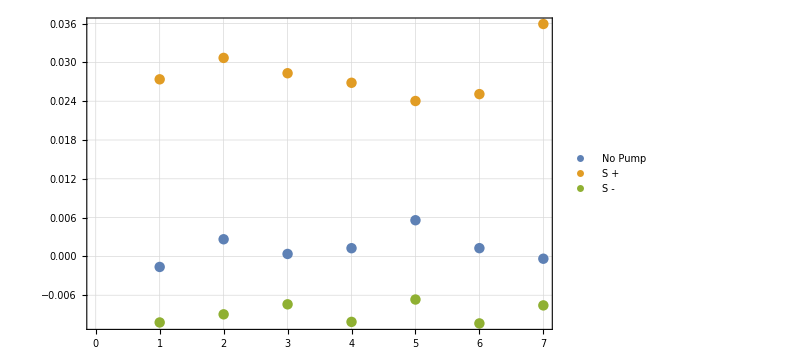

```mathematica
(* Plotting the P_3_s2 stokes parameter for all the runs.*)
ListPlot[val,PlotLegends->{"No Pump","S +","S -"}]
```

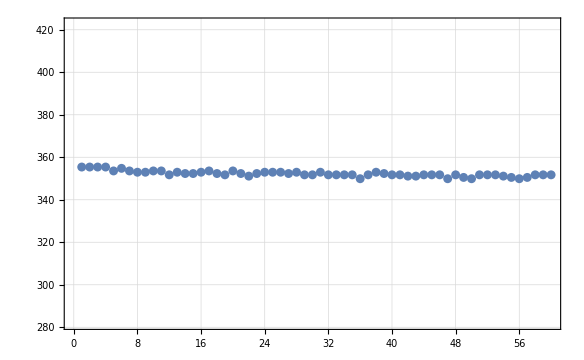

```mathematica
Dataset[data][[1]]["IndividualRunInfo"][All,"currentPlot"][[1]]
```

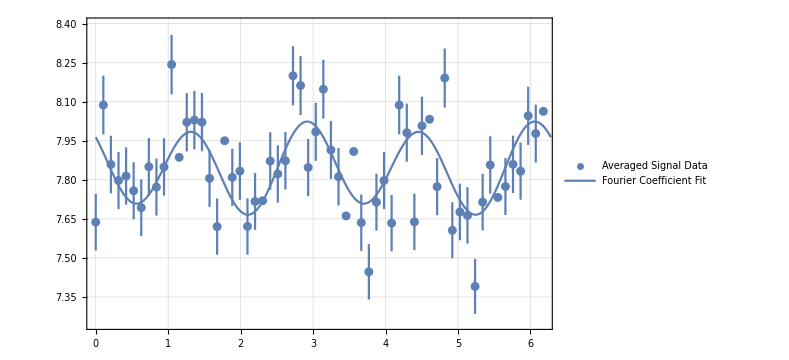

```mathematica
ProcessElectronPolarizationFile[fn[[16]]]["fourierFit"]
```

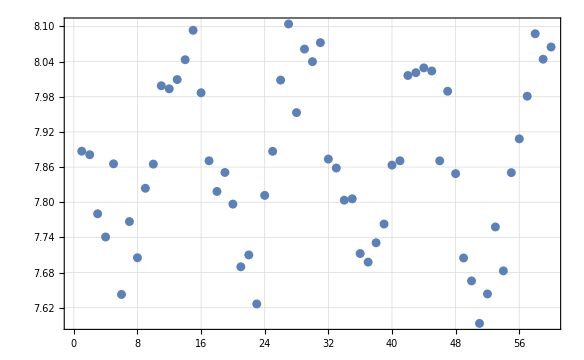

```mathematica
Dataset[data][[1]]["AllRunsPlot"]
```

```mathematica
SetDirectory[FileNameJoin[{$PACKAGES,"sampleData","polarization","averageData"}]]

fn=FileNames[RegularExpression["POL.*_[0-9]*.dat"]]

startFile=1;
repeatRuns=7;
typesOfRuns={"none","s+","s-"};
typesOfRuns2={"30 eV"};
data2=<||>;
For[i=1,i<=Length[typesOfRuns],i++,
For[j=1,j≤Length[typesOfRuns2],j++,
firstFileUniqueType=startFile+(i-1)+Length[typesOfRuns]*(j-1);
lastFile=startFile+repeatRuns*Length[typesOfRuns]*Length[typesOfRuns2]-1;
uniqueFileTypeRepeatRate=Length[typesOfRuns]*Length[typesOfRuns2];

dat=CalculateAverageStokesFromFilenames[Take[fn,{firstFileUniqueType,lastFile,uniqueFileTypeRepeatRate}]];
PrependTo[dat,<|"pump"->typesOfRuns[[i]],"E_i"->typesOfRuns2[[j]]|>];
datalineIdentifier= ExtractTimeStringFromFileNameString[dat["File"]]<>":"<>typesOfRuns[[i]]<>", "<>typesOfRuns2[[j]];
	AppendTo[data2,datalineIdentifier->dat];
];
];
```

C:\Users\kahrendsen2\Box Sync\Research\mathematicaRb\packages\sampleData\polarization\averageData

{POL2019-03-15_184016.dat,POL2019-03-15_184132.dat,POL2019-03-15_184246.dat,POL2019-03-15_184409.dat,POL2019-03-15_184523.dat,POL2019-03-15_184637.dat,POL2019-03-15_184803.dat,POL2019-03-15_184917.dat,POL2019-03-15_185031.dat,POL2019-03-15_185205.dat,POL2019-03-15_185319.dat,POL2019-03-15_185433.dat,POL2019-03-15_185558.dat,POL2019-03-15_185712.dat,POL2019-03-15_185826.dat,POL2019-03-15_185955.dat,POL2019-03-15_190109.dat,POL2019-03-15_190223.dat,POL2019-03-15_190359.dat,POL2019-03-15_190513.dat,POL2019-03-15_190627.dat,POL2019-03-15_190750.dat,POL2019-03-15_190904.dat,POL2019-03-15_191018.dat,POL2019-03-15_191144.dat,POL2019-03-15_191258.dat,POL2019-03-15_191412.dat,POL2019-03-15_191542.dat,POL2019-03-15_191657.dat,POL2019-03-15_191811.dat,POL2019-03-15_191937.dat,POL2019-03-15_192051.dat,POL2019-03-15_192205.dat,POL2019-03-15_192330.dat,POL2019-03-15_192444.dat,POL2019-03-15_192558.dat}

ToExpression::sntxi: Incomplete expression; more input is needed .

General::stop: Further output of ToExpression::sntxi will be suppressed during this calculation.

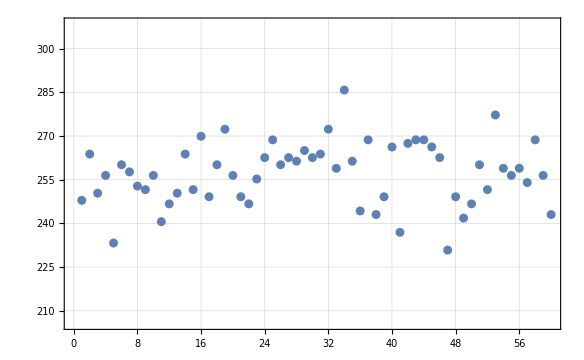

```mathematica
Dataset[data2][[1]]["IndividualRunInfo"][All,"currentPlot"][[2]]
```

```mathematica
SetDirectory[FileNameJoin[{$DATARUNS,"2019-03-06","data","noBGP"}]]
```

/home/karl/Box Sync/Research/DataRuns/2019-03-06/data/noBGP

```mathematica
startFile=1;
repeatRuns=1;
typesOfRuns={"none"};
typesOfRuns2={"30 eV"};
data=<||>;
For[i=1,i<=Length[typesOfRuns],i++,
For[j=1,j≤Length[typesOfRuns2],j++,
firstFileUniqueType=startFile+(i-1)+Length[typesOfRuns]*(j-1);
lastFile=startFile+repeatRuns*Length[typesOfRuns]*Length[typesOfRuns2]-1;
uniqueFileTypeRepeatRate=Length[typesOfRuns]*Length[typesOfRuns2];

dat=CalculateAverageStokesFromFilenames[Take[fn,{firstFileUniqueType,lastFile,uniqueFileTypeRepeatRate}]];
PrependTo[dat,<|"pump"->typesOfRuns[[i]],"E_i"->typesOfRuns2[[j]]|>];
datalineIdentifier= ExtractTimeStringFromFileNameString[dat["File"]]<>":"<>typesOfRuns[[i]]<>", "<>typesOfRuns2[[j]];
	AppendTo[data,datalineIdentifier->dat];
];
];
```

# Possible Improvements

```mathematica
Normal/@Through[ImportFile[aout1][[All,2]][All,"COUNT"]]
```

ToExpression::sntxi: Incomplete expression; more input is needed .

General::stop: Further output of ToExpression::sntxi will be suppressed during this calculation.

{{3302,3440,3255,3380,3242,3250,3204,3355,3244,3255,3257,3372,3372,3394,3356,3323,3220,3258,3266,3261,3349,3306,3263,3364,3455,3378,3551,3464,3407,3574,3474,3327,3490,3393,3363,3333,3347,3447,3400,3392,3507,3483,3541,3593,3439,3442,3494,3408,3406,3459,3343,3467,3364,3414,3418,3546,3430,3567,3366,3551},{3359,3261,3278,3366,3218,3214,3272,3208,3219,3249,3262,3310,3206,3145,3274,3143,3160,3093,3041,3016,3068,2961,3097,3007,3081,3104,3022,3110,3210,3251,3144,3257,3228,3123,3136,3176,3153,3181,3199,3230,3061,3171,3068,3226,3183,3119,3110,3125,3026,3136,3242,3255,3291,3468,3493,3465,3629,3697,3795,3798},{3934,3898,3777,3881,3901,3845,3786,3849,3853,3779,3848,3758,3897,3878,3924,3835,3829,3796,3734,3598,3672,3648,3692,3729,3749,3711,3710,3731,3726,3840,3723,3664,3616,3564,3734,3557,3534,3484,3485,3686,3623,3724,3669,3694,3749,3680,3589,3603,3600,3533,3543,3499,3618,3678,3641,3599,3642,3600,3694,3743},{3756,3788,3686,3793,3700,3706,3683,3773,3645,3784,3858,3833,3996,3852,3946,3812,3727,3836,3745,3672,3805,3757,3790,3901,3845,3849,4028,4128,3961,3996,3918,3916,3886,3950,3983,3714,3814,3827,3765,3866,3850,3844,3778,3781,3832,3820,3813,3722,3746,3695,3648,3664,3629,3618,3668,3717,3806,3878,3712,3838},{3529,3668,3497,3480,3579,3521,3529,3444,3425,3468,3497,3546,3538,3534,3419,3454,3456,3393,3302,3337,3262,3258,3175,3319,3446,3400,3372,3387,3522,3578,3444,3439,3379,3421,3359,3442,3532,3391,3482,3307,3477,3423,3469,3417,3424,3348,3373,3296,3229,3219,3263,3219,3297,3316,3290,3378,3405,3560,3481,3595},{3440,3393,3454,3378,3450,3414,3365,3280,3386,3379,3411,3378,3474,3421,3447,3444,3343,3492,3297,3374,3402,3343,3343,3469,3564,3440,3317,3405,3451,3426,3461,3316,3340,3254,3260,3220,3222,3270,3394,3284,3377,3398,3420,3546,3368,3394,3286,3404,3277,3294,3291,3276,3301,3396,3485,3367,3458,3494,3442,3415},{3807,3694,3743,3663,3678,3668,3692,3701,3653,3742,3774,3883,3739,3806,3823,3689,3810,3715,3611,3594,3538,3656,3585,3707,3695,3927,3798,3893,3787,3951,3838,3819,3799,3724,3763,3837,3801,3663,3730,3803,3849,3902,3755,3854,3813,3814,3715,3657,3686,3646,3620,3550,3735,3643,3589,3523,3740,3754,3566,3643},{3389,3341,3393,3320,3456,3441,3349,3407,3396,3358,3343,3406,3292,3397,3420,3356,3289,3268,3102,3086,3123,3123,3064,3255,3303,3244,3306,3328,3397,3346,3419,3435,3461,3425,3428,3295,3369,3457,3338,3332,3452,3405,3501,3533,3320,3475,3269,3433,3292,3273,3289,3245,3397,3431,3404,3557,3396,3611,3609,3685},{3734,3637,3833,3723,3756,3811,3765,3681,3784,3697,3793,3884,3803,3885,3847,3828,3939,3804,3763,3721,3760,3667,3701,3769,3783,3807,3852,3879,3913,3831,3917,3674,3913,3709,3802,3612,3595,3612,3589,3664,3722,3803,3754,3797,3631,3824,3609,3652,3574,3656,3606,3686,3647,3766,3637,3797,3800,3717,3702,3706},{3447,3423,3457,3451,3406,3341,3444,3435,3505,3519,3628,3554,3541,3538,3605,3653,3488,3399,3346,3355,3312,3353,3238,3344,3411,3311,3520,3520,3456,3558,3542,3424,3465,3508,3437,3541,3539,3470,3569,3590,3687,3618,3581,3756,3501,3816,3557,3548,3498,3545,3596,3482,3501,3474,3613,3677,3674,3640,3774,3581},{3320,3316,3323,3409,3294,3161,3240,3221,3254,3240,3159,3167,3265,3172,3126,3121,2906,2966,2988,3070,2884,2863,2937,2917,3021,3009,2998,3081,2948,3064,2950,2974,3034,2843,2960,2917,2918,2797,2879,2954,2869,2893,2866,2925,2844,2849,2792,2768,2657,2622,2685,2786,2667,2673,2785,2895,2824,2913,2896,2903},{2822,2875,2863,2984,2970,2742,2861,2855,2982,3019,3011,2949,3053,3019,3066,3089,3021,2997,3020,2898,2943,2939,2899,3189,3088,3097,2988,3076,3103,3076,3081,2939,2881,2891,2796,2745,2753,2768,2940,2969,2982,2924,2967,2976,2865,2991,2988,2822,2823,2829,2904,2806,2831,2873,2766,2792,2943,2867,2955,2849},{3011,3014,2980,3004,2927,2864,2934,2918,2992,2931,2927,3059,3050,3072,3004,2986,2857,2939,2950,2965,2916,2860,2856,3044,3046,3004,3217,3099,3174,3115,3095,3118,3099,2990,3164,3050,2977,3133,3084,3131,3166,3104,3160,3256,3081,3188,3176,3147,3128,3100,3134,3122,3159,3182,3093,3300,3254,3204,3188,3215},{3173,3164,3027,3093,3050,3000,3043,3109,3054,3195,3126,3198,3137,3122,3074,3209,3068,3042,2997,2955,2891,2960,2948,2945,3053,3215,3129,3258,3246,3264,3193,3195,3242,3217,3232,3298,3220,3363,3230,3308,3456,3312,3303,3403,3345,3375,3249,3289,3260,3247,3109,3084,3183,3175,3261,3271,3367,3340,3497,3551},{3524,3367,3385,3410,3311,3299,3309,3351,3506,3453,3498,3492,3623,3410,3478,3522,3338,3441,3359,3347,3338,3375,3311,3294,3326,3408,3368,3305,3294,3351,3177,3180,3130,3131,3116,3033,2994,3049,3003,3084,3129,3090,3093,3173,3143,3170,3093,2963,3038,3108,2949,2937,2891,2935,2924,3014,3042,3060,3042,2978},{2994,2915,2956,3012,2798,2873,2839,2903,2921,3013,2964,3033,3002,3065,3125,3024,3013,2833,2914,2968,2957,2897,2946,2895,3100,3013,3091,3196,3068,3072,3095,3152,3087,3091,3050,2942,2888,3027,3049,3095,3064,3123,3130,3124,3167,3031,3019,2949,2967,2939,3034,2986,2919,2871,3041,3017,3031,3103,2971,2898},{2850,2783,2727,2744,2738,2837,2752,2790,2720,2797,2835,2822,2823,2855,2807,2719,2686,2646,2575,2606,2643,2631,2580,2662,2728,2684,2701,2755,2746,2823,2823,2777,2712,2739,2775,2761,2732,2780,2721,2871,2838,2780,2744,2702,2817,2740,2769,2734,2743,2734,2773,2733,2779,2740,2781,2791,2939,2768,2931,2884},{2828,2951,2807,2799,2731,2751,2876,2859,2738,2823,2878,2920,2981,2953,3018,2971,2949,2888,2896,2901,2825,2901,2808,2848,2930,2872,2983,2945,2980,2890,2894,2861,3010,2837,2748,2881,2901,2836,2866,2962,2903,2984,2973,2956,2979,2837,3055,2964,2931,2847,2819,2846,2881,2914,2935,3031,3035,3052,2893,3024}}

# Switching Default Processing

```mathematica
fn=gasOn
	results=<||>;
	f=ImportFile[fn];

	signals={};
	fileNames={};
	For[i=1,i<=Length[f],i++,
		header=f[[i]][[1]];
		dataset=f[[i]][[2]];
		counts=Normal[dataset[All,"COUNT"]];
		current=Abs[Normal[dataset[All,"CURRENT"]]]*10^(-header["SCALE"])/nA;
		dwellTime=header["DWELL(s)"];
		signal=NormalizePolarizationData[counts,current,dwellTime];
		AppendTo[signals,signal];
		AppendTo[fileNames,header["File"]];
	];
	AppendTo[results,"averagedFiles"->fn];

	signal=Mean[signals];
	AppendTo[results,"signal"->signal];
	signalStdm=StandardDeviation[signals]/Sqrt[Length[signals]];
	AppendTo[results,"signalStdm"->signalStdm];

	AppendTo[results,ProcessElectronPolarizationFromSignal[signal,signalStdm]]
```

gasOn

Import::chtype: First argument gasOn is not a valid file, directory, or URL specification.

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

StringPart::strse: String or list of strings expected at position 1 in StringPart[$Failed,1].

Import::chtype: First argument gasOn is not a valid file, directory, or URL specification.

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

StringPart::strse: String or list of strings expected at position 1 in StringPart[$Failed,1].

Take::normal: Nonatomic expression expected at position 1 in Take[$Failed,{1,-1},All].

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partw: Part 1 of <||> does not exist.

Part::partw: Part 2 of <||> does not exist.

Append::invdt: The argument … is not a rule or a list of rules.

Append[<|averagedFiles→gasOn,signal→1/2 (NormalizePolarizationData[Failure[…][All,COUNT],10^(9-Missing[KeyAbsent,SCALE]) Abs[Failure[…][All,CURRENT]],Missing[KeyAbsent,DWELL(s)]]+NormalizePolarizationData[<||>⟦2⟧[All,COUNT],10^(9-<||>⟦1⟧[SCALE]) Abs[<||>⟦2⟧[All,CURRENT]],<||>⟦1⟧[DWELL(s)]]),signalStdm→1/2 √((-Conjugate[NormalizePolarizationData[Failure[…][All,COUNT],10^(9-Missing[KeyAbsent,SCALE]) Abs[Failure[…][All,CURRENT]],Missing[KeyAbsent,DWELL(s)]]]+Conjugate[NormalizePolarizationData[<||>⟦2⟧[All,COUNT],10^(9-<||>⟦1⟧[SCALE]) Abs[<||>⟦2⟧[All,CURRENT]],<||>⟦1⟧[DWELL(s)]]]) (-NormalizePolarizationData[Failure[…][All,COUNT],10^(9-Missing[KeyAbsent,SCALE]) Abs[Failure[…][All,CURRENT]],Missing[KeyAbsent,DWELL(s)]]+NormalizePolarizationData[<||>⟦2⟧[All,COUNT],10^(9-<||>⟦1⟧[SCALE]) Abs[<||>⟦2⟧[All,CURRENT]],<||>⟦1⟧[DWELL(s)]]))|>,ProcessElectronPolarizationFromSignal[1/2 (NormalizePolarizationData[Failure[…][All,COUNT],10^(9-Missing[KeyAbsent,SCALE]) Abs[Failure[…][All,CURRENT]],Missing[KeyAbsent,DWELL(s)]]+NormalizePolarizationData[<||>⟦2⟧[All,COUNT],10^(9-<||>⟦1⟧[SCALE]) Abs[<||>⟦2⟧[All,CURRENT]],<||>⟦1⟧[DWELL(s)]]),1/2 √((-Conjugate[NormalizePolarizationData[Failure[…][All,COUNT],10^(9-Missing[KeyAbsent,SCALE]) Abs[Failure[…][All,CURRENT]],Missing[KeyAbsent,DWELL(s)]]]+Conjugate[NormalizePolarizationData[<||>⟦2⟧[All,COUNT],10^(9-<||>⟦1⟧[SCALE]) Abs[<||>⟦2⟧[All,CURRENT]],<||>⟦1⟧[DWELL(s)]]]) (-NormalizePolarizationData[Failure[…][All,COUNT],10^(9-Missing[KeyAbsent,SCALE]) Abs[Failure[…][All,CURRENT]],Missing[KeyAbsent,DWELL(s)]]+NormalizePolarizationData[<||>⟦2⟧[All,COUNT],10^(9-<||>⟦1⟧[SCALE]) Abs[<||>⟦2⟧[All,CURRENT]],<||>⟦1⟧[DWELL(s)]]))]]

```mathematica
StandardDeviation[signals[[All,1]]]
```

2.11391

```mathematica
(* The new Default average processing *)
```

```mathematica
fn=Take[fnHold,{1,-1,12}]
```

{POL2019-03-20_215112.dat,POL2019-03-20_220642.dat,POL2019-03-20_222209.dat,POL2019-03-20_223752.dat,POL2019-03-20_225319.dat}

```mathematica
f=ImportFile[fn];
	results=<||>;
signals={};
	datasets={};
	currents={};
	fileNames={};
	For[i=1,i<=Length[f],i++,
		header=f[[i]][[1]];
		dataset=f[[i]][[2]];
		AppendTo[datasets,Normal[dataset]];
		counts=Normal[dataset[All,"COUNT"]];
		current=Abs[Normal[dataset[All,"CURRENT"]]]*10^(-header["SCALE"])/nA;
		AppendTo[currents,RepeatedMeasurementSummary[current]];
		dwellTime=header["DWELL(s)"];
		signal=GetCurrentNormalizedCountRate[counts,current,dwellTime];
		AppendTo[signals,signal];
		AppendTo[fileNames,header["File"]];
	];
	AppendTo[results,"averagedFiles"->fn];
	
	singleRunInfo=Transpose[{signals,datasets}];
	threader[arg_]:=AssociationThread[{"signal","dataset"},arg];
	singleRunInfo=AssociationThread[fn,Map[threader,singleRunInfo]];
	For[i=1,i≤Length[singleRunInfo],i++,
	AppendTo[singleRunInfo[[i]],currents[[i]]];
	];

	signal=Mean[signals];
	AppendTo[results,"avgSignal"->signal];
	signalStdm=StandardDeviation[signals]/Sqrt[Length[signals]];
	AppendTo[results,"error"->signalStdm];
	
	AppendTo[results,"IndividualRunInfo"->singleRunInfo];
```

```mathematica
For[i=1,i≤Length[singleRunInfo],i++,
AppendTo[singleRunInfo[[i]],currents[[i]]];
];
```

```mathematica
Dataset[singleRunInfo][All,"currentPlot"]
```

Dataset[<>]

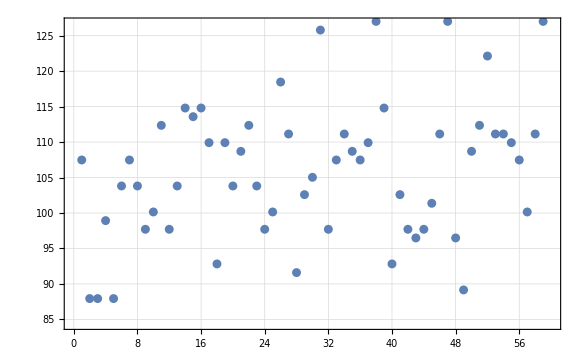
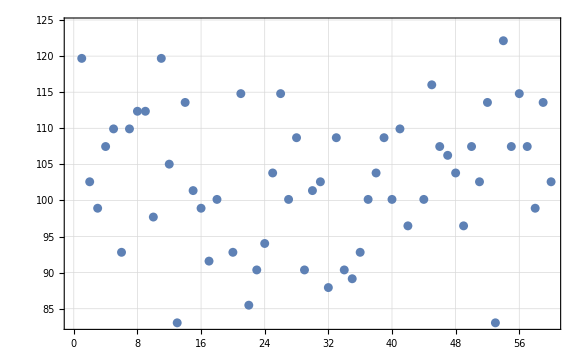
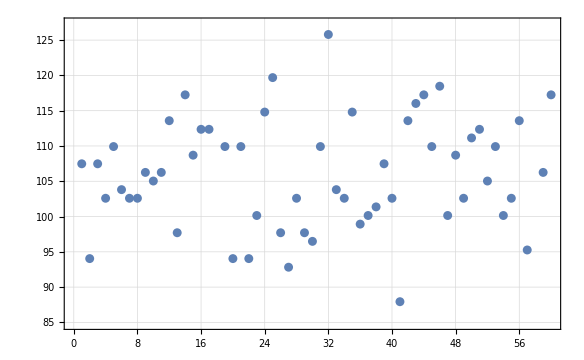
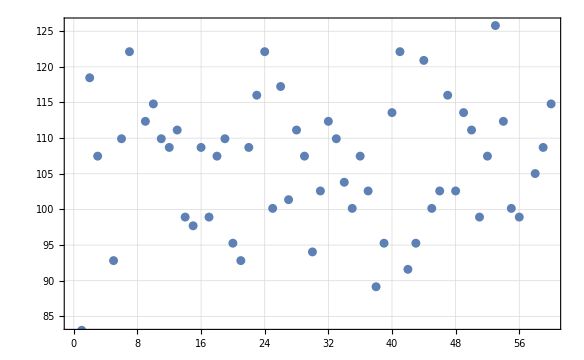
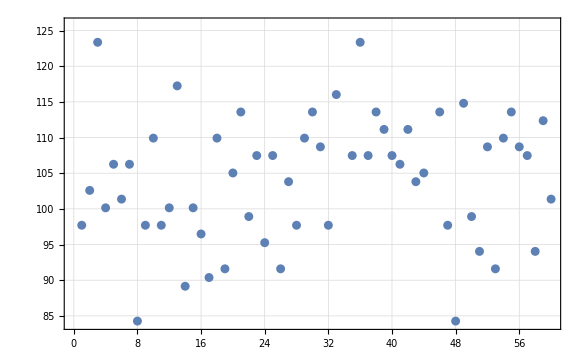
{{<|signal→{15.5479,19.401,18.6732,16.3659,19.0144,15.9136,14.8687,15.6728,16.8366,16.6756,15.0766,18.0648,16.5494,15.5746,15.4075,14.8429,15.1114,17.7012,14.5382,15.9232,16.376,14.8185,15.9136,17.8498,16.8253,14.3586,16.52,19.1272,17.5067,16.1951,14.5794,17.5633,15.6503,15.6382,16.33,15.6596,15.5299,13.5968,14.8081,17.5719,16.5027,17.3893,17.8685,17.2971,16.8692,15.5482,13.337,17.7959,19.5727,15.9344,14.3735,13.7722,15.2243,14.9183,15.6846,16.59,17.2946,15.8901,13.3921,22.4177}|>,<|dataset→{<|STEP→0,COUNT→1685,CURRENT→-0.107474,CURRENTsd→0.079755,ANGLE→0.|>,<|STEP→20,COUNT→1720,CURRENT→-0.0879336,CURRENTsd→-0.1,ANGLE→0.10472|>,<|STEP→40,COUNT→1656,CURRENT→-0.0879336,CURRENTsd→-0.09434,ANGLE→0.20944|>,<|STEP→60,COUNT→1633,CURRENT→-0.0989253,CURRENTsd→0.0125,ANGLE→0.314159|>,<|STEP→80,COUNT→1686,CURRENT→-0.0879336,CURRENTsd→-0.1,ANGLE→0.418879|>,<|STEP→100,COUNT→1666,CURRENT→-0.103811,CURRENTsd→0.075949,ANGLE→0.523599|>,<|STEP→120,COUNT→1612,CURRENT→-0.107474,CURRENTsd→0.005714,ANGLE→0.628319|>,<|STEP→140,COUNT→1641,CURRENT→-0.103811,CURRENTsd→0.005917,ANGLE→0.733038|>,<|STEP→160,COUNT→1659,CURRENT→-0.097704,CURRENTsd→-0.02439,ANGLE→0.837758|>,<|STEP→180,COUNT→1684,CURRENT→-0.100147,CURRENTsd→0.018634,ANGLE→0.942478|>,<|STEP→200,COUNT→1708,CURRENT→-0.11236,CURRENTsd→0.057471,ANGLE→1.0472|>,<|STEP→220,COUNT→1779,CURRENT→-0.097704,CURRENTsd→0.118881,ANGLE→1.15192|>,<|STEP→240,COUNT→1732,CURRENT→-0.103811,CURRENTsd→0.089744,ANGLE→1.25664|>,<|STEP→260,COUNT→1802,CURRENT→-0.114802,CURRENTsd→0.010753,ANGLE→1.36136|>,<|STEP→280,COUNT→1764,CURRENT→-0.113581,CURRENTsd→0.033333,ANGLE→1.46608|>,<|STEP→300,COUNT→1718,CURRENT→-0.114802,CURRENTsd→-0.020833,ANGLE→1.5708|>,<|STEP→320,COUNT→1675,CURRENT→-0.109917,CURRENTsd→-0.010989,ANGLE→1.67552|>,<|STEP→340,COUNT→1657,CURRENT→-0.0928188,CURRENTsd→-0.100592,ANGLE→1.78024|>,<|STEP→360,COUNT→1612,CURRENT→-0.109917,CURRENTsd→0.058824,ANGLE→1.88496|>,<|STEP→380,COUNT→1667,CURRENT→-0.103811,CURRENTsd→-0.071038,ANGLE→1.98968|>,<|STEP→400,COUNT→1794,CURRENT→-0.108696,CURRENTsd→0.028902,ANGLE→2.0944|>,<|STEP→420,COUNT→1679,CURRENT→-0.11236,CURRENTsd→0.010989,ANGLE→2.19912|>,<|STEP→440,COUNT→1666,CURRENT→-0.103811,CURRENTsd→0.005917,ANGLE→2.30384|>,<|STEP→460,COUNT→1758,CURRENT→-0.097704,CURRENTsd→-0.012346,ANGLE→2.40855|>,<|STEP→480,COUNT→1699,CURRENT→-0.100147,CURRENTsd→-0.052023,ANGLE→2.51327|>,<|STEP→500,COUNT→1715,CURRENT→-0.118466,CURRENTsd→0.054348,ANGLE→2.61799|>,<|STEP→520,COUNT→1850,CURRENT→-0.111138,CURRENTsd→-0.071429,ANGLE→2.72271|>,<|STEP→540,COUNT→1766,CURRENT→-0.0915975,CURRENTsd→-0.117647,ANGLE→2.82743|>,<|STEP→560,COUNT→1810,CURRENT→-0.102589,CURRENTsd→0.030675,ANGLE→2.93215|>,<|STEP→580,COUNT→1715,CURRENT→-0.105032,CURRENTsd→0.,ANGLE→3.03687|>,<|STEP→600,COUNT→1848,CURRENT→-0.125794,CURRENTsd→-0.004831,ANGLE→3.14159|>,<|STEP→620,COUNT→1730,CURRENT→-0.097704,CURRENTsd→-0.02439,ANGLE→3.24631|>,<|STEP→640,COUNT→1696,CURRENT→-0.107474,CURRENTsd→0.,ANGLE→3.35103|>,<|STEP→660,COUNT→1752,CURRENT→-0.111138,CURRENTsd→0.05814,ANGLE→3.45575|>,<|STEP→680,COUNT→1789,CURRENT→-0.108696,CURRENTsd→0.085366,ANGLE→3.56047|>,<|STEP→700,COUNT→1697,CURRENT→-0.107474,CURRENTsd→0.053892,ANGLE→3.66519|>,<|STEP→720,COUNT→1721,CURRENT→-0.109917,CURRENTsd→0.058824,ANGLE→3.76991|>,<|STEP→740,COUNT→1741,CURRENT→-0.127015,CURRENTsd→0.066667,ANGLE→3.87463|>,<|STEP→760,COUNT→1714,CURRENT→-0.114802,CURRENTsd→0.005348,ANGLE→3.97935|>,<|STEP→780,COUNT→1645,CURRENT→-0.0928188,CURRENTsd→-0.012987,ANGLE→4.08407|>,<|STEP→800,COUNT→1707,CURRENT→-0.102589,CURRENTsd→-0.061453,ANGLE→4.18879|>,<|STEP→820,COUNT→1713,CURRENT→-0.097704,CURRENTsd→-0.058824,ANGLE→4.29351|>,<|STEP→840,COUNT→1738,CURRENT→-0.0964827,CURRENTsd→-0.070588,ANGLE→4.39823|>,<|STEP→860,COUNT→1704,CURRENT→-0.097704,CURRENTsd→-0.075145,ANGLE→4.50295|>,<|STEP→880,COUNT→1724,CURRENT→-0.101368,CURRENTsd→-0.017751,ANGLE→4.60767|>,<|STEP→900,COUNT→1742,CURRENT→-0.111138,CURRENTsd→-0.026738,ANGLE→4.71239|>,<|STEP→920,COUNT→1708,CURRENT→-0.127015,CURRENTsd→0.045226,ANGLE→4.81711|>,<|STEP→940,COUNT→1731,CURRENT→-0.0964827,CURRENTsd→-0.018634,ANGLE→4.92183|>,<|STEP→960,COUNT→1759,CURRENT→-0.0891549,CURRENTsd→-0.070064,ANGLE→5.02655|>,<|STEP→980,COUNT→1746,CURRENT→-0.108696,CURRENTsd→-0.027322,ANGLE→5.13127|>,<|STEP→1000,COUNT→1629,CURRENT→-0.11236,CURRENTsd→0.121951,ANGLE→5.23599|>,<|STEP→1020,COUNT→1696,CURRENT→-0.12213,CURRENTsd→0.111111,ANGLE→5.34071|>,<|STEP→1040,COUNT→1706,CURRENT→-0.111138,CURRENTsd→0.005525,ANGLE→5.44543|>,<|STEP→1060,COUNT→1672,CURRENT→-0.111138,CURRENTsd→0.01676,ANGLE→5.55015|>,<|STEP→1080,COUNT→1738,CURRENT→-0.109917,CURRENTsd→-0.081633,ANGLE→5.65487|>,<|STEP→1100,COUNT→1797,CURRENT→-0.107474,CURRENTsd→-0.038251,ANGLE→5.75959|>,<|STEP→1120,COUNT→1746,CURRENT→-0.100147,CURRENTsd→-0.012048,ANGLE→5.86431|>,<|STEP→1140,COUNT→1780,CURRENT→-0.111138,CURRENTsd→0.011111,ANGLE→5.96903|>,<|STEP→1160,COUNT→1715,CURRENT→-0.127015,CURRENTsd→0.055838,ANGLE→6.07375|>,<|STEP→1180,COUNT→1821,CURRENT→-0.0806058,CURRENTsd→-0.175,ANGLE→6.17847|>}|>,<|currentPlot→-Graphics-,currentAvg→105.541,currentStd→10.1369|>},{<|signal→{14.7133,17.1655,16.7601,15.7433,14.8658,17.2918,14.3017,15.4148,14.8363,16.898,13.8444,16.1094,19.9522,14.6415,16.7903,15.9312,17.9372,16.5857,12.8331,18.2183,14.4074,18.7505,18.2017,17.4713,16.1255,14.0677,16.4059,15.4284,19.2086,16.5832,16.7172,19.6171,14.4992,17.8034,18.1818,17.615,15.7769,15.6535,14.6372,16.6356,15.5208,17.8063,13.3213,16.9751,14.2557,15.6596,15.5572,15.8654,17.0393,15.1478,16.6587,14.4743,20.4941,13.8623,16.041,15.052,15.7805,18.3674,14.8088,17.0096}|>,<|dataset→{<|STEP→0,COUNT→1775,CURRENT→-0.119687,CURRENTsd→0.076923,ANGLE→0.|>,<|STEP→20,COUNT→1775,CURRENT→-0.102589,CURRENTsd→0.012048,ANGLE→0.10472|>,<|STEP→40,COUNT→1672,CURRENT→-0.0989253,CURRENTsd→-0.074286,ANGLE→0.20944|>,<|STEP→60,COUNT→1706,CURRENT→-0.107474,CURRENTsd→0.157895,ANGLE→0.314159|>,<|STEP→80,COUNT→1648,CURRENT→-0.109917,CURRENTsd→0.005587,ANGLE→0.418879|>,<|STEP→100,COUNT→1619,CURRENT→-0.0928188,CURRENTsd→-0.037975,ANGLE→0.523599|>,<|STEP→120,COUNT→1586,CURRENT→-0.109917,CURRENTsd→-0.037433,ANGLE→0.628319|>,<|STEP→140,COUNT→1746,CURRENT→-0.11236,CURRENTsd→-0.026455,ANGLE→0.733038|>,<|STEP→160,COUNT→1681,CURRENT→-0.11236,CURRENTsd→0.010989,ANGLE→0.837758|>,<|STEP→180,COUNT→1665,CURRENT→-0.097704,CURRENTsd→-0.058824,ANGLE→0.942478|>,<|STEP→200,COUNT→1671,CURRENT→-0.119687,CURRENTsd→0.082873,ANGLE→1.0472|>,<|STEP→220,COUNT→1706,CURRENT→-0.105032,CURRENTsd→-0.033708,ANGLE→1.15192|>,<|STEP→240,COUNT→1671,CURRENT→-0.0830484,CURRENTsd→-0.028571,ANGLE→1.25664|>,<|STEP→260,COUNT→1677,CURRENT→-0.113581,CURRENTsd→-0.021053,ANGLE→1.36136|>,<|STEP→280,COUNT→1716,CURRENT→-0.101368,CURRENTsd→-0.082873,ANGLE→1.46608|>,<|STEP→300,COUNT→1590,CURRENT→-0.0989253,CURRENTsd→0.031847,ANGLE→1.5708|>,<|STEP→320,COUNT→1657,CURRENT→-0.0915975,CURRENTsd→-0.056604,ANGLE→1.67552|>,<|STEP→340,COUNT→1675,CURRENT→-0.100147,CURRENTsd→0.006135,ANGLE→1.78024|>,<|STEP→360,COUNT→1644,CURRENT→-0.127015,CURRENTsd→0.083333,ANGLE→1.88496|>,<|STEP→380,COUNT→1705,CURRENT→-0.0928188,CURRENTsd→0.006623,ANGLE→1.98968|>,<|STEP→400,COUNT→1668,CURRENT→-0.114802,CURRENTsd→0.05618,ANGLE→2.0944|>,<|STEP→420,COUNT→1617,CURRENT→-0.085491,CURRENTsd→-0.10828,ANGLE→2.19912|>,<|STEP→440,COUNT→1659,CURRENT→-0.0903762,CURRENTsd→-0.10303,ANGLE→2.30384|>,<|STEP→460,COUNT→1657,CURRENT→-0.0940401,CURRENTsd→-0.072289,ANGLE→2.40855|>,<|STEP→480,COUNT→1688,CURRENT→-0.103811,CURRENTsd→0.017964,ANGLE→2.51327|>,<|STEP→500,COUNT→1629,CURRENT→-0.114802,CURRENTsd→0.005348,ANGLE→2.61799|>,<|STEP→520,COUNT→1657,CURRENT→-0.100147,CURRENTsd→0.037975,ANGLE→2.72271|>,<|STEP→540,COUNT→1691,CURRENT→-0.108696,CURRENTsd→0.053254,ANGLE→2.82743|>,<|STEP→560,COUNT→1750,CURRENT→-0.0903762,CURRENTsd→-0.080745,ANGLE→2.93215|>,<|STEP→580,COUNT→1695,CURRENT→-0.101368,CURRENTsd→0.012195,ANGLE→3.03687|>,<|STEP→600,COUNT→1729,CURRENT→-0.102589,CURRENTsd→-0.050847,ANGLE→3.14159|>,<|STEP→620,COUNT→1739,CURRENT→-0.0879336,CURRENTsd→-0.082803,ANGLE→3.24631|>,<|STEP→640,COUNT→1590,CURRENT→-0.108696,CURRENTsd→-0.011111,ANGLE→3.35103|>,<|STEP→660,COUNT→1623,CURRENT→-0.0903762,CURRENTsd→-0.092025,ANGLE→3.45575|>,<|STEP→680,COUNT→1635,CURRENT→-0.0891549,CURRENTsd→-0.033113,ANGLE→3.56047|>,<|STEP→700,COUNT→1649,CURRENT→-0.0928188,CURRENTsd→-0.08982,ANGLE→3.66519|>,<|STEP→720,COUNT→1594,CURRENT→-0.100147,CURRENTsd→-0.103825,ANGLE→3.76991|>,<|STEP→740,COUNT→1639,CURRENT→-0.103811,CURRENTsd→0.096774,ANGLE→3.87463|>,<|STEP→760,COUNT→1605,CURRENT→-0.108696,CURRENTsd→0.00565,ANGLE→3.97935|>,<|STEP→780,COUNT→1680,CURRENT→-0.100147,CURRENTsd→-0.040936,ANGLE→4.08407|>,<|STEP→800,COUNT→1720,CURRENT→-0.109917,CURRENTsd→0.034483,ANGLE→4.18879|>,<|STEP→820,COUNT→1732,CURRENT→-0.0964827,CURRENTsd→-0.065089,ANGLE→4.29351|>,<|STEP→840,COUNT→1706,CURRENT→-0.127015,CURRENTsd→0.130435,ANGLE→4.39823|>,<|STEP→860,COUNT→1714,CURRENT→-0.100147,CURRENTsd→-0.068182,ANGLE→4.50295|>,<|STEP→880,COUNT→1668,CURRENT→-0.116024,CURRENTsd→0.049724,ANGLE→4.60767|>,<|STEP→900,COUNT→1697,CURRENT→-0.107474,CURRENTsd→-0.022222,ANGLE→4.71239|>,<|STEP→920,COUNT→1667,CURRENT→-0.106253,CURRENTsd→-0.04918,ANGLE→4.81711|>,<|STEP→940,COUNT→1661,CURRENT→-0.103811,CURRENTsd→0.0625,ANGLE→4.92183|>,<|STEP→960,COUNT→1658,CURRENT→-0.0964827,CURRENTsd→0.104895,ANGLE→5.02655|>,<|STEP→980,COUNT→1642,CURRENT→-0.107474,CURRENTsd→0.079755,ANGLE→5.13127|>,<|STEP→1000,COUNT→1723,CURRENT→-0.102589,CURRENTsd→0.,ANGLE→5.23599|>,<|STEP→1020,COUNT→1658,CURRENT→-0.113581,CURRENTsd→0.081395,ANGLE→5.34071|>,<|STEP→1040,COUNT→1716,CURRENT→-0.0830484,CURRENTsd→-0.195266,ANGLE→5.44543|>,<|STEP→1060,COUNT→1707,CURRENT→-0.12213,CURRENTsd→0.058201,ANGLE→5.55015|>,<|STEP→1080,COUNT→1738,CURRENT→-0.107474,CURRENTsd→-0.048649,ANGLE→5.65487|>,<|STEP→1100,COUNT→1742,CURRENT→-0.114802,CURRENTsd→-0.005291,ANGLE→5.75959|>,<|STEP→1120,COUNT→1710,CURRENT→-0.107474,CURRENTsd→-0.011236,ANGLE→5.86431|>,<|STEP→1140,COUNT→1831,CURRENT→-0.0989253,CURRENTsd→-0.018182,ANGLE→5.96903|>,<|STEP→1160,COUNT→1696,CURRENT→-0.113581,CURRENTsd→-0.055838,ANGLE→6.07375|>,<|STEP→1180,COUNT→1759,CURRENT→-0.102589,CURRENTsd→-0.023256,ANGLE→6.17847|>}|>,<|currentPlot→-Graphics-,currentAvg→103.709,currentStd→10.278|>},{<|signal→{16.1899,18.4177,15.7433,16.2103,15.0568,15.4031,15.8399,15.8009,15.3596,15.6334,16.0278,14.034,17.4711,14.4058,15.962,14.7384,15.1745,21.125,15.2479,17.0566,14.1561,17.6414,16.3261,14.2245,13.8277,16.4169,19.1125,15.7034,16.2532,18.5733,15.1478,13.3393,17.1081,16.0738,14.3203,17.1038,16.2761,16.7114,15.1757,16.8341,18.8779,15.0025,14.204,14.9431,16.0576,14.5443,15.8967,14.812,16.0251,15.1793,14.1065,15.6334,15.0113,17.075,16.5125,14.2013,18.4125,13.039,15.6231,14.4058}|>,<|dataset→{<|STEP→0,COUNT→1754,CURRENT→-0.107474,CURRENTsd→-0.068783,ANGLE→0.|>,<|STEP→20,COUNT→1746,CURRENT→-0.0940401,CURRENTsd→-0.060976,ANGLE→0.10472|>,<|STEP→40,COUNT→1706,CURRENT→-0.107474,CURRENTsd→0.035294,ANGLE→0.20944|>,<|STEP→60,COUNT→1677,CURRENT→-0.102589,CURRENTsd→-0.066667,ANGLE→0.314159|>,<|STEP→80,COUNT→1669,CURRENT→-0.109917,CURRENTsd→0.058824,ANGLE→0.418879|>,<|STEP→100,COUNT→1613,CURRENT→-0.103811,CURRENTsd→0.005917,ANGLE→0.523599|>,<|STEP→120,COUNT→1639,CURRENT→-0.102589,CURRENTsd→-0.066667,ANGLE→0.628319|>,<|STEP→140,COUNT→1635,CURRENT→-0.102589,CURRENTsd→-0.04,ANGLE→0.733038|>,<|STEP→160,COUNT→1646,CURRENT→-0.106253,CURRENTsd→0.048193,ANGLE→0.837758|>,<|STEP→180,COUNT→1656,CURRENT→-0.105032,CURRENTsd→0.042424,ANGLE→0.942478|>,<|STEP→200,COUNT→1717,CURRENT→-0.106253,CURRENTsd→-0.059459,ANGLE→1.0472|>,<|STEP→220,COUNT→1608,CURRENT→-0.113581,CURRENTsd→-0.05102,ANGLE→1.15192|>,<|STEP→240,COUNT→1721,CURRENT→-0.097704,CURRENTsd→-0.053254,ANGLE→1.25664|>,<|STEP→260,COUNT→1703,CURRENT→-0.117245,CURRENTsd→0.032258,ANGLE→1.36136|>,<|STEP→280,COUNT→1749,CURRENT→-0.108696,CURRENTsd→0.011364,ANGLE→1.46608|>,<|STEP→300,COUNT→1670,CURRENT→-0.11236,CURRENTsd→0.069767,ANGLE→1.5708|>,<|STEP→320,COUNT→1719,CURRENT→-0.11236,CURRENTsd→0.069767,ANGLE→1.67552|>,<|STEP→340,COUNT→1691,CURRENT→-0.0793845,CURRENTsd→-0.171975,ANGLE→1.78024|>,<|STEP→360,COUNT→1690,CURRENT→-0.109917,CURRENTsd→0.046512,ANGLE→1.88496|>,<|STEP→380,COUNT→1618,CURRENT→-0.0940401,CURRENTsd→-0.049383,ANGLE→1.98968|>,<|STEP→400,COUNT→1570,CURRENT→-0.109917,CURRENTsd→0.011236,ANGLE→2.0944|>,<|STEP→420,COUNT→1673,CURRENT→-0.0940401,CURRENTsd→-0.0375,ANGLE→2.19912|>,<|STEP→440,COUNT→1649,CURRENT→-0.100147,CURRENTsd→0.031447,ANGLE→2.30384|>,<|STEP→460,COUNT→1647,CURRENT→-0.114802,CURRENTsd→-0.005291,ANGLE→2.40855|>,<|STEP→480,COUNT→1669,CURRENT→-0.119687,CURRENTsd→0.026178,ANGLE→2.51327|>,<|STEP→500,COUNT→1618,CURRENT→-0.097704,CURRENTsd→0.038961,ANGLE→2.61799|>,<|STEP→520,COUNT→1788,CURRENT→-0.0928188,CURRENTsd→-0.073171,ANGLE→2.72271|>,<|STEP→540,COUNT→1625,CURRENT→-0.102589,CURRENTsd→0.,ANGLE→2.82743|>,<|STEP→560,COUNT→1602,CURRENT→-0.097704,CURRENTsd→-0.096045,ANGLE→2.93215|>,<|STEP→580,COUNT→1806,CURRENT→-0.0964827,CURRENTsd→-0.091954,ANGLE→3.03687|>,<|STEP→600,COUNT→1679,CURRENT→-0.109917,CURRENTsd→0.028571,ANGLE→3.14159|>,<|STEP→620,COUNT→1692,CURRENT→-0.125794,CURRENTsd→0.204678,ANGLE→3.24631|>,<|STEP→640,COUNT→1790,CURRENT→-0.103811,CURRENTsd→-0.071038,ANGLE→3.35103|>,<|STEP→660,COUNT→1663,CURRENT→-0.102589,CURRENTsd→-0.017544,ANGLE→3.45575|>,<|STEP→680,COUNT→1658,CURRENT→-0.114802,CURRENTsd→0.05618,ANGLE→3.56047|>,<|STEP→700,COUNT→1706,CURRENT→-0.0989253,CURRENTsd→-0.02994,ANGLE→3.66519|>,<|STEP→720,COUNT→1644,CURRENT→-0.100147,CURRENTsd→-0.035294,ANGLE→3.76991|>,<|STEP→740,COUNT→1708,CURRENT→-0.101368,CURRENTsd→-0.040462,ANGLE→3.87463|>,<|STEP→760,COUNT→1645,CURRENT→-0.107474,CURRENTsd→0.017341,ANGLE→3.97935|>,<|STEP→780,COUNT→1741,CURRENT→-0.102589,CURRENTsd→0.005988,ANGLE→4.08407|>,<|STEP→800,COUNT→1674,CURRENT→-0.0879336,CURRENTsd→-0.058824,ANGLE→4.18879|>,<|STEP→820,COUNT→1718,CURRENT→-0.113581,CURRENTsd→0.094118,ANGLE→4.29351|>,<|STEP→840,COUNT→1662,CURRENT→-0.116024,CURRENTsd→0.,ANGLE→4.39823|>,<|STEP→860,COUNT→1766,CURRENT→-0.117245,CURRENTsd→0.015873,ANGLE→4.50295|>,<|STEP→880,COUNT→1779,CURRENT→-0.109917,CURRENTsd→0.139241,ANGLE→4.60767|>,<|STEP→900,COUNT→1737,CURRENT→-0.118466,CURRENTsd→0.015707,ANGLE→4.71239|>,<|STEP→920,COUNT→1606,CURRENT→-0.100147,CURRENTsd→0.037975,ANGLE→4.81711|>,<|STEP→940,COUNT→1624,CURRENT→-0.108696,CURRENTsd→0.053254,ANGLE→4.92183|>,<|STEP→960,COUNT→1658,CURRENT→-0.102589,CURRENTsd→0.030675,ANGLE→5.02655|>,<|STEP→980,COUNT→1701,CURRENT→-0.111138,CURRENTsd→0.028249,ANGLE→5.13127|>,<|STEP→1000,COUNT→1599,CURRENT→-0.11236,CURRENTsd→0.069767,ANGLE→5.23599|>,<|STEP→1020,COUNT→1656,CURRENT→-0.105032,CURRENTsd→0.011765,ANGLE→5.34071|>,<|STEP→1040,COUNT→1664,CURRENT→-0.109917,CURRENTsd→0.016949,ANGLE→5.44543|>,<|STEP→1060,COUNT→1724,CURRENT→-0.100147,CURRENTsd→-0.057471,ANGLE→5.55015|>,<|STEP→1080,COUNT→1708,CURRENT→-0.102589,CURRENTsd→-0.023256,ANGLE→5.65487|>,<|STEP→1100,COUNT→1627,CURRENT→-0.113581,CURRENTsd→0.081395,ANGLE→5.75959|>,<|STEP→1120,COUNT→1768,CURRENT→-0.0952614,CURRENTsd→0.,ANGLE→5.86431|>,<|STEP→1140,COUNT→1702,CURRENT→-0.129458,CURRENTsd→0.15847,ANGLE→5.96903|>,<|STEP→1160,COUNT→1674,CURRENT→-0.106253,CURRENTsd→-0.043956,ANGLE→6.07375|>,<|STEP→1180,COUNT→1703,CURRENT→-0.117245,CURRENTsd→0.090909,ANGLE→6.17847|>}|>,<|currentPlot→-Graphics-,currentAvg→106.07,currentStd→8.94032|>},{<|signal→{19.9041,13.6833,15.7526,20.1885,17.3564,14.984,13.2728,21.0713,15.219,14.5468,15.6209,14.9132,15.1253,17.9428,18.1978,15.4468,17.0533,15.092,15.257,16.7854,17.4641,15.2076,13.4369,13.502,16.5457,14.5422,16.8002,14.3785,15.2781,18.4602,16.1421,15.0677,14.3927,15.3549,15.7769,15.2874,16.0446,17.9687,17.1948,14.6239,13.6003,19.0617,17.4572,13.6715,17.6441,16.1908,14.3678,16.1421,13.7963,15.3143,16.194,14.6454,13.5539,14.8185,17.2247,16.8511,20.2467,16.4426,15.548,15.0694}|>,<|dataset→{<|STEP→0,COUNT→1667,CURRENT→-0.0830484,CURRENTsd→-0.105263,ANGLE→0.|>,<|STEP→20,COUNT→1635,CURRENT→-0.118466,CURRENTsd→0.054348,ANGLE→0.10472|>,<|STEP→40,COUNT→1707,CURRENT→-0.107474,CURRENTsd→0.035294,ANGLE→0.20944|>,<|STEP→60,COUNT→1592,CURRENT→-0.0781632,CURRENTsd→-0.184713,ANGLE→0.314159|>,<|STEP→80,COUNT→1625,CURRENT→-0.0928188,CURRENTsd→-0.037975,ANGLE→0.418879|>,<|STEP→100,COUNT→1661,CURRENT→-0.109917,CURRENTsd→0.034483,ANGLE→0.523599|>,<|STEP→120,COUNT→1635,CURRENT→-0.12213,CURRENTsd→0.136364,ANGLE→0.628319|>,<|STEP→140,COUNT→1661,CURRENT→-0.0781632,CURRENTsd→-0.238095,ANGLE→0.733038|>,<|STEP→160,COUNT→1724,CURRENT→-0.11236,CURRENTsd→0.005464,ANGLE→0.837758|>,<|STEP→180,COUNT→1684,CURRENT→-0.114802,CURRENTsd→0.068182,ANGLE→0.942478|>,<|STEP→200,COUNT→1731,CURRENT→-0.109917,CURRENTsd→0.058824,ANGLE→1.0472|>,<|STEP→220,COUNT→1635,CURRENT→-0.108696,CURRENTsd→0.098765,ANGLE→1.15192|>,<|STEP→240,COUNT→1695,CURRENT→-0.111138,CURRENTsd→0.034091,ANGLE→1.25664|>,<|STEP→260,COUNT→1789,CURRENT→-0.0989253,CURRENTsd→-0.047059,ANGLE→1.36136|>,<|STEP→280,COUNT→1792,CURRENT→-0.097704,CURRENTsd→0.032258,ANGLE→1.46608|>,<|STEP→300,COUNT→1693,CURRENT→-0.108696,CURRENTsd→0.028902,ANGLE→1.5708|>,<|STEP→320,COUNT→1701,CURRENT→-0.0989253,CURRENTsd→0.117241,ANGLE→1.67552|>,<|STEP→340,COUNT→1636,CURRENT→-0.107474,CURRENTsd→0.017341,ANGLE→1.78024|>,<|STEP→360,COUNT→1691,CURRENT→-0.109917,CURRENTsd→0.046512,ANGLE→1.88496|>,<|STEP→380,COUNT→1613,CURRENT→-0.0952614,CURRENTsd→-0.142857,ANGLE→1.98968|>,<|STEP→400,COUNT→1635,CURRENT→-0.0928188,CURRENTsd→-0.025641,ANGLE→2.0944|>,<|STEP→420,COUNT→1667,CURRENT→-0.108696,CURRENTsd→0.053254,ANGLE→2.19912|>,<|STEP→440,COUNT→1573,CURRENT→-0.116024,CURRENTsd→0.091954,ANGLE→2.30384|>,<|STEP→460,COUNT→1663,CURRENT→-0.12213,CURRENTsd→0.052632,ANGLE→2.40855|>,<|STEP→480,COUNT→1671,CURRENT→-0.100147,CURRENTsd→-0.062857,ANGLE→2.51327|>,<|STEP→500,COUNT→1719,CURRENT→-0.117245,CURRENTsd→0.078652,ANGLE→2.61799|>,<|STEP→520,COUNT→1717,CURRENT→-0.101368,CURRENTsd→0.,ANGLE→2.72271|>,<|STEP→540,COUNT→1612,CURRENT→-0.111138,CURRENTsd→0.116564,ANGLE→2.82743|>,<|STEP→560,COUNT→1656,CURRENT→-0.107474,CURRENTsd→0.053892,ANGLE→2.93215|>,<|STEP→580,COUNT→1750,CURRENT→-0.0940401,CURRENTsd→-0.088757,ANGLE→3.03687|>,<|STEP→600,COUNT→1670,CURRENT→-0.102589,CURRENTsd→-0.011765,ANGLE→3.14159|>,<|STEP→620,COUNT→1707,CURRENT→-0.11236,CURRENTsd→0.095238,ANGLE→3.24631|>,<|STEP→640,COUNT→1596,CURRENT→-0.109917,CURRENTsd→0.034483,ANGLE→3.35103|>,<|STEP→660,COUNT→1608,CURRENT→-0.103811,CURRENTsd→-0.050279,ANGLE→3.45575|>,<|STEP→680,COUNT→1594,CURRENT→-0.100147,CURRENTsd→0.031447,ANGLE→3.56047|>,<|STEP→700,COUNT→1657,CURRENT→-0.107474,CURRENTsd→0.106918,ANGLE→3.66519|>,<|STEP→720,COUNT→1660,CURRENT→-0.102589,CURRENTsd→-0.011765,ANGLE→3.76991|>,<|STEP→740,COUNT→1616,CURRENT→-0.0891549,CURRENTsd→-0.026667,ANGLE→3.87463|>,<|STEP→760,COUNT→1652,CURRENT→-0.0952614,CURRENTsd→0.,ANGLE→3.97935|>,<|STEP→780,COUNT→1675,CURRENT→-0.113581,CURRENTsd→-0.015873,ANGLE→4.08407|>,<|STEP→800,COUNT→1675,CURRENT→-0.12213,CURRENTsd→0.156069,ANGLE→4.18879|>,<|STEP→820,COUNT→1760,CURRENT→-0.0915975,CURRENTsd→-0.050633,ANGLE→4.29351|>,<|STEP→840,COUNT→1677,CURRENT→-0.0952614,CURRENTsd→-0.054545,ANGLE→4.39823|>,<|STEP→860,COUNT→1667,CURRENT→-0.120909,CURRENTsd→0.093923,ANGLE→4.50295|>,<|STEP→880,COUNT→1781,CURRENT→-0.100147,CURRENTsd→-0.02381,ANGLE→4.60767|>,<|STEP→900,COUNT→1675,CURRENT→-0.102589,CURRENTsd→0.02439,ANGLE→4.71239|>,<|STEP→920,COUNT→1681,CURRENT→-0.116024,CURRENTsd→0.104651,ANGLE→4.81711|>,<|STEP→940,COUNT→1670,CURRENT→-0.102589,CURRENTsd→0.127517,ANGLE→4.92183|>,<|STEP→960,COUNT→1581,CURRENT→-0.113581,CURRENTsd→0.081395,ANGLE→5.02655|>,<|STEP→980,COUNT→1716,CURRENT→-0.111138,CURRENTsd→0.116564,ANGLE→5.13127|>,<|STEP→1000,COUNT→1616,CURRENT→-0.0989253,CURRENTsd→0.117241,ANGLE→5.23599|>,<|STEP→1020,COUNT→1588,CURRENT→-0.107474,CURRENTsd→-0.068783,ANGLE→5.34071|>,<|STEP→1040,COUNT→1719,CURRENT→-0.125794,CURRENTsd→0.163842,ANGLE→5.44543|>,<|STEP→1060,COUNT→1679,CURRENT→-0.11236,CURRENTsd→0.069767,ANGLE→5.55015|>,<|STEP→1080,COUNT→1739,CURRENT→-0.100147,CURRENTsd→-0.035294,ANGLE→5.65487|>,<|STEP→1100,COUNT→1681,CURRENT→-0.0989253,CURRENTsd→-0.018182,ANGLE→5.75959|>,<|STEP→1120,COUNT→1646,CURRENT→-0.0806058,CURRENTsd→-0.153846,ANGLE→5.86431|>,<|STEP→1140,COUNT→1741,CURRENT→-0.105032,CURRENTsd→-0.065217,ANGLE→5.96903|>,<|STEP→1160,COUNT→1704,CURRENT→-0.108696,CURRENTsd→0.,ANGLE→6.07375|>,<|STEP→1180,COUNT→1744,CURRENT→-0.114802,CURRENTsd→0.074286,ANGLE→6.17847|>}|>,<|currentPlot→-Graphics-,currentAvg→105.011,currentStd→10.8295|>},{<|signal→{16.5091,16.1421,13.1251,15.7269,15.3407,15.646,15.2843,19.3664,16.1201,14.5837,16.4067,16.6756,13.9964,18.1033,16.4059,16.9771,17.571,14.0379,18.09,15.5953,14.9849,16.558,14.664,17.2893,14.8128,18.4066,16.6842,17.2153,15.8756,14.8264,15.5756,17.1027,14.9366,13.5566,16.0038,13.5143,15.5572,14.6327,14.8194,15.7898,15.8113,15.4942,17.1177,15.8809,12.6837,14.5623,16.1611,20.7429,14.7732,17.0937,17.7797,14.6832,18.8215,15.6573,14.1749,15.3824,15.4735,17.8435,15.13,16.8397}|>,<|dataset→{<|STEP→0,COUNT→1627,CURRENT→-0.097704,CURRENTsd→-0.047619,ANGLE→0.|>,<|STEP→20,COUNT→1670,CURRENT→-0.102589,CURRENTsd→-0.076923,ANGLE→0.10472|>,<|STEP→40,COUNT→1633,CURRENT→-0.123351,CURRENTsd→0.116022,ANGLE→0.20944|>,<|STEP→60,COUNT→1589,CURRENT→-0.100147,CURRENTsd→0.018634,ANGLE→0.314159|>,<|STEP→80,COUNT→1644,CURRENT→-0.106253,CURRENTsd→0.074074,ANGLE→0.418879|>,<|STEP→100,COUNT→1600,CURRENT→-0.101368,CURRENTsd→-0.02924,ANGLE→0.523599|>,<|STEP→120,COUNT→1638,CURRENT→-0.106253,CURRENTsd→0.09434,ANGLE→0.628319|>,<|STEP→140,COUNT→1646,CURRENT→-0.0842697,CURRENTsd→-0.183432,ANGLE→0.733038|>,<|STEP→160,COUNT→1589,CURRENT→-0.097704,CURRENTsd→-0.006211,ANGLE→0.837758|>,<|STEP→180,COUNT→1617,CURRENT→-0.109917,CURRENTsd→0.097561,ANGLE→0.942478|>,<|STEP→200,COUNT→1617,CURRENT→-0.097704,CURRENTsd→-0.041916,ANGLE→1.0472|>,<|STEP→220,COUNT→1684,CURRENT→-0.100147,CURRENTsd→-0.113514,ANGLE→1.15192|>,<|STEP→240,COUNT→1655,CURRENT→-0.117245,CURRENTsd→0.032258,ANGLE→1.25664|>,<|STEP→260,COUNT→1628,CURRENT→-0.0891549,CURRENTsd→0.,ANGLE→1.36136|>,<|STEP→280,COUNT→1657,CURRENT→-0.100147,CURRENTsd→0.012346,ANGLE→1.46608|>,<|STEP→300,COUNT→1652,CURRENT→-0.0964827,CURRENTsd→-0.030675,ANGLE→1.5708|>,<|STEP→320,COUNT→1602,CURRENT→-0.0903762,CURRENTsd→-0.03268,ANGLE→1.67552|>,<|STEP→340,COUNT→1557,CURRENT→-0.109917,CURRENTsd→0.058824,ANGLE→1.78024|>,<|STEP→360,COUNT→1671,CURRENT→-0.0915975,CURRENTsd→-0.157303,ANGLE→1.88496|>,<|STEP→380,COUNT→1652,CURRENT→-0.105032,CURRENTsd→0.04878,ANGLE→1.98968|>,<|STEP→400,COUNT→1716,CURRENT→-0.113581,CURRENTsd→0.050847,ANGLE→2.0944|>,<|STEP→420,COUNT→1652,CURRENT→-0.0989253,CURRENTsd→-0.04142,ANGLE→2.19912|>,<|STEP→440,COUNT→1590,CURRENT→-0.107474,CURRENTsd→0.066667,ANGLE→2.30384|>,<|STEP→460,COUNT→1661,CURRENT→-0.0952614,CURRENTsd→-0.113636,ANGLE→2.40855|>,<|STEP→480,COUNT→1606,CURRENT→-0.107474,CURRENTsd→-0.078534,ANGLE→2.51327|>,<|STEP→500,COUNT→1700,CURRENT→-0.0915975,CURRENTsd→-0.166667,ANGLE→2.61799|>,<|STEP→520,COUNT→1746,CURRENT→-0.103811,CURRENTsd→-0.039548,ANGLE→2.72271|>,<|STEP→540,COUNT→1696,CURRENT→-0.097704,CURRENTsd→-0.075145,ANGLE→2.82743|>,<|STEP→560,COUNT→1759,CURRENT→-0.109917,CURRENTsd→-0.005525,ANGLE→2.93215|>,<|STEP→580,COUNT→1698,CURRENT→-0.113581,CURRENTsd→0.033333,ANGLE→3.03687|>,<|STEP→600,COUNT→1707,CURRENT→-0.108696,CURRENTsd→-0.037838,ANGLE→3.14159|>,<|STEP→620,COUNT→1685,CURRENT→-0.097704,CURRENTsd→-0.064328,ANGLE→3.24631|>,<|STEP→640,COUNT→1747,CURRENT→-0.116024,CURRENTsd→0.021505,ANGLE→3.35103|>,<|STEP→660,COUNT→1769,CURRENT→-0.129458,CURRENTsd→0.13369,ANGLE→3.45575|>,<|STEP→680,COUNT→1734,CURRENT→-0.107474,CURRENTsd→0.017341,ANGLE→3.56047|>,<|STEP→700,COUNT→1681,CURRENT→-0.123351,CURRENTsd→0.063158,ANGLE→3.66519|>,<|STEP→720,COUNT→1686,CURRENT→-0.107474,CURRENTsd→-0.038251,ANGLE→3.76991|>,<|STEP→740,COUNT→1676,CURRENT→-0.113581,CURRENTsd→-0.010638,ANGLE→3.87463|>,<|STEP→760,COUNT→1661,CURRENT→-0.111138,CURRENTsd→0.070588,ANGLE→3.97935|>,<|STEP→780,COUNT→1711,CURRENT→-0.107474,CURRENTsd→0.005714,ANGLE→4.08407|>,<|STEP→800,COUNT→1694,CURRENT→-0.106253,CURRENTsd→-0.069519,ANGLE→4.18879|>,<|STEP→820,COUNT→1736,CURRENT→-0.111138,CURRENTsd→-0.005464,ANGLE→4.29351|>,<|STEP→840,COUNT→1791,CURRENT→-0.103811,CURRENTsd→-0.017341,ANGLE→4.39823|>,<|STEP→860,COUNT→1682,CURRENT→-0.105032,CURRENTsd→0.005848,ANGLE→4.50295|>,<|STEP→880,COUNT→1656,CURRENT→-0.129458,CURRENTsd→0.177778,ANGLE→4.60767|>,<|STEP→900,COUNT→1668,CURRENT→-0.113581,CURRENTsd→0.005405,ANGLE→4.71239|>,<|STEP→920,COUNT→1593,CURRENT→-0.097704,CURRENTsd→0.019108,ANGLE→4.81711|>,<|STEP→940,COUNT→1762,CURRENT→-0.0842697,CURRENTsd→-0.126582,ANGLE→4.92183|>,<|STEP→960,COUNT→1710,CURRENT→-0.114802,CURRENTsd→-0.030928,ANGLE→5.02655|>,<|STEP→980,COUNT→1705,CURRENT→-0.0989253,CURRENTsd→0.0125,ANGLE→5.13127|>,<|STEP→1000,COUNT→1686,CURRENT→-0.0940401,CURRENTsd→-0.043478,ANGLE→5.23599|>,<|STEP→1020,COUNT→1610,CURRENT→-0.108696,CURRENTsd→0.053254,ANGLE→5.34071|>,<|STEP→1040,COUNT→1738,CURRENT→-0.0915975,CURRENTsd→-0.019608,ANGLE→5.44543|>,<|STEP→1060,COUNT→1735,CURRENT→-0.109917,CURRENTsd→0.052632,ANGLE→5.55015|>,<|STEP→1080,COUNT→1624,CURRENT→-0.113581,CURRENTsd→0.120482,ANGLE→5.65487|>,<|STEP→1100,COUNT→1686,CURRENT→-0.108696,CURRENTsd→0.,ANGLE→5.75959|>,<|STEP→1120,COUNT→1677,CURRENT→-0.107474,CURRENTsd→0.04142,ANGLE→5.86431|>,<|STEP→1140,COUNT→1692,CURRENT→-0.0940401,CURRENTsd→-0.088757,ANGLE→5.96903|>,<|STEP→1160,COUNT→1714,CURRENT→-0.11236,CURRENTsd→0.010989,ANGLE→6.07375|>,<|STEP→1180,COUNT→1721,CURRENT→-0.101368,CURRENTsd→-0.011905,ANGLE→6.17847|>}|>,<|currentPlot→-Graphics-,currentAvg→104.93,currentStd→9.81503|>}}

```mathematica
singleRunInfo=Transpose[{signals,datasets,currents}]
```

```mathematica
Map[Length,{signals,datasets,currents}]
```

{20,20,20}

```mathematica
p=Values[signals[[1]]]
```

{15.5479,19.401,18.6732,16.3659,19.0144,15.9136,14.8687,15.6728,16.8366,16.6756,15.0766,18.0648,16.5494,15.5746,15.4075,14.8429,15.1114,17.7012,14.5382,15.9232,16.376,14.8185,15.9136,17.8498,16.8253,14.3586,16.52,19.1272,17.5067,16.1951,14.5794,17.5633,15.6503,15.6382,16.33,15.6596,15.5299,13.5968,14.8081,17.5719,16.5027,17.3893,17.8685,17.2971,16.8692,15.5482,13.337,17.7959,19.5727,15.9344,14.3735,13.7722,15.2243,14.9183,15.6846,16.59,17.2946,15.8901,13.3921,22.4177}

```mathematica
c=ConstantArray["signal",Length[p]]
r=Apply[Rule,Transpose[{c,p}],{1}]
Map[Association,r]
```

{signal,signal,signal,signal,signal,signal,signal,signal,signal,signal,signal,signal,signal,signal,signal,signal,signal,signal,signal,signal,signal,signal,signal,signal,signal,signal,signal,signal,signal,signal,signal,signal,signal,signal,signal,signal,signal,signal,signal,signal,signal,signal,signal,signal,signal,signal,signal,signal,signal,signal,signal,signal,signal,signal,signal,signal,signal,signal,signal,signal}

{signal→15.5479,signal→19.401,signal→18.6732,signal→16.3659,signal→19.0144,signal→15.9136,signal→14.8687,signal→15.6728,signal→16.8366,signal→16.6756,signal→15.0766,signal→18.0648,signal→16.5494,signal→15.5746,signal→15.4075,signal→14.8429,signal→15.1114,signal→17.7012,signal→14.5382,signal→15.9232,signal→16.376,signal→14.8185,signal→15.9136,signal→17.8498,signal→16.8253,signal→14.3586,signal→16.52,signal→19.1272,signal→17.5067,signal→16.1951,signal→14.5794,signal→17.5633,signal→15.6503,signal→15.6382,signal→16.33,signal→15.6596,signal→15.5299,signal→13.5968,signal→14.8081,signal→17.5719,signal→16.5027,signal→17.3893,signal→17.8685,signal→17.2971,signal→16.8692,signal→15.5482,signal→13.337,signal→17.7959,signal→19.5727,signal→15.9344,signal→14.3735,signal→13.7722,signal→15.2243,signal→14.9183,signal→15.6846,signal→16.59,signal→17.2946,signal→15.8901,signal→13.3921,signal→22.4177}

{<|signal→15.5479|>,<|signal→19.401|>,<|signal→18.6732|>,<|signal→16.3659|>,<|signal→19.0144|>,<|signal→15.9136|>,<|signal→14.8687|>,<|signal→15.6728|>,<|signal→16.8366|>,<|signal→16.6756|>,<|signal→15.0766|>,<|signal→18.0648|>,<|signal→16.5494|>,<|signal→15.5746|>,<|signal→15.4075|>,<|signal→14.8429|>,<|signal→15.1114|>,<|signal→17.7012|>,<|signal→14.5382|>,<|signal→15.9232|>,<|signal→16.376|>,<|signal→14.8185|>,<|signal→15.9136|>,<|signal→17.8498|>,<|signal→16.8253|>,<|signal→14.3586|>,<|signal→16.52|>,<|signal→19.1272|>,<|signal→17.5067|>,<|signal→16.1951|>,<|signal→14.5794|>,<|signal→17.5633|>,<|signal→15.6503|>,<|signal→15.6382|>,<|signal→16.33|>,<|signal→15.6596|>,<|signal→15.5299|>,<|signal→13.5968|>,<|signal→14.8081|>,<|signal→17.5719|>,<|signal→16.5027|>,<|signal→17.3893|>,<|signal→17.8685|>,<|signal→17.2971|>,<|signal→16.8692|>,<|signal→15.5482|>,<|signal→13.337|>,<|signal→17.7959|>,<|signal→19.5727|>,<|signal→15.9344|>,<|signal→14.3735|>,<|signal→13.7722|>,<|signal→15.2243|>,<|signal→14.9183|>,<|signal→15.6846|>,<|signal→16.59|>,<|signal→17.2946|>,<|signal→15.8901|>,<|signal→13.3921|>,<|signal→22.4177|>}

# Switching AverageFOURIER to use GetAverageCurrentNormalizedCountRateFromFilename

```mathematica
fnHold=fn;
```

$RecursionLimit::reclim2: Recursion depth of 1024 exceeded during evaluation of Take[fnHold,{1,-1,12}].

```mathematica
fn=Take[fnHold,{1,-1,12}];
results=<||>;
irResults=<||>;

	AppendTo[results,r=GetAverageCurrentNormalizedCountRateFromFilenames[fn]];
	iri=Normal[Dataset[r]["IndividualRunInfo"]];

	signals=Normal[Dataset[r]["IndividualRunInfo"][Values,"signal"]];

	irResultsMapper[results_]:=AssociationThread[{"signal","fcCoefficients"},results];
	dfts=DFT/@signals;
	fcTitles={"Sin Coefficients","Cos Coefficients"};
	res=Map[StandardDeviation[Values[dfts[[All,#]]]]/Length[dfts]&,fcTitles];
	fcThreader[values_]:=AssociationThread[Keys[dfts[[1,1]]],values];
	res=Map[fcThreader,res];
	errors=AssociationThread[StringInsert[fcTitles," Error",-1],res];
	avgFourierComponents=Join[Mean[dfts],errors];
	AppendTo[irResults,AssociationThread[fn,Map[irResultsMapper,Transpose[{signals,dfts}]]]];
	AppendTo[results,"averagedFiles"->fn];
	

	For[i=1,i≤Length[iri],i++,
		AppendTo[iri[[i]],irResults[[i]]];
	];AppendTo[results,<|ProcessElectronPolarizationFromFourierCoefficients[avgFourierComponents],"individualRunInfo"->iri|>];
	<|fn[[1]]->results|>;
```

```mathematica
Dataset[results]
```

Dataset[<>]

## Working on combining Individual Run Info (iri) from multiple functions

```mathematica
Dataset[iri];
Dataset[irResults];

For[i=1,i≤Length[iri],i++,
	AppendTo[iri[[i]],irResults[[i]]];
];
Dataset[iri]
```

Dataset[<>]

## Testing the final product

```mathematica
fn=Take[fnHold,{1,-1,12}];
df=ProcessElectronPolarizationFileAverageFOURIER[fn];
ds=ProcessElectronPolarizationFileAverageSUM[fn];
```

```mathematica
Dataset[df]
Dataset[ds]
```

Dataset[<>]

Dataset[<>]

```mathematica
fnHold=fn
```

{POL2019-04-03_103047.dat,POL2019-04-03_103343.dat,POL2019-04-03_103607.dat,POL2019-04-03_103829.dat,POL2019-04-03_104135.dat,POL2019-04-03_104549.dat,POL2019-04-03_104804.dat,POL2019-04-03_105020.dat,POL2019-04-03_105235.dat,POL2019-04-03_105450.dat}

# Developing Getting average by stokes

```mathematica
fnHold=fn;
```

```mathematica
fn=fn[[;;10]]
```

{POL2019-04-06_170412.dat,POL2019-04-06_170625.dat,POL2019-04-06_170737.dat,POL2019-04-06_170850.dat,POL2019-04-06_171002.dat,POL2019-04-06_171114.dat,POL2019-04-06_171226.dat,POL2019-04-06_171338.dat,POL2019-04-06_171450.dat,POL2019-04-06_171602.dat}

```mathematica
results=<||>;
	irResults=<||>;
	fcTitles={"Sin Coefficients","Cos Coefficients"};
	f=ImportFile[fn];
	
	d=ProcessElectronPolarizationFileAverageFOURIER[fn,False];
	iri=Normal[Dataset[d][Values,"IndividualRunInfo"][[1]]];
	dfts=Normal[Dataset[d][Values,"IndividualRunInfo",Values,"fcCoefficients"][[1]]];

	sin=Through[dfts["Sin Coefficients"]];
	cos=Through[dfts["Cos Coefficients"]];
	c0=Transpose[Values[cos]][[0+1]];
	c2=Transpose[Values[cos]][[2+1]];
	c4=Transpose[Values[cos]][[4+1]];
	s2=Transpose[Values[sin]][[2+1]];
	s4=Transpose[Values[sin]][[4+1]];
	stokes=Apply[CalculateStokesFromFourierCoefficients,Transpose[{c0,c2,c4,s2,s4}],{1}];

	irResultsMapper[results_]:=AssociationThread[{"stokes"},results];
	fcThreader[values_]:=AssociationThread[Keys[dfts[[1,1]]],values];

	AppendTo[irResults,AssociationThread[fn,Map[irResultsMapper,Transpose[{stokes}]]]];

	stokes2=stokes[[1]];
	stokesStdDev=<||>;(*Just creating another object with the same length as stokes *)
	transposedValues=Transpose[Values[stokes]];
	For[i=1,i<=Length[stokes2],i++,
		AppendTo[stokes2,stokesNames[[i]]->Mean[transposedValues[[i]]]];
		AppendTo[stokesStdDev,stokesErrNames[[i]]->StandardDeviation[transposedValues[[i]]]/Sqrt[Length[transposedValues]]];
	];
	avg=Join[Association[stokes2],Association[stokesStdDev]]

	For[i=1,i<=Length[iri],i++,
		AppendTo[iri[[i]],irResults[[i]]];
	];
	PrependTo[results,<|"avgStokes"->avg|>];
	AppendTo[results,<|"IndividualRunInfo"->iri|>];
	PrependTo[results,<|ProcessElectronPolarizationFromStokesParameters[avg]|>];
(*
	res=Map[StandardDeviation[Values[dfts[[All,#]]]]/Length[dfts]&,fcTitles];
	res=Map[fcThreader,res];
	errors=AssociationThread[StringInsert[fcTitles," Error",-1],res];
	avgFourierComponents=Join[Mean[dfts],errors];



	AppendTo[results,"averagedFiles"->fn];
	AppendTo[results,<|ProcessElectronPolarizationFromFourierCoefficients[avgFourierComponents],"individualRunInfo"->irResults|>];
*)
```

<|p0→24.6278,p1→-0.0310971,p2→-0.00427156,p3_mag→0.0514249,p3_c2→-0.572613,p3_s2→0.0162132,p0err→0.629038,p1err→0.0309917,p2err→0.0337452,p3_magerr→0.0164848,p3_c2err→0.561443,p3_s2err→0.018371|>

Dataset[<>]

```mathematica
dat=ProcessElectronPolarizationFileAverage[fn,False];
darkCountRate=Normal[Dataset[dat][[1]]["avgSignal"]]
```

{22.4,24.9,24.8,24.8,22.5,25.5,25.8,21.1,24.,26.1,23.7,25.8,25.7,25.6,26.7,22.6,24.8,25.6,23.6,24.6,26.,26.9,22.8,26.3,22.7,25.4,21.9,21.9,24.3,25.1,23.5,23.1,24.6,22.3,26.5,27.2,23.3,25.,24.2,27.1,27.8,23.3,25.4,21.6,21.,24.2,23.4,26.8,27.,21.3,23.4,24.8,21.3,23.2,25.4,27.8,22.,21.4,21.8,24.2}

Dataset[<>]

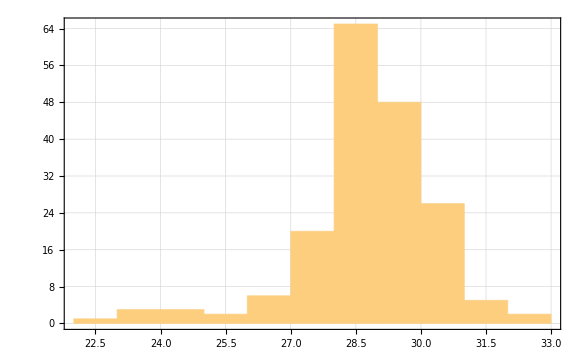

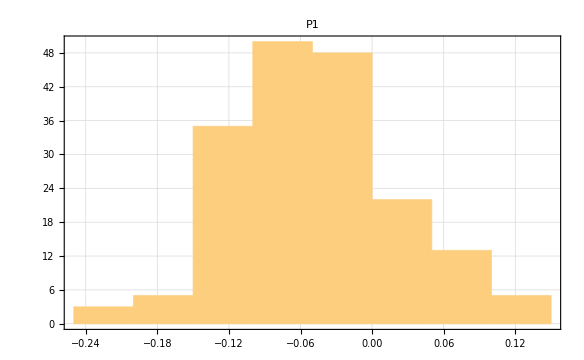

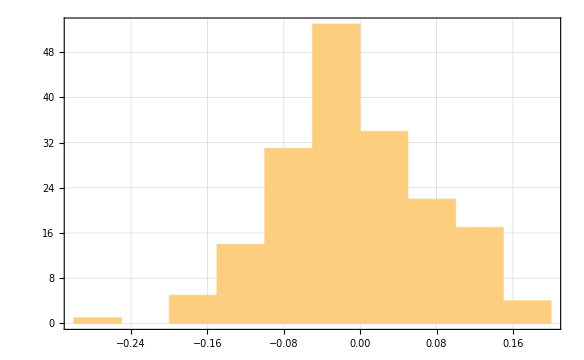

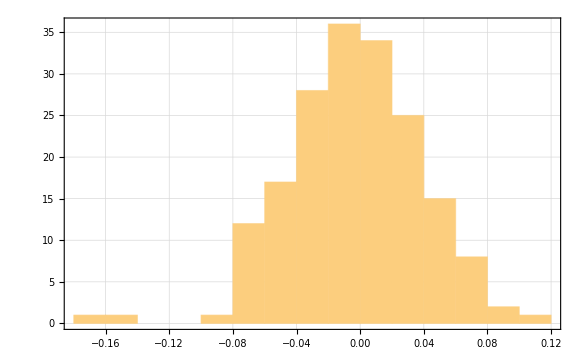

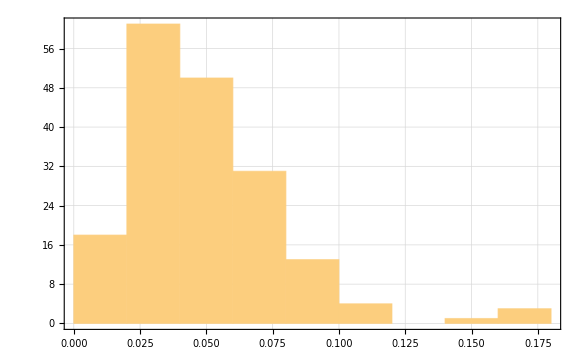

```mathematica
Dataset[stokes]
Histogram[Dataset[stokes][All,"p0"],10]
Histogram[Dataset[stokes][All,"p1"],10,PlotLabel->"P1"]
Histogram[Dataset[stokes][All,"p2"],10]
Histogram[Dataset[stokes][All,"p3_s2"],10]
Histogram[Dataset[stokes][All,"p3_mag"],10]
```

```mathematica
GetAverageCountRateFromFilenames[fn[[;;10]]]["avgSignal"]
```

{22.4,24.9,24.8,24.8,22.5,25.5,25.8,21.1,24.,26.1,23.7,25.8,25.7,25.6,26.7,22.6,24.8,25.6,23.6,24.6,26.,26.9,22.8,26.3,22.7,25.4,21.9,21.9,24.3,25.1,23.5,23.1,24.6,22.3,26.5,27.2,23.3,25.,24.2,27.1,27.8,23.3,25.4,21.6,21.,24.2,23.4,26.8,27.,21.3,23.4,24.8,21.3,23.2,25.4,27.8,22.,21.4,21.8,24.2}

```mathematica
Dataset[dat]
```

Dataset[<>]

# Background Subtraction

```mathematica
directory="noBGP";
SetDirectory[FileNameJoin[{dataRunFolder,directory}]];
fn=FileNames[RegularExpression["POL.*_[0-9]*.dat"]];
ListFileNamesAndComments[fn]
Keys[CalculateAverageStokesFromFilenames[Take[fn,2]]]

allData=<||>;
gasOff=fn[[{1,5,12}]]
gasOn=Join[fn[[2;;4]],fn[[6;;11]]]
```

Dataset[<>]

{P_e,P_eerr,timeStart,timeEnd,p0,p1,p2,p3_mag,p3_c2,p3_s2,p0err,p1err,p2err,p3_magerr,p3_c2err,p3_s2err,File,Comments,IonGauge(Torr),CVGauge(N2)(Torr),CVGauge(He)(Torr),T_res,T_res_set,T_trg,T_trg_set,V_he,LEAKCURR,SCALE,AOUTCONV,REV,DATAPPR,STPPERREV,DATPTS,DWELL(s),QWP(STEP),IndividualRunInfo,AllRunsPlot}

{POL2019-04-03_103047.dat,POL2019-04-03_104135.dat,POL2019-04-03_114351.dat}

{POL2019-04-03_103343.dat,POL2019-04-03_103607.dat,POL2019-04-03_103829.dat,POL2019-04-03_104549.dat,POL2019-04-03_104804.dat,POL2019-04-03_105020.dat,POL2019-04-03_105235.dat,POL2019-04-03_105450.dat,POL2019-04-03_105706.dat}

```mathematica
GetAverageElectronPolarizationWithBackgroudSubtractionSUM[gasOn,gasOff]
```

Thread::tdlen: Objects of unequal length in {POL2019-04-03_103343.dat,POL2019-04-03_103607.dat,POL2019-04-03_103829.dat,POL2019-04-03_104549.dat,POL2019-04-03_104804.dat,POL2019-04-03_105020.dat,POL2019-04-03_105235.dat,POL2019-04-03_105450.dat,POL2019-04-03_105706.dat}+{-POL2019-04-03_103047.dat,-POL2019-04-03_104135.dat,-POL2019-04-03_114351.dat} cannot be combined.

Thread::tdlen: Objects of unequal length in {POL2019-04-03_103343.dat,POL2019-04-03_103607.dat,POL2019-04-03_103829.dat,POL2019-04-03_104549.dat,POL2019-04-03_104804.dat,POL2019-04-03_105020.dat,POL2019-04-03_105235.dat,POL2019-04-03_105450.dat,POL2019-04-03_105706.dat}+{POL2019-04-03_103047.dat,POL2019-04-03_104135.dat,POL2019-04-03_114351.dat} cannot be combined.

ProcessElectronPolarizationFromSignal[<|averagedFiles→{-POL2019-04-03_103047.dat,-POL2019-04-03_104135.dat,-POL2019-04-03_114351.dat}+{POL2019-04-03_103343.dat,POL2019-04-03_103607.dat,POL2019-04-03_103829.dat,POL2019-04-03_104549.dat,POL2019-04-03_104804.dat,POL2019-04-03_105020.dat,POL2019-04-03_105235.dat,POL2019-04-03_105450.dat,POL2019-04-03_105706.dat},signal→{13.3931,12.7665,13.0691,12.4296,11.7576,11.5306,11.6513,11.9385,12.6715,12.7245,12.2498,12.0968,12.3956,12.7333,13.4617,13.3415,13.1023,12.704,12.0579,11.8641,12.0058,12.9565,11.8918,12.4724,11.8298,12.5062,12.6034,12.4928,12.3324,12.6356,12.8017,12.3243,12.0176,11.3566,11.5229,11.6087,11.8114,11.2564,11.905,12.1325,12.6302,12.2987,11.4968,12.8098,12.2699,12.4713,12.0036,13.0146,12.7519,11.699,11.8723,10.959,11.1601,12.0639,11.8262,12.51,12.0185,12.413,12.5517,11.5349},error→{0.407034,0.377715,0.708942,0.42805,0.0460887,0.425686,0.424328,0.349951,0.551561,0.709799,0.626493,0.64488,0.563587,0.692671,0.748905,0.581146,0.588718,0.50125,0.299753,0.838524,0.714273,0.198651,0.647409,0.484389,0.30225,0.498363,0.530892,0.350326,0.505754,0.450823,0.247568,0.357003,0.405694,0.239527,0.15369,0.51904,0.413714,0.225629,0.562412,0.324288,0.484964,0.203555,0.147098,0.236449,0.351201,0.224988,0.465381,0.115456,0.452512,0.326912,0.343379,0.36061,0.249204,0.356134,0.54793,0.672416,0.306286,0.10472,0.384169,0.0933103}|>,<|averagedFiles→√({POL2019-04-03_103047.dat,POL2019-04-03_104135.dat,POL2019-04-03_114351.dat}+{POL2019-04-03_103343.dat,POL2019-04-03_103607.dat,POL2019-04-03_103829.dat,POL2019-04-03_104549.dat,POL2019-04-03_104804.dat,POL2019-04-03_105020.dat,POL2019-04-03_105235.dat,POL2019-04-03_105450.dat,POL2019-04-03_105706.dat}),signal→{4.00135,3.93579,4.03562,3.91767,3.92101,3.85326,3.92621,3.95698,4.02317,3.93554,3.91489,3.89525,3.9625,3.97857,4.00535,4.03138,3.95904,3.86358,3.84444,3.98935,3.93703,3.95079,4.00364,3.91935,3.92428,3.87996,3.94916,4.00418,3.86033,3.9793,3.77952,3.94207,3.81763,3.86263,3.97223,3.86102,3.89934,3.90429,3.93282,3.87737,3.92663,3.9292,3.87586,3.86198,3.81956,3.80057,3.82875,3.90434,3.83854,3.8928,3.90637,3.77114,3.82991,3.91453,3.80164,3.8996,3.80203,3.94953,3.99513,3.86954},error→{1.00112,1.02758,1.09538,0.925968,1.00886,1.02614,0.989195,0.980389,1.00379,0.995041,1.0191,0.923124,0.920033,0.9536,0.944775,1.02592,0.928159,1.03304,0.918365,0.966901,1.01951,1.13462,0.983883,1.07568,0.9546,0.890746,1.01969,0.91935,1.01698,0.821038,0.858503,0.986129,0.749699,1.02162,1.02864,0.926546,0.91853,0.960528,0.918647,0.857515,1.00945,0.837511,0.953428,0.891529,0.830293,0.764061,0.981148,0.856005,0.723902,0.99707,0.899092,0.714921,0.906485,0.796242,0.881129,0.862804,0.852346,0.894279,0.983744,0.839766}|>]

POL2019-04-03_103343.dat

POL2019-04-03_103047.dat

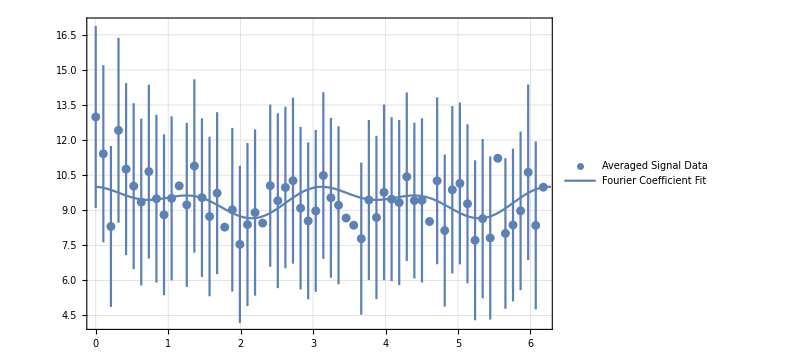
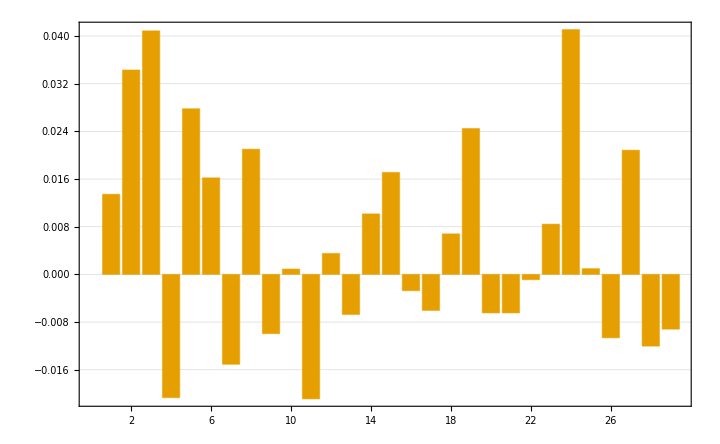
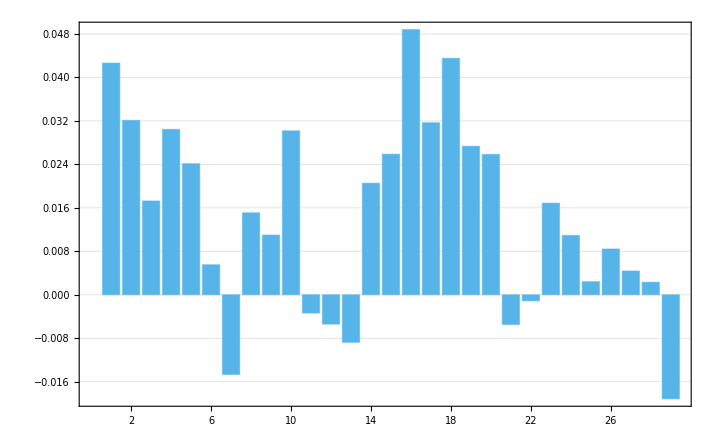
<|File→/home/pi/RbData/2019-04-03/POL2019-04-03_103343.dat,Comments→gas on, no BGP, polarization run,IonGauge(Torr)→1.36×10^-6,CVGauge(N2)(Torr)→0.0351,CVGauge(He)(Torr)→0.00157,T_res→-1.,T_res_set→-1.,T_trg→-1.,T_trg_set→-1.,V_he→144,LEAKCURR→0.,SCALE→8,AOUTCONV→0.06214,REV→1,DATAPPR→60,STPPERREV→1200,DATPTS→60,DWELL(s)→2,QWP(STEP)→82,dataset→{<|STEP→0,COUNT→498,CURRENT→-1.67074,CURRENTsd→-0.001824,ANGLE→0.|>,<|STEP→20,COUNT→440,CURRENT→-1.59868,CURRENTsd→0.012766,ANGLE→0.10472|>,<|STEP→40,COUNT→319,CURRENT→-1.4448,CURRENTsd→0.013276,ANGLE→0.20944|>,<|STEP→60,COUNT→412,CURRENT→-1.36908,CURRENTsd→-0.007965,ANGLE→0.314159|>,<|STEP→80,COUNT→422,CURRENT→-1.62189,CURRENTsd→0.010654,ANGLE→0.418879|>,<|STEP→100,COUNT→374,CURRENT→-1.53029,CURRENTsd→0.002801,ANGLE→0.523599|>,<|STEP→120,COUNT→349,CURRENT→-1.45457,CURRENTsd→-0.050618,ANGLE→0.628319|>,<|STEP→140,COUNT→409,CURRENT→-1.55838,CURRENTsd→0.003934,ANGLE→0.733038|>,<|STEP→160,COUNT→352,CURRENT→-1.44846,CURRENTsd→0.018463,ANGLE→0.837758|>,<|STEP→180,COUNT→306,CURRENT→-1.34587,CURRENTsd→-0.025641,ANGLE→0.942478|>,<|STEP→200,COUNT→403,CURRENT→-1.71959,CURRENTsd→0.032637,ANGLE→1.0472|>,<|STEP→220,COUNT→379,CURRENT→-1.56815,CURRENTsd→-0.004651,ANGLE→1.15192|>,<|STEP→240,COUNT→344,CURRENT→-1.468,CURRENTsd→0.044309,ANGLE→1.25664|>,<|STEP→260,COUNT→384,CURRENT→-1.44602,CURRENTsd→-0.070644,ANGLE→1.36136|>,<|STEP→280,COUNT→380,CURRENT→-1.67196,CURRENTsd→0.008471,ANGLE→1.46608|>,<|STEP→300,COUNT→357,CURRENT→-1.61456,CURRENTsd→-0.005267,ANGLE→1.5708|>,<|STEP→320,COUNT→384,CURRENT→-1.63898,CURRENTsd→0.005243,ANGLE→1.67552|>,<|STEP→340,COUNT→339,CURRENT→-1.68539,CURRENTsd→0.005831,ANGLE→1.78024|>,<|STEP→360,COUNT→337,CURRENT→-1.45213,CURRENTsd→0.003376,ANGLE→1.88496|>,<|STEP→380,COUNT→295,CURRENT→-1.41915,CURRENTsd→0.016178,ANGLE→1.98968|>,<|STEP→400,COUNT→367,CURRENT→-1.6512,CURRENTsd→0.006701,ANGLE→2.0944|>,<|STEP→420,COUNT→369,CURRENT→-1.58403,CURRENTsd→0.065735,ANGLE→2.19912|>,<|STEP→440,COUNT→328,CURRENT→-1.44358,CURRENTsd→-0.011706,ANGLE→2.30384|>,<|STEP→460,COUNT→329,CURRENT→-1.36297,CURRENTsd→-0.015439,ANGLE→2.40855|>,<|STEP→480,COUNT→371,CURRENT→-1.46678,CURRENTsd→0.033563,ANGLE→2.51327|>,<|STEP→500,COUNT→364,CURRENT→-1.53395,CURRENTsd→-0.033474,ANGLE→2.61799|>,<|STEP→520,COUNT→409,CURRENT→-1.66585,CURRENTsd→-0.009081,ANGLE→2.72271|>,<|STEP→540,COUNT→381,CURRENT→-1.66707,CURRENTsd→0.004415,ANGLE→2.82743|>,<|STEP→560,COUNT→356,CURRENT→-1.65608,CURRENTsd→0.014211,ANGLE→2.93215|>,<|STEP→580,COUNT→343,CURRENT→-1.50464,CURRENTsd→0.015664,ANGLE→3.03687|>,<|STEP→600,COUNT→353,CURRENT→-1.40205,CURRENTsd→-0.012048,ANGLE→3.14159|>,<|STEP→620,COUNT→345,CURRENT→-1.49487,CURRENTsd→-0.0471,ANGLE→3.24631|>,<|STEP→640,COUNT→367,CURRENT→-1.64387,CURRENTsd→0.020083,ANGLE→3.35103|>,<|STEP→660,COUNT→353,CURRENT→-1.58647,CURRENTsd→0.002315,ANGLE→3.45575|>,<|STEP→680,COUNT→354,CURRENT→-1.57303,CURRENTsd→-0.009231,ANGLE→3.56047|>,<|STEP→700,COUNT→324,CURRENT→-1.61212,CURRENTsd→-0.000757,ANGLE→3.66519|>,<|STEP→720,COUNT→353,CURRENT→-1.5364,CURRENTsd→0.060708,ANGLE→3.76991|>,<|STEP→740,COUNT→356,CURRENT→-1.57059,CURRENTsd→0.049368,ANGLE→3.87463|>,<|STEP→760,COUNT→358,CURRENT→-1.38251,CURRENTsd→-0.089666,ANGLE→3.97935|>,<|STEP→780,COUNT→368,CURRENT→-1.56204,CURRENTsd→0.003137,ANGLE→4.08407|>,<|STEP→800,COUNT→349,CURRENT→-1.47411,CURRENTsd→-0.000414,ANGLE→4.18879|>,<|STEP→820,COUNT→340,CURRENT→-1.33244,CURRENTsd→-0.008632,ANGLE→4.29351|>,<|STEP→840,COUNT→371,CURRENT→-1.67318,CURRENTsd→0.02277,ANGLE→4.39823|>,<|STEP→860,COUNT→366,CURRENT→-1.55471,CURRENTsd→-0.000393,ANGLE→4.50295|>,<|STEP→880,COUNT→339,CURRENT→-1.57303,CURRENTsd→0.008614,ANGLE→4.60767|>,<|STEP→900,COUNT→373,CURRENT→-1.50098,CURRENTsd→0.039323,ANGLE→4.71239|>,<|STEP→920,COUNT→335,CURRENT→-1.64143,CURRENTsd→0.072626,ANGLE→4.81711|>,<|STEP→940,COUNT→343,CURRENT→-1.3874,CURRENTsd→-0.062706,ANGLE→4.92183|>,<|STEP→960,COUNT→342,CURRENT→-1.41915,CURRENTsd→0.010874,ANGLE→5.02655|>,<|STEP→980,COUNT→311,CURRENT→-1.35809,CURRENTsd→-0.017234,ANGLE→5.13127|>,<|STEP→1000,COUNT→291,CURRENT→-1.35442,CURRENTsd→0.015103,ANGLE→5.23599|>,<|STEP→1020,COUNT→355,CURRENT→-1.61456,CURRENTsd→0.017314,ANGLE→5.34071|>,<|STEP→1040,COUNT→317,CURRENT→-1.44602,CURRENTsd→0.00339,ANGLE→5.44543|>,<|STEP→1060,COUNT→335,CURRENT→-1.18955,CURRENTsd→-0.043222,ANGLE→5.55015|>,<|STEP→1080,COUNT→325,CURRENT→-1.617,CURRENTsd→-0.002261,ANGLE→5.65487|>,<|STEP→1100,COUNT→333,CURRENT→-1.60112,CURRENTsd→-0.004934,ANGLE→5.75959|>,<|STEP→1120,COUNT→361,CURRENT→-1.62677,CURRENTsd→0.01139,ANGLE→5.86431|>,<|STEP→1140,COUNT→378,CURRENT→-1.41671,CURRENTsd→0.011775,ANGLE→5.96903|>,<|STEP→1160,COUNT→327,CURRENT→-1.40694,CURRENTsd→0.011858,ANGLE→6.07375|>,<|STEP→1180,COUNT→391,CURRENT→-1.55227,CURRENTsd→0.054334,ANGLE→6.17847|>},signal→{14.0656,12.8856,10.0706,14.024,12.1464,11.3051,11.0342,12.2242,11.1843,10.3279,10.9038,11.1915,10.7629,12.3097,10.5266,10.1885,10.8604,9.22633,10.6396,9.40704,10.2653,10.7637,10.3909,11.0421,11.6923,10.9521,11.4356,10.5874,9.90289,10.4676,11.5902,10.6029,10.311,10.2429,10.3621,9.18049,10.5767,10.4419,11.9348,10.8832,10.8879,11.7079,10.2499,10.8702,9.88536,11.4925,9.35162,11.3522,11.063,10.4191,9.70895,10.1266,9.99295,12.9041,9.18367,9.52456,10.235,12.3526,10.6259,11.6925},backgroundHeader→<|File→/home/pi/RbData/2019-04-03/POL2019-04-03_103047.dat,Comments→gas off, no BGP, polarization run,IonGauge(Torr)→6.37×10^-7,CVGauge(N2)(Torr)→0.00368,CVGauge(He)(Torr)→0.000276,T_res→-1.,T_res_set→-1.,T_trg→-1.,T_trg_set→-1.,V_he→144,LEAKCURR→0.,SCALE→8,AOUTCONV→0.06214,REV→1,DATAPPR→60,STPPERREV→1200,DATPTS→60,DWELL(s)→2,QWP(STEP)→82|>,datasetBack→{<|STEP→0,COUNT→64,CURRENT→-1.31412,CURRENTsd→0.03263,ANGLE→0.|>,<|STEP→20,COUNT→75,CURRENT→-1.18222,CURRENTsd→-0.013754,ANGLE→0.10472|>,<|STEP→40,COUNT→79,CURRENT→-1.23596,CURRENTsd→-0.050211,ANGLE→0.20944|>,<|STEP→60,COUNT→72,CURRENT→-1.36419,CURRENTsd→0.038104,ANGLE→0.314159|>,<|STEP→80,COUNT→73,CURRENT→-1.40205,CURRENTsd→-0.034077,ANGLE→0.418879|>,<|STEP→100,COUNT→67,CURRENT→-1.25428,CURRENTsd→-0.001944,ANGLE→0.523599|>,<|STEP→120,COUNT→77,CURRENT→-1.38495,CURRENTsd→0.050973,ANGLE→0.628319|>,<|STEP→140,COUNT→77,CURRENT→-1.00635,CURRENTsd→-0.123404,ANGLE→0.733038|>,<|STEP→160,COUNT→77,CURRENT→-1.23229,CURRENTsd→0.007992,ANGLE→0.837758|>,<|STEP→180,COUNT→69,CURRENT→-1.33,CURRENTsd→-0.087175,ANGLE→0.942478|>,<|STEP→200,COUNT→76,CURRENT→-1.36908,CURRENTsd→0.027969,ANGLE→1.0472|>,<|STEP→220,COUNT→64,CURRENT→-1.27748,CURRENTsd→0.006737,ANGLE→1.15192|>,<|STEP→240,COUNT→73,CURRENT→-1.39472,CURRENTsd→0.026517,ANGLE→1.25664|>,<|STEP→260,COUNT→69,CURRENT→-1.2958,CURRENTsd→0.021666,ANGLE→1.36136|>,<|STEP→280,COUNT→61,CURRENT→-1.43869,CURRENTsd→0.070909,ANGLE→1.46608|>,<|STEP→300,COUNT→75,CURRENT→-1.22863,CURRENTsd→0.063425,ANGLE→1.5708|>,<|STEP→320,COUNT→65,CURRENT→-1.26038,CURRENTsd→-0.071525,ANGLE→1.67552|>,<|STEP→340,COUNT→60,CURRENT→-1.47777,CURRENTsd→-0.003295,ANGLE→1.78024|>,<|STEP→360,COUNT→75,CURRENT→-1.48754,CURRENTsd→-0.005714,ANGLE→1.88496|>,<|STEP→380,COUNT→81,CURRENT→-1.36908,CURRENTsd→0.037003,ANGLE→1.98968|>,<|STEP→400,COUNT→90,CURRENT→-1.5254,CURRENTsd→0.02377,ANGLE→2.0944|>,<|STEP→420,COUNT→87,CURRENT→-1.24328,CURRENTsd→-0.000981,ANGLE→2.19912|>,<|STEP→440,COUNT→84,CURRENT→-1.23962,CURRENTsd→0.019076,ANGLE→2.30384|>,<|STEP→460,COUNT→55,CURRENT→-1.47777,CURRENTsd→0.027601,ANGLE→2.40855|>,<|STEP→480,COUNT→95,CURRENT→-1.39961,CURRENTsd→0.000436,ANGLE→2.51327|>,<|STEP→500,COUNT→58,CURRENT→-1.44236,CURRENTsd→0.054464,ANGLE→2.61799|>,<|STEP→520,COUNT→67,CURRENT→-1.25916,CURRENTsd→-0.047135,ANGLE→2.72271|>,<|STEP→540,COUNT→78,CURRENT→-1.28114,CURRENTsd→-0.091775,ANGLE→2.82743|>,<|STEP→560,COUNT→73,CURRENT→-1.30679,CURRENTsd→0.037827,ANGLE→2.93215|>,<|STEP→580,COUNT→73,CURRENT→-1.5254,CURRENTsd→0.050463,ANGLE→3.03687|>,<|STEP→600,COUNT→59,CURRENT→-1.25916,CURRENTsd→0.042994,ANGLE→3.14159|>,<|STEP→620,COUNT→60,CURRENT→-1.20664,CURRENTsd→-0.034213,ANGLE→3.24631|>,<|STEP→640,COUNT→64,CURRENT→-1.25672,CURRENTsd→0.025411,ANGLE→3.35103|>,<|STEP→660,COUNT→78,CURRENT→-1.23229,CURRENTsd→0.02645,ANGLE→3.45575|>,<|STEP→680,COUNT→91,CURRENT→-1.19565,CURRENTsd→-0.061361,ANGLE→3.56047|>,<|STEP→700,COUNT→73,CURRENT→-1.17978,CURRENTsd→-0.02719,ANGLE→3.66519|>,<|STEP→720,COUNT→63,CURRENT→-1.27992,CURRENTsd→0.021443,ANGLE→3.76991|>,<|STEP→740,COUNT→83,CURRENT→-1.20054,CURRENTsd→-0.099817,ANGLE→3.87463|>,<|STEP→760,COUNT→88,CURRENT→-1.45457,CURRENTsd→-0.000839,ANGLE→3.97935|>,<|STEP→780,COUNT→72,CURRENT→-1.42892,CURRENTsd→0.078838,ANGLE→4.08407|>,<|STEP→800,COUNT→74,CURRENT→-1.24084,CURRENTsd→0.017017,ANGLE→4.18879|>,<|STEP→820,COUNT→62,CURRENT→-1.16268,CURRENTsd→-0.068493,ANGLE→4.29351|>,<|STEP→840,COUNT→56,CURRENT→-1.30557,CURRENTsd→-0.056903,ANGLE→4.39823|>,<|STEP→860,COUNT→73,CURRENT→-1.41182,CURRENTsd→-0.001296,ANGLE→4.50295|>,<|STEP→880,COUNT→71,CURRENT→-1.4448,CURRENTsd→-0.015397,ANGLE→4.60767|>,<|STEP→900,COUNT→65,CURRENT→-1.5022,CURRENTsd→0.020324,ANGLE→4.71239|>,<|STEP→920,COUNT→68,CURRENT→-1.35686,CURRENTsd→0.029657,ANGLE→4.81711|>,<|STEP→940,COUNT→69,CURRENT→-1.25183,CURRENTsd→-0.053118,ANGLE→4.92183|>,<|STEP→960,COUNT→54,CURRENT→-1.39228,CURRENTsd→0.030741,ANGLE→5.02655|>,<|STEP→980,COUNT→59,CURRENT→-1.18466,CURRENTsd→-0.033383,ANGLE→5.13127|>,<|STEP→1000,COUNT→82,CURRENT→-1.25672,CURRENTsd→0.027972,ANGLE→5.23599|>,<|STEP→1020,COUNT→76,CURRENT→-1.48632,CURRENTsd→-0.004906,ANGLE→5.34071|>,<|STEP→1040,COUNT→91,CURRENT→-1.51075,CURRENTsd→0.013934,ANGLE→5.44543|>,<|STEP→1060,COUNT→68,CURRENT→-1.40449,CURRENTsd→0.048314,ANGLE→5.55015|>,<|STEP→1080,COUNT→66,CURRENT→-1.50953,CURRENTsd→0.032581,ANGLE→5.65487|>,<|STEP→1100,COUNT→65,CURRENT→-1.31778,CURRENTsd→0.037001,ANGLE→5.75959|>,<|STEP→1120,COUNT→69,CURRENT→-1.27015,CURRENTsd→0.00241,ANGLE→5.86431|>,<|STEP→1140,COUNT→77,CURRENT→-1.27015,CURRENTsd→-0.029851,ANGLE→5.96903|>,<|STEP→1160,COUNT→92,CURRENT→-1.50098,CURRENTsd→0.039323,ANGLE→6.07375|>,<|STEP→1180,COUNT→81,CURRENT→-1.28359,CURRENTsd→-0.006616,ANGLE→6.17847|>},background→{1.07737,1.46996,1.76495,1.60692,1.38727,1.27427,1.68435,1.57215,1.69145,1.52318,1.39568,1.14785,1.5327,1.41769,0.986866,1.45551,1.12875,0.949333,1.61832,1.86731,1.87743,1.86234,1.93963,0.990484,2.28391,0.977866,1.17057,1.49963,1.35863,1.49537,1.10552,1.07033,1.09498,1.57583,2.0025,1.39568,1.13903,1.75093,2.16996,1.40841,1.56027,1.27586,0.83673,1.44721,1.36679,1.23253,1.21845,1.47759,0.916041,1.14131,1.99347,1.48647,2.17839,1.68131,1.17502,1.15544,1.26017,1.72936,2.27444,1.70718},fourierFit→-Graphics-,fourierFitFunction→(c$2247892[0]+c$2247892[2] Cos[2 #1]+s$2247892[2] Sin[2 #1]+c$2247892[4] Cos[4 #1]+s$2247892[4] Sin[4 #1]&),fc→<|Sin Coefficients→<|0→0.,1→0.12654,2→0.322843,3→0.384648,4→-0.194676,5→0.261637,6→0.152482,7→-0.141974,8→0.197741,9→-0.0935892,10→0.00843834,11→-0.196584,12→0.0330752,13→-0.0633373,14→0.0955648,15→0.161079,16→-0.0257284,17→-0.0569089,18→0.0640369,19→0.230375,20→-0.0608461,21→-0.0608478,22→-0.00840714,23→0.0793575,24→0.386629,25→0.00909438,26→-0.10016,27→0.196177,28→-0.113269,29→-0.0864903|>,Cos Coefficients→<|0→9.4117,1→0.40135,2→0.302138,3→0.162536,4→0.286506,5→0.227084,6→0.0520866,7→-0.138037,8→0.142013,9→0.103474,10→0.284001,11→-0.0316758,12→-0.0508915,13→-0.0823733,14→0.193306,15→0.243563,16→0.459327,17→0.29804,18→0.409588,19→0.257275,20→0.243215,21→-0.0515327,22→-0.0105112,23→0.158739,24→0.102856,25→0.0227369,26→0.0793678,27→0.0412286,28→0.0217585,29→-0.180294|>,Sin Coefficients Error→<||>,Cos Coefficients Error→<||>|>,fcBarChart→<|SinCoefficients→-Graphics-,CosCoefficients→-Graphics-|>,stokes→<|p0→9.15728,p1→0.0689949,p2→0.0124198,p3_mag→0.0485907,p3_c2→1.05372,p3_s2→0.0353837|>,P_e→0.0829767|>

```mathematica
fn=gasOn[[1]]
fnBack=gasOff[[1]]
results=<||>;
f=ImportFile[fn];
header=f[[1]];
AppendTo[results,header];
dataset=f[[2]];
AppendTo[results,"dataset"->Normal[dataset]];

counts=Normal[dataset[All,"COUNT"]];
current=Abs[Normal[dataset[All,"CURRENT"]]]*10^(-header["SCALE"])/nA;
dwellTime=header["DWELL(s)"];
signal=NormalizePolarizationData[counts,current,dwellTime];
AppendTo[results,"signal"->signal];


f=ImportFile[fnBack];
header=f[[1]];
AppendTo[results,"backgroundHeader"->header];
dataset=f[[2]];
AppendTo[results,"datasetBack"->Normal[dataset]];

counts=Normal[dataset[All,"COUNT"]];
dwellTime=header["DWELL(s)"];
background=NormalizePolarizationData[counts,current,dwellTime];
AppendTo[results,"background"->background];

AppendTo[results,ProcessElectronPolarizationFromSignal[signal-background,Sqrt[signal+background]]](* See Private Functions for the rest of processing. *)
```

```mathematica
(* I think that I can alleviate some confusion by plotting the fits for all of the no beam background to show that the fourier fit is just noise. *)
```

```mathematica
d=Map[ProcessElectronPolarizationFile,gasOff];
```

```mathematica
Normal[Dataset[d][All,"fourierFitFunction"]][[1]]
```

c$1791161[0]+c$1791161[2] Cos[2 #1]+s$1791161[2] Sin[2 #1]+c$1791161[4] Cos[4 #1]+s$1791161[4] Sin[4 #1]&

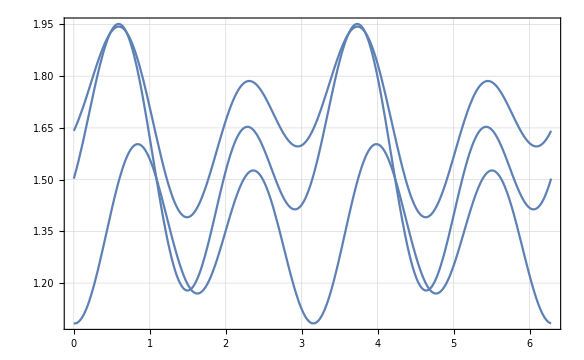

```mathematica
Plot[Through[Normal[Dataset[d][All,"fourierFitFunction"]][θ]],{θ,0,2π}]
```

```mathematica
(* I guess not. That noise looks pretty consistent. This background isn't as random as I thought. *)
```

```mathematica
fn=gasOn;
fnBack=gasOff;

rawSignal=GetAverageCurrentNormalizedCountRateFromFilenames[fn]
beamBackgroundSignal=GetAverageCurrentNormalizedCountRateFromFilenames[fnBack];
dat=ProcessElectronPolarizationFromSignal[rawSignal["signal"]-beamBackgroundSignal["signal"],Sqrt[rawSignal["error"]^2+beamBackgroundSignal["error"]^2]];
```

<|averagedFiles→{POL2019-04-03_103343.dat,POL2019-04-03_103607.dat,POL2019-04-03_103829.dat,POL2019-04-03_104549.dat,POL2019-04-03_104804.dat,POL2019-04-03_105020.dat,POL2019-04-03_105235.dat,POL2019-04-03_105450.dat,POL2019-04-03_105706.dat},signal→{14.702,14.1285,14.6777,13.8889,13.5659,13.1891,13.5332,13.7981,14.4287,14.1065,13.788,13.6349,14.0485,14.2812,14.7523,14.7968,14.3882,13.8156,13.4188,13.8895,13.753,14.2826,13.9605,13.9168,13.6149,13.7801,14.0996,14.2632,13.6172,14.2352,13.5433,13.9321,13.296,13.1382,13.6508,13.2581,13.5081,13.25,13.686,13.5832,14.0243,13.8687,13.2596,13.8623,13.4295,13.4578,13.3314,14.1292,13.7432,13.4264,13.566,12.5902,12.9142,13.6937,13.1393,13.8584,13.237,14.0059,14.2564,13.2541},error→{0.704637,0.716816,0.954401,0.642733,0.531943,0.73933,0.701418,0.655557,0.779576,0.849953,0.832526,0.74852,0.705024,0.801012,0.820752,0.816832,0.725099,0.784206,0.571574,0.886711,0.876841,0.743007,0.807718,0.820738,0.606756,0.645896,0.785328,0.597765,0.769998,0.562463,0.492298,0.664727,0.483871,0.641613,0.605897,0.688764,0.628706,0.574121,0.703162,0.52981,0.751973,0.452489,0.528061,0.515636,0.520294,0.404388,0.714016,0.424101,0.488273,0.660531,0.575872,0.435861,0.535459,0.495067,0.662159,0.708423,0.51639,0.452228,0.675961,0.399258}|>

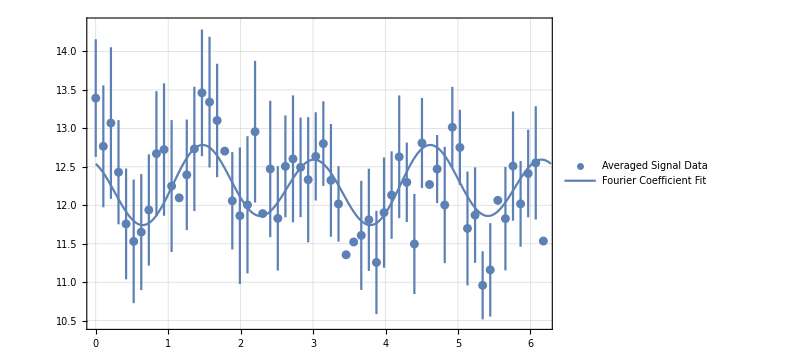

```mathematica
Dataset[dat]["fourierFit"]
```

# Averaging at FC level

```mathematica
Dataset[ProcessElectronPolarizationFileAverageFOURIER[gasOn]]
```

Dataset[<>]

## 2019-04-09: 0853 - Fixing ProcessElectronPolarizationFromSignal Append Error

```mathematica
(* I had accidentally added the dwell time as an argument, but it's not supposed to be an argument for processing the signal. *)
```

## 2019 - 04 - 09 : 0855 - Ironing out kinks in code developed yesterday

## 2019 - 04 - 09 : 0920 - Generate Raw Data Plots that Dr. Gay wanted

The plots!

## For Dark Counts

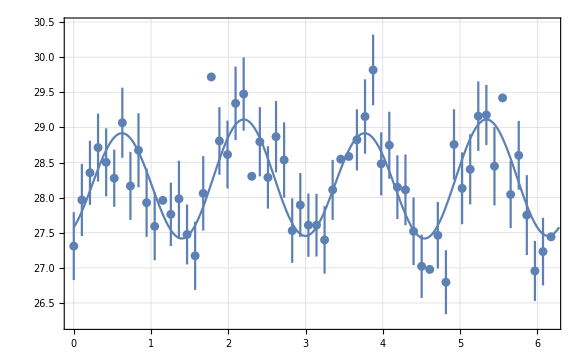

## For Signal and Beam Background

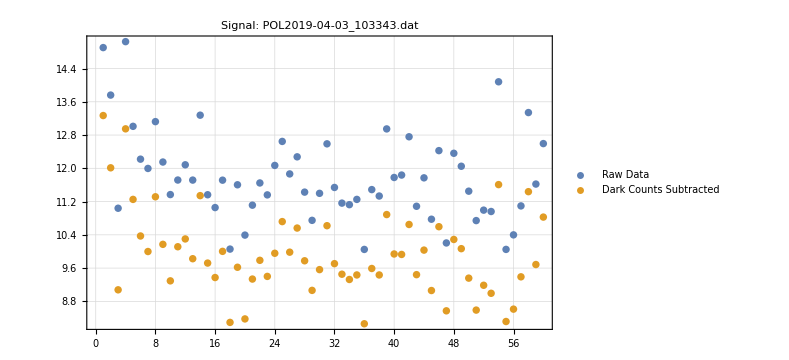
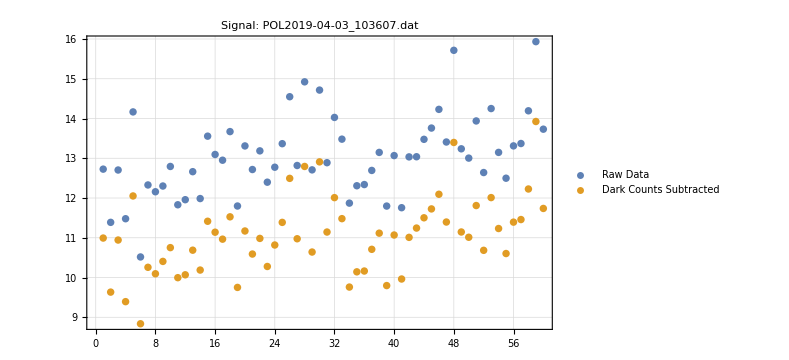
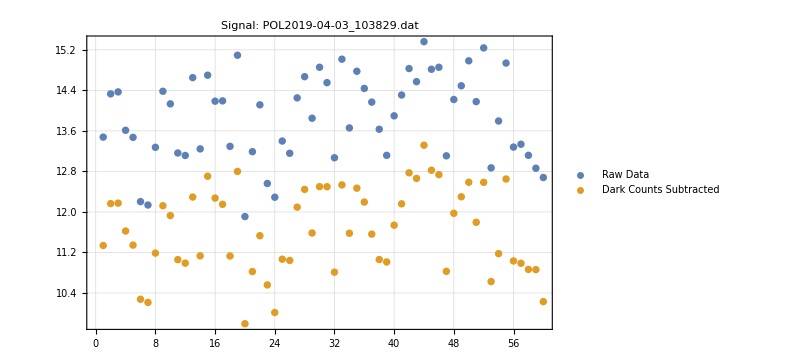
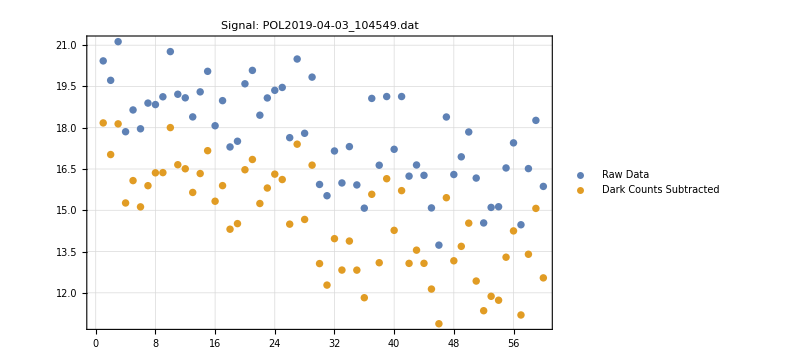
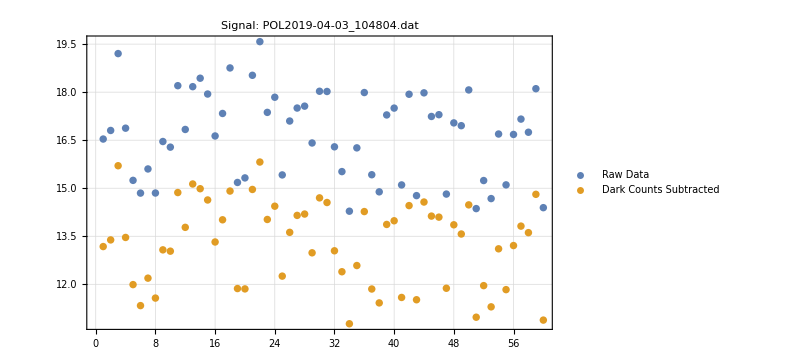
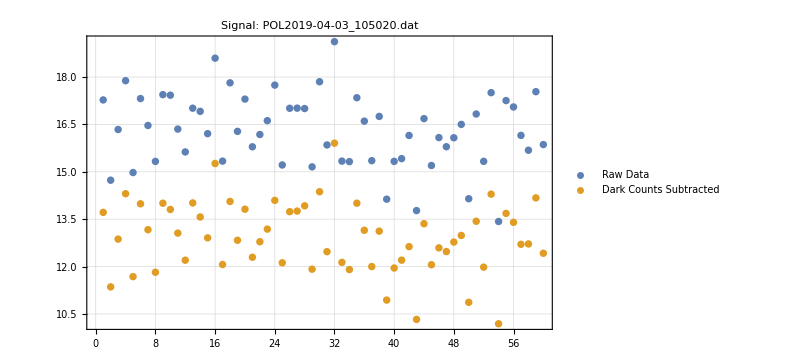
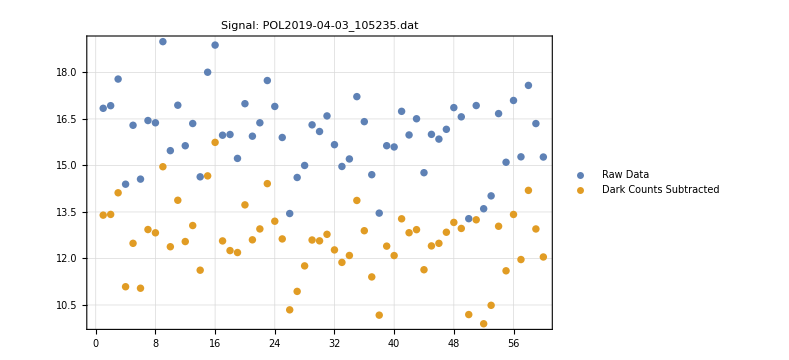
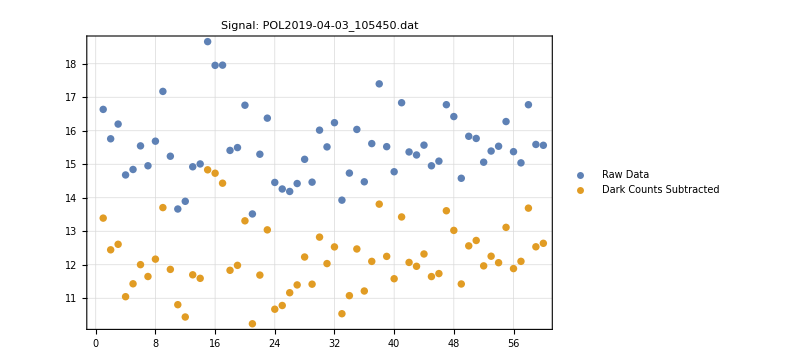

```mathematica
This is done, now generating lists of the stokes parameters.
```

The Stokes Parameters!

## For the dark counts

Dataset[<>]

## For the signal and beam background

Dataset[<>]

Dataset[<>]

Dataset[<>]

«5 more identical outputs»

## 2019-04-09:1544 - Fixing the Broken electron polarization. Gives NULLs for some reason.

```mathematica
cn=True;
darkCountsSubtract=True;
directory="noBGP";
SetDirectory[FileNameJoin[{$DATARUNS,"2019-03-06","data",directory}]];
fnHold=FileNames[RegularExpression["POL.*_[0-9]*.dat"]];
gasOff=fnHold[[{1,5,12}]];
fn=Join[fnHold[[2;;4]],fnHold[[6;;11]]];

	results=<||>;
irResults=<||>;

	r=ProcessElectronPolarizationFileAverageSUM[fn,cn,darkCountsSubtract];

	iri=Normal[Dataset[r][Values,"IndividualRunInfo"][[1]]];

	signals=Normal[Dataset[r][Values,"IndividualRunInfo",Values,"signal"][[1]]];
	irResultsMapper[results_]:=AssociationThread[{"fcCoefficients"},results];
	
	dfts=DFT/@signals;
	fcTitles={"Sin Coefficients","Cos Coefficients"};
	res=Map[StandardDeviation[Values[dfts[[All,#]]]]/Length[dfts]&,fcTitles];
	fcThreader[values_]:=AssociationThread[Keys[dfts[[1,1]]],values];
	res=Map[fcThreader,res];
	errors=AssociationThread[StringInsert[fcTitles," Error",-1],res];
	avgFourierComponents=Join[Mean[dfts],errors];
	AppendTo[irResults,AssociationThread[fn,Map[irResultsMapper,Transpose[{dfts}]]]];
	AppendTo[results,"averagedFiles"->fn];
	

	For[i=1,i<=Length[iri],i++,
		AppendTo[iri[[i]],irResults[[i]]];
	];
	
	AppendTo[results,ProcessElectronPolarizationFromFourierCoefficients[avgFourierComponents]];
	AppendTo[results,avgFourierComponents];
	AppendTo[results,<|"IndividualRunInfo"->iri|>];
	d=<|fn[[1]]->results|>
	
	iri=Normal[Dataset[d][Values,"IndividualRunInfo"][[1]]];
	dfts=Normal[Dataset[d][Values,"IndividualRunInfo",Values,"fcCoefficients"][[1]]];

	sin=Through[dfts["Sin Coefficients"]];
	cos=Through[dfts["Cos Coefficients"]];
	c0=Transpose[Values[cos]][[0+1]];
	c2=Transpose[Values[cos]][[2+1]];
	c4=Transpose[Values[cos]][[4+1]];
	s2=Transpose[Values[sin]][[2+1]];
	s4=Transpose[Values[sin]][[4+1]];
	stokes=Apply[CalculateStokesFromFourierCoefficients,Transpose[{c0,c2,c4,s2,s4}],{1}];

	irResultsMapper[results_]:=AssociationThread[{"stokes"},results];
	fcThreader[values_]:=AssociationThread[Keys[dfts[[1,1]]],values];

	AppendTo[irResults,AssociationThread[fn,Map[irResultsMapper,Transpose[{stokes}]]]];

	stokes2=stokes[[1]];
	stokesStdDev=<||>;(*Just creating another object with the same length as stokes *)
	transposedValues=Transpose[Values[stokes]];
	For[i=1,i<=Length[stokes2],i++,
		AppendTo[stokes2,stokesNames[[i]]->Mean[transposedValues[[i]]]];
		AppendTo[stokesStdDev,stokesErrNames[[i]]->StandardDeviation[transposedValues[[i]]]/Sqrt[Length[transposedValues]]];
	];
	avg=Join[Association[stokes2],Association[stokesStdDev]]

	For[i=1,i<=Length[iri],i++,
		AppendTo[iri[[i]],irResults[[i]]];
	];
	PrependTo[results,<|"avgStokes"->avg|>];
	AppendTo[results,<|"IndividualRunInfo"->iri|>];
	PrependTo[results,<|ProcessElectronPolarizationFromStokesParameters[avg]|>];
	<|fn[[1]]->results|>
```

```mathematica
(* The problem was caused because of a missing semi-colon. Life is hard. *)
```

## 2019-04-10: 1100 - Changing to Vector Averaging of stokes, weighting the P1,P2,P3 by the P0.

```mathematica
directory="noBGP";

SetDirectory[FileNameJoin[{$DATARUNS,"2019-03-06","data",directory}]]
fn=FileNames[RegularExpression["POL.*_[0-9]*.dat"]];
gasOff=fn[[{1,5,12}]];
gasOn=Join[fn[[2;;4]],fn[[6;;11]]];
gasOn=fn[[2;;4]];(* A shorter vector for quicker processing *)


d1=Map[ProcessElectronPolarizationFile[#,True]&,gasOn];

d=Dataset[ProcessElectronPolarizationFileAverageSTOKES[gasOn,True,True][[1]]]
```

C:\Users\kahrendsen2\Box Sync\Research\DataRuns\2019-03-06\data\noBGP

Dataset[<>]

```mathematica
(* Problems, going a level deeper. *)
```

```mathematica
fcTitles={"Sin Coefficients","Cos Coefficients"};

	d=ProcessElectronPolarizationFileAverageFOURIER[fn,cn,darkCountsSubtract];
	
	iri=Normal[Dataset[d][Values,"IndividualRunInfo"][[1]]];
	dfts=Normal[Dataset[d][Values,"IndividualRunInfo",Values,"fcCoefficients"][[1]]];

	sin=Through[dfts["Sin Coefficients"]];
	cos=Through[dfts["Cos Coefficients"]];
	c0=Transpose[Values[cos]][[0+1]];
	c2=Transpose[Values[cos]][[2+1]];
	c4=Transpose[Values[cos]][[4+1]];
	s2=Transpose[Values[sin]][[2+1]];
	s4=Transpose[Values[sin]][[4+1]];
	stokes=Apply[CalculateStokesFromFourierCoefficients,Transpose[{c0,c2,c4,s2,s4}],{1}];

	irResultsMapper[results_]:=AssociationThread[{"stokes"},results];
	fcThreader[values_]:=AssociationThread[Keys[dfts[[1,1]]],values];

	AppendTo[irResults,AssociationThread[fn,Map[irResultsMapper,Transpose[{stokes2}]]]];
	
	stokesAvg=<||>;
	stokesStdDevMean=<||>; (*Just creating another object with the same length as stokes *)
	transposedValues=Transpose[Values[stokes]];
	For[i=2,i<=Length[stokes[[1]]],i++,
		AppendTo[stokesAvg,stokesNames[[i]]->Mean[transposedValues[[i]]*transposedValues[[1]]]];
		AppendTo[stokesStdDevMean,stokesErrNames[[i]]->StandardDeviation[transposedValues[[i]]*transposedValues[[1]]]/Sqrt[Length[transposedValues[[1]]]]];
	];
	PrependTo[stokesAvg,stokesNames[[1]]->Mean[transposedValues[[1]]]];
	PrependTo[stokesStdDevMean,stokesErrNames[[1]]->StandardDeviation[transposedValues[[1]]]/Sqrt[Length[transposedValues[[1]]]]];
	Join[Association[stokesAvg],Association[stokesStdDevMean]]
```

<|p0→9.17502,p1→0.390553,p2→0.0413735,p3_mag→0.290242,p3_c2→-0.201684,p3_s2→0.0511498,p0err→1.56474,p1err→0.134547,p2err→0.0765583,p3_magerr→0.0473006,p3_c2err→1.8832,p3_s2err→0.0780979|>

```mathematica
stokesAvg
stokesStdDev
```

<|p0→9.17502,p1→0.390553,p2→0.0413735,p3_mag→0.290242,p3_c2→-0.201684,p3_s2→0.0511498|>

<|p0err→1.56474,p1err→0.134547,p2err→0.0765583,p3_magerr→0.0473006,p3_c2err→1.8832,p3_s2err→0.0780979|>

```mathematica
Mean[transposedValues[[1]]]
```

9.17502

```mathematica
stokes
```

{<|p0→0.692457,p1→-0.27342,p2→-0.127888,p3_mag→0.140177,p3_c2→4.41844,p3_s2→0.0162829|>,p1→0.390553,p2→0.0413735,p3_mag→0.290242,p3_c2→-0.201684,p3_s2→0.0511498,<|p0→12.8827,p1→0.0920143,p2→0.000336988,p3_mag→0.0256143,p3_c2→-0.669778,p3_s2→-0.014477|>,<|p0→12.7583,p1→0.0224974,p2→0.0174798,p3_mag→0.0179719,p3_c2→0.477609,p3_s2→-0.00979792|>,<|p0→12.3166,p1→0.0415384,p2→0.0210374,p3_mag→0.020018,p3_c2→-0.500499,p3_s2→0.0122966|>,<|p0→11.9088,p1→0.0374204,p2→0.0371055,p3_mag→0.0197586,p3_c2→-0.624409,p3_s2→-0.00181229|>,<|p0→12.4498,p1→0.0621793,p2→-0.0210702,p3_mag→0.0107717,p3_c2→0.0885932,p3_s2→0.0103762|>,<|p0→0.329741,p1→-0.908639,p2→-0.209278,p3_mag→0.633503,p3_c2→15.9291,p3_s2→0.385504|>}

```mathematica
transposedValues[[1]]
transposedValues[[2]]
transposedValues[[1]]*transposedValues[[2]]/Sqrt[Length[transposedValues[[1]]]]
```

{0.692457,9.7675,10.6633,11.3043,0.242856,14.7839,12.8827,12.7583,12.3166,11.9088,12.4498,0.329741}

{-0.27342,0.0481934,0.0907095,0.0545598,-0.39993,0.000958711,0.0920143,0.0224974,0.0415384,0.0374204,0.0621793,-0.908639}

{-0.0546554,0.135888,0.279226,0.178044,-0.0280377,0.00409153,0.342193,0.0828578,0.147689,0.128643,0.22347,-0.0864915}

```mathematica
(* Testing the final product *)
directory="noBGP";

SetDirectory[FileNameJoin[{$DATARUNS,"2019-03-06","data",directory}]]
fn=FileNames[RegularExpression["POL.*_[0-9]*.dat"]];
gasOff=fn[[{1,5,12}]];
gasOn=Join[fn[[2;;4]],fn[[6;;11]]];


d1=Map[ProcessElectronPolarizationFile[#,True]&,gasOn];

d=Dataset[ProcessElectronPolarizationFileAverageSTOKES[gasOn,True,True][[1]]]
```

C:\Users\kahrendsen2\Box Sync\Research\DataRuns\2019-03-06\data\noBGP

Dataset[<>]

```mathematica
(* The final product is bad, I forgot to normalize the final result.*)
	fcTitles={"Sin Coefficients","Cos Coefficients"};

	d=ProcessElectronPolarizationFileAverageFOURIER[fn,cn,darkCountsSubtract];
	
	iri=Normal[Dataset[d][Values,"IndividualRunInfo"][[1]]];
	dfts=Normal[Dataset[d][Values,"IndividualRunInfo",Values,"fcCoefficients"][[1]]];

	sin=Through[dfts["Sin Coefficients"]];
	cos=Through[dfts["Cos Coefficients"]];
	c0=Transpose[Values[cos]][[0+1]];
	c2=Transpose[Values[cos]][[2+1]];
	c4=Transpose[Values[cos]][[4+1]];
	s2=Transpose[Values[sin]][[2+1]];
	s4=Transpose[Values[sin]][[4+1]];
	stokes=Apply[CalculateStokesFromFourierCoefficients,Transpose[{c0,c2,c4,s2,s4}],{1}];

	irResultsMapper[results_]:=AssociationThread[{"stokes"},results];
	fcThreader[values_]:=AssociationThread[Keys[dfts[[1,1]]],values];

	AppendTo[irResults,AssociationThread[fn,Map[irResultsMapper,Transpose[{stokes2}]]]];
	
	stokesAvg=<||>;
	stokesStdDevMean=<||>; (*Just creating another object with the same length as stokes *)
	transposedValues=Transpose[Values[stokes]];
	AppendTo[stokesAvg,stokesNames[[1]]->Mean[transposedValues[[1]]]];
	AppendTo[stokesStdDevMean,stokesErrNames[[1]]->StandardDeviation[transposedValues[[1]]]/Sqrt[Length[transposedValues[[1]]]]];
	For[i=2,i<=Length[stokes[[1]]],i++,
	averageInstensity=stokesAvg[stokesNames[[1]]];
		AppendTo[stokesAvg,stokesNames[[i]]->Mean[transposedValues[[i]]*transposedValues[[1]]]];AppendTo[stokesStdDevMean,stokesErrNames[[i]]->StandardDeviation[transposedValues[[i]]*transposedValues[[1]]]/Sqrt[Length[transposedValues[[1]]]]];

	];
	
	Join[Association[stokesAvg],Association[stokesStdDevMean]]
```

```mathematica
stokes1=AssociationThread[stokesNames->{14,.04 ,.001,.002,.234,.001}]
stokes2=AssociationThread[stokesNames->{14,.03 ,.01,.02,.34,.01}]
stokes1+stokes2
stokesNormalized=<|stokesNames[[1]]->stokes1[[1]]+stokes2[[1]]|>
stokesNormalizedPercents=<|stokesNames[[2]]->(stokes1[[2]]*stokes1[[1]]+stokes2[[2]]*stokes2[[1]])/stokesNormalized[stokesNames[[1]]],
						stokesNames[[3]]->(stokes1[[3]]*stokes1[[1]]+stokes2[[3]]*stokes2[[1]])/stokesNormalized[stokesNames[[1]]],
						stokesNames[[4]]->(stokes1[[4]]*stokes1[[1]]+stokes2[[4]]*stokes2[[1]])/stokesNormalized[stokesNames[[1]]],
						stokesNames[[5]]->(stokes1[[5]]*stokes1[[1]]+stokes2[[5]]*stokes2[[1]])/stokesNormalized[stokesNames[[1]]],
						stokesNames[[6]]->(stokes1[[6]]*stokes1[[1]]+stokes2[[6]]*stokes2[[1]])/stokesNormalized[stokesNames[[1]]]|>
Join[stokesNormalized,stokesNormalizedPercents]
```

<|p0→14,p1→0.04,p2→0.001,p3_mag→0.002,p3_c2→0.234,p3_s2→0.001|>

<|p0→14,p1→0.03,p2→0.01,p3_mag→0.02,p3_c2→0.34,p3_s2→0.01|>

<|p0→28,p1→0.07,p2→0.011,p3_mag→0.022,p3_c2→0.574,p3_s2→0.011|>

<|p0→28|>

<|p1→0.035,p2→0.0055,p3_mag→0.011,p3_c2→0.287,p3_s2→0.0055|>

<|p0→28,p1→0.035,p2→0.0055,p3_mag→0.011,p3_c2→0.287,p3_s2→0.0055|>

```mathematica
TrueQ[Head[stokes1]==List]
```

False

```mathematica
StokesAdd[stokes1,stokes2]
```

<|p0→17,p1→0.44,p2→0.044,p3_mag→0.088,p3_c2→4.296,p3_s2→0.044|>

```mathematica
ClearAttributes[UnNormalizeStokes,Listable]
```

```mathematica
NormalizeStokes[{stokes1,stokes2}]
```

If[Equal,NormalizeStokes/@{<|p0→14,p1→0.04,p2→0.001,p3_mag→0.002,p3_c2→0.234,p3_s2→0.001|>,<|p0→3,p1→-0.04,p2→0.01,p3_mag→0.02,p3_c2→0.34,p3_s2→0.01|>},newVector$753252={<|p0→14,p1→0.04,p2→0.001,p3_mag→0.002,p3_c2→0.234,p3_s2→0.001|>,<|p0→3,p1→-0.04,p2→0.01,p3_mag→0.02,p3_c2→0.34,p3_s2→0.01|>};intensity$753252={<|p0→14,p1→0.04,p2→0.001,p3_mag→0.002,p3_c2→0.234,p3_s2→0.001|>,<|p0→3,p1→-0.04,p2→0.01,p3_mag→0.02,p3_c2→0.34,p3_s2→0.01|>}⟦1⟧;For[i$753252=2,i$753252≤Length[{<|p0→14,p1→0.04,p2→0.001,p3_mag→0.002,p3_c2→0.234,p3_s2→0.001|>,<|p0→3,p1→-0.04,p2→0.01,p3_mag→0.02,p3_c2→0.34,p3_s2→0.01|>}],i$753252++,newVector$753252⟦i$753252⟧=1/intensity$753252{<|p0→14,p1→0.04,p2→0.001,p3_mag→0.002,p3_c2→0.234,p3_s2→0.001|>,<|p0→3,p1→-0.04,p2→0.01,p3_mag→0.02,p3_c2→0.34,p3_s2→0.01|>}⟦i$753252⟧;];newVector$753252]

```mathematica
NormalizeStokes[Total[Map[UnNormalizeStokes,{stokes1,stokes2}]]]
```

<|p0→17,p1→0.0258824,p2→0.00258824,p3_mag→0.00517647,p3_c2→0.252706,p3_s2→0.00258824|>

```mathematica
NormalizeStokes[UnNormalizeStokes[stokes1]+UnNormalizeStokes[stokes2]]
```

<|p0→17,p1→0.0258824,p2→0.00258824,p3_mag→0.00517647,p3_c2→0.252706,p3_s2→0.00258824|>

```mathematica
stokes1-stokes2
```

<|p0→11,p1→0.08,p2→-0.009,p3_mag→-0.018,p3_c2→-0.106,p3_s2→-0.009|>

```mathematica
UnNormalizeStokes[stokes1]
UnNormalizeStokes[stokes2]
```

<|p0→14,p1→0.56,p2→0.014,p3_mag→0.028,p3_c2→3.276,p3_s2→0.014|>

<|p0→3,p1→0.09,p2→0.03,p3_mag→0.06,p3_c2→1.02,p3_s2→0.03|>

```mathematica
t=Transpose[Values[{stokes1,stokes2}]]
t[[1]]
(stokes1*stokes1[[1]]+stokes2*stokes2[[1]])/Total[t[[1]]]
Mean[WeightedData[{stokes1,stokes2},{stokes1[[1]],stokes2[[1]]}]]
StandardDeviation[WeightedData[{stokes1,stokes2},{stokes1[[1]],stokes2[[1]]}]]
```

{{14,14},{0.04,0.03},{0.001,0.01},{0.002,0.02},{0.234,0.34},{0.001,0.01}}

{14,14}

<|p0→14,p1→0.035,p2→0.0055,p3_mag→0.011,p3_c2→0.287,p3_s2→0.0055|>

<|p0→14,p1→0.035,p2→0.0055,p3_mag→0.011,p3_c2→0.287,p3_s2→0.0055|>

<|p0→0.,p1→0.00707107,p2→0.00636396,p3_mag→0.0127279,p3_c2→0.0749533,p3_s2→0.00636396|>

```mathematica
list=Join[t[[2]],t[[3]]]
list2=Join[t[[4]],t[[5]]]
StandardDeviation[list]
StandardDeviation[WeightedData[Join[t[[2]],t[[3]]],Join[t[[4]],t[[5]]]]]
Sqrt[Total[(list-Mean[list])^2*list2]]/Total[list2]
```

{0.04,0.03,0.001,0.01}

{0.002,0.02,0.234,0.34}

0.0178955

0.00884418

0.0187675

## YOU ARE A BEAUTIFUL PERSON ... WHO SAID THAT? GOD, IS THAT YOU?

# 2021-07-14

Here I am developing functions which can be called at any time and return analysis on the most recently collected relevant datafiles. I’ll start with the RbAbsorbScans, since that’s what I’m currently collecting. For now, I’ll just focus on the situation when I’m running this from the lab computer and know I’ll have access the raspberry Pi via it’s IP.

```mathematica
<<absorption`
```

2021-07-14

-1

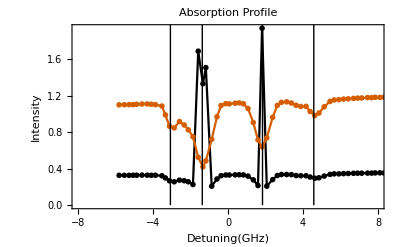

```mathematica
today=DateString["ISODate"]
username=SystemInformation["Kernel","Username"];
If[username=="kahrendsen2",
rbData=FileNameJoin[{"\\\\129.93.33.132\\PiShare","RbData"}];,
Abort[];
];
collecting=FileExistsQ[FileNameJoin[{"\\\\129.93.33.132\\PiShare",".takingData"}]];
latestFile=If[collecting,-2,-1]
fn=FileNames[FileNameJoin[{rbData,today,"*.dat"}]];
PlotSignalProfile[fn[[latestFile]]]
```

2021-07-14

-2

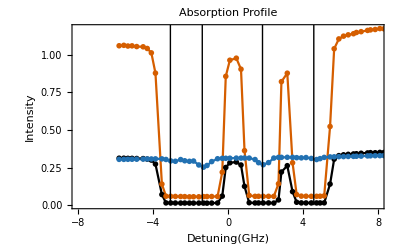

```mathematica
today=DateString["ISODate"]
username=SystemInformation["Kernel","Username"];
If[username=="kahrendsen2",
rbData=FileNameJoin[{"\\\\129.93.33.132\\PiShare","RbData"}];,
Abort[];
];
collecting=FileExistsQ[FileNameJoin[{"\\\\129.93.33.132\\PiShare",".takingData"}]];
latestFile=If[collecting,-2,-1]
fn=FileNames[FileNameJoin[{rbData,today,"RbAbs*.dat"}]];
PlotAllProfiles[fn[[latestFile]]]
```

That was pretty handy, let’s do it for Faraday rotation.

```mathematica
<<faradayRotation`
```

2021-07-14

-2

{\\129.93.33.132\PiShare\RbData\2021-07-14\FDayScan2021-07-14_105012.dat,\\129.93.33.132\PiShare\RbData\2021-07-14\FDayScan2021-07-14_110012.dat,\\129.93.33.132\PiShare\RbData\2021-07-14\FDayScan2021-07-14_111011.dat,\\129.93.33.132\PiShare\RbData\2021-07-14\FDayScan2021-07-14_112011.dat,\\129.93.33.132\PiShare\RbData\2021-07-14\FDayScan2021-07-14_113011.dat}

FittedModel::constr: The property values {ParameterErrors} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

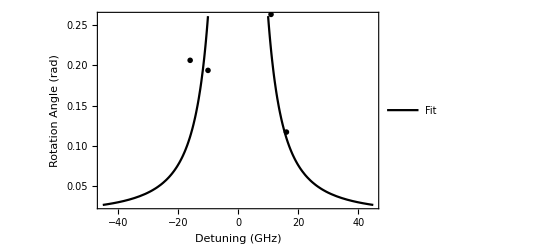
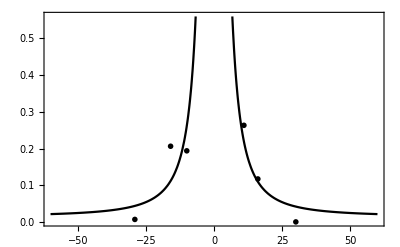
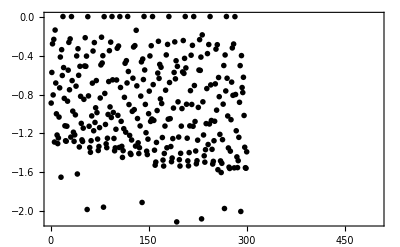
<|RawDetuning→{-29.053,-15.933,-9.993,10.977,16.097,30.037},RawAngles→{0.565845,0.765272,0.752765,-0.748484,0.676135,0.559083},Working Dataset→<|-29.053→<|DETUNING→-29.053,ANGLE→0.0067612,INTENSITY→-0.83799|>,-15.933→<|DETUNING→-15.933,ANGLE→0.206189,INTENSITY→-0.877078|>,-9.993→<|DETUNING→-9.993,ANGLE→0.193681,INTENSITY→-0.893147|>,10.977→<|DETUNING→10.977,ANGLE→0.263229,INTENSITY→-0.944046|>,16.097→<|DETUNING→16.097,ANGLE→0.117051,INTENSITY→-0.910367|>,30.037→<|DETUNING→30.037,ANGLE→0.,INTENSITY→-1.01181|>|>,Detuning→{-29.053,-15.933,-9.993,10.977,16.097,30.037},Angles→{0.0067612,0.206189,0.193681,0.263229,0.117051,0.},Ordered Pairs→{{-29.053,0.0067612},{-15.933,0.206189},{-9.993,0.193681},{10.977,0.263229},{16.097,0.117051},{30.037,0.}},Zero Angle→0.559083,BestFitParameters→{θ0→0.014366,a2→1.73468×10^-10,a4→99742.9},n_Rbx10^12→27.11.,n_RbPercentErr→0.388298,graph→-Graphics-,graphNoLabel→-Graphics-,best fit function→0.014366+(9.97429×10^-14 (377107.+x)^2)/x^4+(1.73468×10^-10 (377107.+x)^2)/x^2,File→/home/pi/RbData/2021-07-14/FDayScan2021-07-14_112011.dat,Comments→Auto faradayScan, tracking density,IonGauge(Torr)→0.000492,CVGauge(Source Foreline)(Torr)→0.187,CVGauge(Target Foreline)(Torr)→0.196,T_res→160.6,T_res_set→0.,T_trg→188.4,T_trg_set→0.,BufferGasLeakValve(-)→45.5,BufferGasType(-)→Ethene,PumpLaserDLCurrent(mA)→167.651,PumpLaserAMPCurrent(mA)→1800,PumpLaserTemp(degC)→20.05,PumpLaserScanOffset(V)→53.4,PumpFrequency(THz)→377.109,PumpPolarizerAngleOuter(deg)→156,PumpPolarizerAngleInner(deg)→0,PumpQWPAngle(step)→160,ProbeCurrent(mA)→65,ProbeLP(deg)→232,ProbeFrequency(THz)→scanning,nominalDensity(cm^-3)→1.1×10^13,magnet1Voltage(V)→70,magnet2Voltage(V)→65.2,magnet3Voltage(V)→65.,WavemeterOffset(GHz)→1.3,Revolutions→1,DataPointsPerRev→50.,NumVolts→6,StepSize→7,Time→ExtractTimeInfoFromFileNameString[/home/pi/RbData/2021-07-14/FDayScan2021-07-14_112011.dat],allRawDataPlot→-Graphics-,allRawData→{-0.887427,-0.572026,-0.277235,-0.803539,-0.23136,-1.2887,-0.135412,-0.680874,-0.998031,-1.21657,-1.30496,-1.24679,-1.03139,-0.730566,-0.413181,-1.65089,-0.33746,-0.603475,0.004046,-0.521877,-0.83888,-1.12138,-1.27572,-1.28023,-1.12581,-0.867962,-0.548592,-0.262427,-0.750412,-0.226246,-1.23779,0.003282,-0.65599,-0.970628,-1.18741,-1.28183,-1.21489,-1.00864,-0.713162,-0.402036,-1.61799,-0.327843,-0.601414,-1.33954,-0.5089,-0.818042,-1.09657,-1.26626,-1.28275,-1.14573,-0.849032,-0.505465,-0.214338,-0.508671,-0.403792,-1.98347,0.002595,-0.813691,-1.12627,-1.34549,-1.39434,-1.27511,-1.01963,-0.682096,-0.351276,-1.17275,-0.264335,-1.0868,-0.935897,-0.655532,-0.985665,-1.25817,-1.37602,-1.33427,-1.14016,-0.83514,-0.49455,-0.209071,-0.474551,-0.399441,-1.95958,0.002824,-0.788043,-1.10757,-1.30702,-1.34686,-1.24947,-1.00467,-0.665761,-0.347689,-0.926814,-0.259755,-1.03597,0.003817,-0.647976,-0.984215,-1.25176,-1.379,-1.34877,-1.15718,-0.649655,-0.322957,-1.01429,-0.299905,-1.34465,0.00313,-0.726826,-1.07558,-1.33305,-1.44701,-1.37755,-1.1513,-0.828117,-0.477452,-1.18726,-0.450736,-0.680187,0.004351,-0.561874,-0.902769,-1.22061,-1.40442,-1.41686,-1.26771,-0.972689,-0.631183,-0.309981,-0.954827,-0.295936,-1.33053,-0.137702,-0.710186,-1.04658,-1.29679,-1.40724,-1.34717,-1.12291,-0.815599,-0.463178,-1.91103,-0.433561,-0.645075,0.004656,-0.546608,-0.90109,-1.19252,-1.38305,-1.41778,-1.25885,-0.996657,-0.76461,-0.40196,-1.0765,-0.296699,-1.05162,0.003664,-0.697133,-1.06604,-1.37266,-1.52731,-1.49495,-1.29259,-0.964369,-0.578591,-0.251053,-0.633168,-0.488978,-0.844376,-0.518671,-0.89193,-1.24229,-1.47457,-1.53601,-1.40648,-1.12413,-0.754839,-0.39135,-1.34801,-0.283112,-1.05322,0.00374,-0.675531,-1.04788,-1.33488,-1.49128,-1.45319,-1.25321,-0.93895,-0.572026,-0.25716,-0.6379,-0.451499,-2.11117,-0.509206,-0.874679,-1.23756,-1.47067,-1.53594,-1.4048,-1.12497,-0.944141,-0.566759,-0.24342,-0.581568,-0.42692,0.004351,-0.525235,-0.89964,-1.24924,-1.48266,-1.53426,-1.3974,-1.12215,-0.759572,-0.39448,-0.901548,-0.292807,-1.12642,0.00374,-0.706598,-1.07734,-1.38083,-1.51311,-1.48113,-1.26954,-0.931852,-0.547371,-0.234337,-0.550653,-0.413868,-2.08003,-0.185027,-0.874603,-1.21596,-1.43075,-1.49602,-1.36732,-1.09886,-0.738123,-0.378068,-1.31412,-0.284486,-1.10268,0.003664,-0.700339,-1.06681,-1.36389,-1.51525,-1.48754,-1.27542,-1.07474,-0.689729,-0.331659,-0.960323,-0.286395,-1.57364,-0.624084,-0.821553,-1.20977,-1.48304,-1.60257,-1.50762,-1.2642,-0.898495,-0.500809,-1.97347,-0.391961,-0.762549,0.004122,-0.631641,-1.02032,-1.34954,-1.54731,-1.56105,-1.38266,-1.05856,-0.671638,-0.319446,-0.807813,-0.279143,-1.55464,0.002748,-0.798959,-1.17268,-1.44159,-1.5522,-1.48052,-1.24031,-0.879412,-0.501649,-2.00392,-0.398602,-0.727513,-0.77896,-0.621794,-1.01521,-1.34236,-1.55326,-1.55861,-1.38938}|>

```mathematica
today=DateString["ISODate"]
username=SystemInformation["Kernel","Username"];
If[username=="kahrendsen2",
rbData=FileNameJoin[{"\\\\129.93.33.132\\PiShare","RbData"}];,
Abort[];
];
collecting=FileExistsQ[FileNameJoin[{"\\\\129.93.33.132\\PiShare",".takingData"}]];
latestFile=If[collecting,-2,-1]
fn=FileNames[FileNameJoin[{rbData,today,"FDayScan*.dat"}]]
ProcessFaradayRotationNumberDensityFile[fn[[latestFile]]]
```

```mathematica
res=%
```

<|RawDetuning→{-29.053,-15.933,-9.993,10.977,16.097,30.037},RawAngles→{0.565845,0.765272,0.752765,-0.748484,0.676135,0.559083},Working Dataset→<|-29.053→<|DETUNING→-29.053,ANGLE→0.0067612,INTENSITY→-0.83799|>,-15.933→<|DETUNING→-15.933,ANGLE→0.206189,INTENSITY→-0.877078|>,-9.993→<|DETUNING→-9.993,ANGLE→0.193681,INTENSITY→-0.893147|>,10.977→<|DETUNING→10.977,ANGLE→0.263229,INTENSITY→-0.944046|>,16.097→<|DETUNING→16.097,ANGLE→0.117051,INTENSITY→-0.910367|>,30.037→<|DETUNING→30.037,ANGLE→0.,INTENSITY→-1.01181|>|>,Detuning→{-29.053,-15.933,-9.993,10.977,16.097,30.037},Angles→{0.0067612,0.206189,0.193681,0.263229,0.117051,0.},Ordered Pairs→{{-29.053,0.0067612},{-15.933,0.206189},{-9.993,0.193681},{10.977,0.263229},{16.097,0.117051},{30.037,0.}},Zero Angle→0.559083,BestFitParameters→{θ0→0.014366,a2→1.73468×10^-10,a4→99742.9},n_Rbx10^12→27.11.,n_RbPercentErr→0.388298,graph→-Graphics-,graphNoLabel→-Graphics-,best fit function→0.014366+(9.97429×10^-14 (377107.+x)^2)/x^4+(1.73468×10^-10 (377107.+x)^2)/x^2,File→/home/pi/RbData/2021-07-14/FDayScan2021-07-14_112011.dat,Comments→Auto faradayScan, tracking density,IonGauge(Torr)→0.000492,CVGauge(Source Foreline)(Torr)→0.187,CVGauge(Target Foreline)(Torr)→0.196,T_res→160.6,T_res_set→0.,T_trg→188.4,T_trg_set→0.,BufferGasLeakValve(-)→45.5,BufferGasType(-)→Ethene,PumpLaserDLCurrent(mA)→167.651,PumpLaserAMPCurrent(mA)→1800,PumpLaserTemp(degC)→20.05,PumpLaserScanOffset(V)→53.4,PumpFrequency(THz)→377.109,PumpPolarizerAngleOuter(deg)→156,PumpPolarizerAngleInner(deg)→0,PumpQWPAngle(step)→160,ProbeCurrent(mA)→65,ProbeLP(deg)→232,ProbeFrequency(THz)→scanning,nominalDensity(cm^-3)→1.1×10^13,magnet1Voltage(V)→70,magnet2Voltage(V)→65.2,magnet3Voltage(V)→65.,WavemeterOffset(GHz)→1.3,Revolutions→1,DataPointsPerRev→50.,NumVolts→6,StepSize→7,Time→ExtractTimeInfoFromFileNameString[/home/pi/RbData/2021-07-14/FDayScan2021-07-14_112011.dat],allRawDataPlot→-Graphics-,allRawData→{-0.887427,-0.572026,-0.277235,-0.803539,-0.23136,-1.2887,-0.135412,-0.680874,-0.998031,-1.21657,-1.30496,-1.24679,-1.03139,-0.730566,-0.413181,-1.65089,-0.33746,-0.603475,0.004046,-0.521877,-0.83888,-1.12138,-1.27572,-1.28023,-1.12581,-0.867962,-0.548592,-0.262427,-0.750412,-0.226246,-1.23779,0.003282,-0.65599,-0.970628,-1.18741,-1.28183,-1.21489,-1.00864,-0.713162,-0.402036,-1.61799,-0.327843,-0.601414,-1.33954,-0.5089,-0.818042,-1.09657,-1.26626,-1.28275,-1.14573,-0.849032,-0.505465,-0.214338,-0.508671,-0.403792,-1.98347,0.002595,-0.813691,-1.12627,-1.34549,-1.39434,-1.27511,-1.01963,-0.682096,-0.351276,-1.17275,-0.264335,-1.0868,-0.935897,-0.655532,-0.985665,-1.25817,-1.37602,-1.33427,-1.14016,-0.83514,-0.49455,-0.209071,-0.474551,-0.399441,-1.95958,0.002824,-0.788043,-1.10757,-1.30702,-1.34686,-1.24947,-1.00467,-0.665761,-0.347689,-0.926814,-0.259755,-1.03597,0.003817,-0.647976,-0.984215,-1.25176,-1.379,-1.34877,-1.15718,-0.649655,-0.322957,-1.01429,-0.299905,-1.34465,0.00313,-0.726826,-1.07558,-1.33305,-1.44701,-1.37755,-1.1513,-0.828117,-0.477452,-1.18726,-0.450736,-0.680187,0.004351,-0.561874,-0.902769,-1.22061,-1.40442,-1.41686,-1.26771,-0.972689,-0.631183,-0.309981,-0.954827,-0.295936,-1.33053,-0.137702,-0.710186,-1.04658,-1.29679,-1.40724,-1.34717,-1.12291,-0.815599,-0.463178,-1.91103,-0.433561,-0.645075,0.004656,-0.546608,-0.90109,-1.19252,-1.38305,-1.41778,-1.25885,-0.996657,-0.76461,-0.40196,-1.0765,-0.296699,-1.05162,0.003664,-0.697133,-1.06604,-1.37266,-1.52731,-1.49495,-1.29259,-0.964369,-0.578591,-0.251053,-0.633168,-0.488978,-0.844376,-0.518671,-0.89193,-1.24229,-1.47457,-1.53601,-1.40648,-1.12413,-0.754839,-0.39135,-1.34801,-0.283112,-1.05322,0.00374,-0.675531,-1.04788,-1.33488,-1.49128,-1.45319,-1.25321,-0.93895,-0.572026,-0.25716,-0.6379,-0.451499,-2.11117,-0.509206,-0.874679,-1.23756,-1.47067,-1.53594,-1.4048,-1.12497,-0.944141,-0.566759,-0.24342,-0.581568,-0.42692,0.004351,-0.525235,-0.89964,-1.24924,-1.48266,-1.53426,-1.3974,-1.12215,-0.759572,-0.39448,-0.901548,-0.292807,-1.12642,0.00374,-0.706598,-1.07734,-1.38083,-1.51311,-1.48113,-1.26954,-0.931852,-0.547371,-0.234337,-0.550653,-0.413868,-2.08003,-0.185027,-0.874603,-1.21596,-1.43075,-1.49602,-1.36732,-1.09886,-0.738123,-0.378068,-1.31412,-0.284486,-1.10268,0.003664,-0.700339,-1.06681,-1.36389,-1.51525,-1.48754,-1.27542,-1.07474,-0.689729,-0.331659,-0.960323,-0.286395,-1.57364,-0.624084,-0.821553,-1.20977,-1.48304,-1.60257,-1.50762,-1.2642,-0.898495,-0.500809,-1.97347,-0.391961,-0.762549,0.004122,-0.631641,-1.02032,-1.34954,-1.54731,-1.56105,-1.38266,-1.05856,-0.671638,-0.319446,-0.807813,-0.279143,-1.55464,0.002748,-0.798959,-1.17268,-1.44159,-1.5522,-1.48052,-1.24031,-0.879412,-0.501649,-2.00392,-0.398602,-0.727513,-0.77896,-0.621794,-1.01521,-1.34236,-1.55326,-1.55861,-1.38938}|>

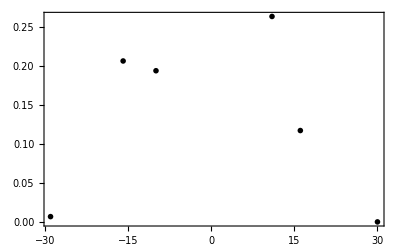

```mathematica
ListPlot[res["Ordered Pairs"],PlotRange->Full]
```

```mathematica
res["Ordered Pairs"]
```

{{-29.053,0.0067612},{-15.933,0.206189},{-9.993,0.193681},{10.977,0.263229},{16.097,0.117051},{30.037,0.}}

```mathematica
op={{-29.053000000014435,0.006761203519235148},{-15.932999999960884,0.20618866460166785},{-9.993000000016764,0.19368122646783836},{10.977000000013504,0.26322910388699583},{16.097000000008848,0.117051480336123},{30.037000000011176,0.}}
```

{{-29.053,0.0067612},{-15.933,0.206189},{-9.993,0.193681},{10.977,0.263229},{16.097,0.117051},{30.037,0.}}

```mathematica
op=%
ListPlot[op,PlotRange->Full]
```

{{-29.053,0.0067612},{-15.933,0.206189},{-9.993,0.193681},{10.977,0.263229},{16.097,0.117051},{30.037,0.}}

-Graphics-

```mathematica
nlmFit=CalculateFittingParameters[op]
```

FittedModel[0.014366+(9.97429×10^-14 (377107.+δ)^2)/δ^4+(1.73468×10^-10 (377107.+δ)^2)/δ^2]

```mathematica
fn[[latestFile-1]]
```

\\129.93.33.132\PiShare\RbData\2021-07-14\FDayScan2021-07-14_111011.dat

```mathematica
fileName=fn[[latestFile]]
importedFile=ImportFile[fileName];
header=importedFile[[1]];
m1=ToExpression[header[m1CT]];
m2=ToExpression[header[m2CT]];
magneticField=CalculateIntegratedMagneticField[m1,m2];
a2Val=a2/.nlmFit["BestFitParameters"]
a2PosInPar=Position[Keys[nlmFit["BestFitParameters"]],a2][[1,1]]; (* The position of a2 in the list of parameters *)
a2err=nlmFit["ParameterErrors"][[a2PosInPar]];
n=Around[CalculateNumberDensity[a2Val,magneticField],CalculateNumberDensity[a2err,magneticField]]
```

\\129.93.33.132\PiShare\RbData\2021-07-14\FDayScan2021-07-14_110012.dat

1.43989×10^-10

FittedModel::constr: The property values {ParameterErrors} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

2.30.410^13

```mathematica
densityWrapFixer[angle_]:=If[angle<-0.5,angle+Pi/2,angle];
Dataset[res["Working Dataset"]][All,{"ANGLE"->densityWrapFixer}]
```

```mathematica
SetDirectory[FileNameJoin[{$DATARUNS,"2021","07","14","124115"}]]
```

C:\Users\kahrendsen2\OneDrive - University of Nebraska-Lincoln\Gay Group\Project - Rb Spin Filter\karl\DataRuns\2021\07\14\124115

```mathematica
FileNames[]
```

{EX2021-07-14_131523_counts.png,EX2021-07-14_131523_current.png,EX2021-07-14_131523.dat,EX2021-07-14_131646_counts.png,EX2021-07-14_131646_current.png,EX2021-07-14_131646.dat,FDayScan2021-07-14_125404.dat,FDayScan2021-07-14_130101.dat,FDayScan2021-07-14_130800.dat,FDayScanX2021-07-14_125404.dat,FDayScanX2021-07-14_130101.dat,FDayScanX2021-07-14_130800.dat,POL2021-07-14_124115.dat,POL2021-07-14_124200.dat,POL2021-07-14_124243.dat,POL2021-07-14_124356.dat,POL2021-07-14_124440.dat,POL2021-07-14_124525.dat,POL2021-07-14_124638.dat,POL2021-07-14_124722.dat,POL2021-07-14_124806.dat,POL2021-07-14_124919.dat,POL2021-07-14_125004.dat,POL2021-07-14_125048.dat,POL2021-07-14_125201.dat,POL2021-07-14_125247.dat,POL2021-07-14_125330.dat}

```mathematica
im=ImportFile["FDayScanX2021-07-14_125404.dat"];
```

```mathematica
dat=im[[2]][[1]][All,{"STEP","PUMP"}]
```

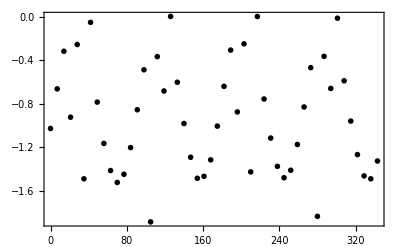

```mathematica
ListPlot[dat]
```

```mathematica
dat[[All,2]]//Normal
```

```mathematica
dat={-1.025968,-0.661868,-0.316011,-0.0922081,-0.0253649,-.1488459`,-0.50455,-0.783387,-1.163135,-1.412509,-1.521815,-1.446705,-1.201377,-0.853688,-0.486077,-.1884465`,-0.0365245,-0.00680951,-0.03969,-0.600498,-0.980169,-1.290226,-1.483497,-1.465559,-1.314271,-1.004137,-0.638511,-0.305248,-0.873534,-0.247695,-1.424493,0.003511,-0.754687,-1.113825,-1.373886,-1.478765,-1.409685,-1.173058,-0.827965,-0.46646,-.1833247`,-0.0362726,-0.0657899,-0.11984,-0.587292,-0.957728,-1.265648,-1.461743,-1.488382,-1.324881};
```

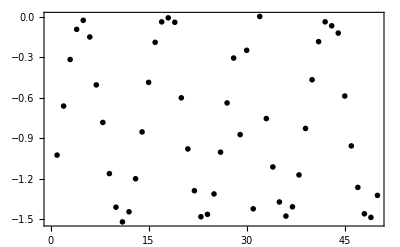

```mathematica
ListPlot[dat]
```

```mathematica
DFT[dat[[All,2]]//Normal]
```

<|Sin Coefficients→<|0→0.,1→-0.0177331,2→-0.0045737,3→-0.00292472,4→0.371692,5→-0.000836312,6→0.123127,7→0.00147462,8→0.061255,9→0.00414354,10→0.0196611,11→-0.00136581,12→0.0776812,13→-0.000249217,14→-0.125763,15→0.000958378,16→0.116109,17→0.00135007,18→0.00582421,19→-0.00220194,20→0.0174965,21→-0.00704811,22→-0.107191,23→0.00064491,24→-0.257724,25→0.|>,Cos Coefficients→<|0→-0.933761,1→-0.00875057,2→0.0568286,3→0.00216131,4→-0.225002,5→-0.000888582,6→0.0396433,7→-0.00359425,8→0.23193,9→-0.000973294,10→-0.168824,11→0.00159744,12→-0.0256503,13→0.00140402,14→0.0258868,15→0.00163066,16→0.0392788,17→-0.00233276,18→-0.00684699,19→-0.00132128,20→-0.257339,21→-0.00113257,22→0.124961,23→-0.000759748,24→0.0838431,25→0.00204412|>|>

```mathematica
fit=FourierFit[Abs[dat[[All,2]]//Normal],1]
```

FittedModel[2.98647+0.137796 Cos[2 (-61.7026+θ)]+0.0119342 Cos[4 (-61.7026+θ)]-0.238982 Sin[2 (-61.7026+θ)]-0.185591 Sin[4 (-61.7026+θ)]]

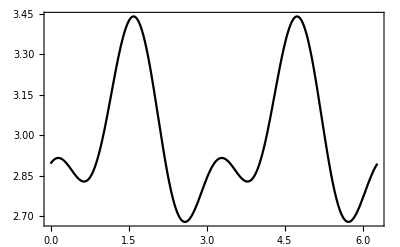

```mathematica
pl=Plot[fit[x],{x,0,2π}]
```

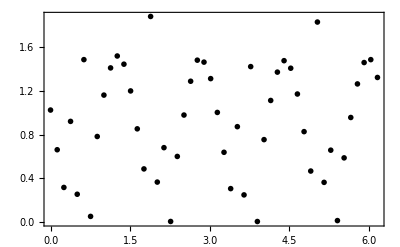

```mathematica
lp=ListPlot[Transpose[{Range[0,2Pi-2Pi/50,2Pi/50],Abs[dat[[All,2]]//Normal]}]]
```

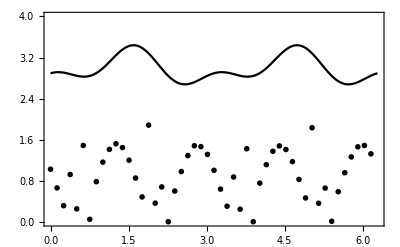

```mathematica
Show[lp,pl,PlotRange->{0,4}]
```

2021-07-14

-1

{\\129.93.33.132\PiShare\RbData\2021-07-14\FDayScan2021-07-14_105012.dat,\\129.93.33.132\PiShare\RbData\2021-07-14\FDayScan2021-07-14_110012.dat,\\129.93.33.132\PiShare\RbData\2021-07-14\FDayScan2021-07-14_111011.dat,\\129.93.33.132\PiShare\RbData\2021-07-14\FDayScan2021-07-14_112011.dat,\\129.93.33.132\PiShare\RbData\2021-07-14\FDayScan2021-07-14_113011.dat,\\129.93.33.132\PiShare\RbData\2021-07-14\FDayScan2021-07-14_114012.dat,\\129.93.33.132\PiShare\RbData\2021-07-14\FDayScan2021-07-14_115011.dat,\\129.93.33.132\PiShare\RbData\2021-07-14\FDayScan2021-07-14_120012.dat,\\129.93.33.132\PiShare\RbData\2021-07-14\FDayScan2021-07-14_125404.dat,\\129.93.33.132\PiShare\RbData\2021-07-14\FDayScan2021-07-14_130101.dat,\\129.93.33.132\PiShare\RbData\2021-07-14\FDayScan2021-07-14_130800.dat,\\129.93.33.132\PiShare\RbData\2021-07-14\FDayScan2021-07-14_133133.dat,\\129.93.33.132\PiShare\RbData\2021-07-14\FDayScan2021-07-14_133832.dat,\\129.93.33.132\PiShare\RbData\2021-07-14\FDayScan2021-07-14_134600.dat,\\129.93.33.132\PiShare\RbData\2021-07-14\FDayScan2021-07-14_142420.dat,\\129.93.33.132\PiShare\RbData\2021-07-14\FDayScan2021-07-14_143114.dat,\\129.93.33.132\PiShare\RbData\2021-07-14\FDayScan2021-07-14_143811.dat,\\129.93.33.132\PiShare\RbData\2021-07-14\FDayScan2021-07-14_145117.dat,\\129.93.33.132\PiShare\RbData\2021-07-14\FDayScan2021-07-14_150012.dat}

FittedModel::constr: The property values {ParameterErrors} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

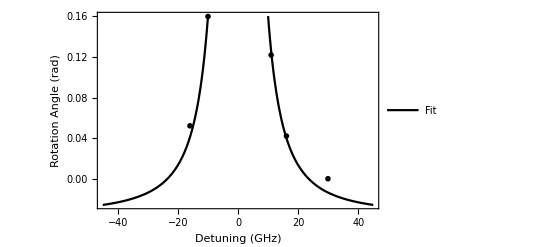
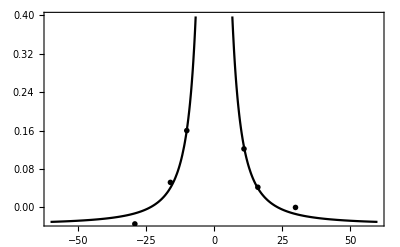
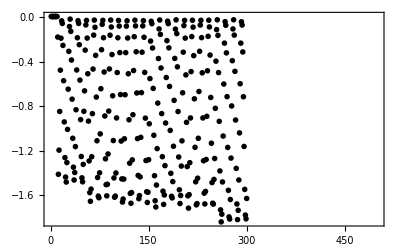
<|RawDetuning→{-29.053,-15.993,-9.993,11.007,16.097,29.917},RawAngles→{0.563192,0.649656,0.757453,0.719431,0.639565,0.597501},Working Dataset→<|-29.053→<|DETUNING→-29.053,ANGLE→-0.0343087,INTENSITY→-0.603487|>,-15.993→<|DETUNING→-15.993,ANGLE→0.0521552,INTENSITY→-0.826107|>,-9.993→<|DETUNING→-9.993,ANGLE→0.159952,INTENSITY→-0.845634|>,11.007→<|DETUNING→11.007,ANGLE→0.12193,INTENSITY→-0.851743|>,16.097→<|DETUNING→16.097,ANGLE→0.0420635,INTENSITY→-0.859673|>,29.917→<|DETUNING→29.917,ANGLE→0.,INTENSITY→-0.932725|>|>,Detuning→{-29.053,-15.993,-9.993,11.007,16.097,29.917},Angles→{-0.0343087,0.0521552,0.159952,0.12193,0.0420635,0.},Ordered Pairs→{{-29.053,-0.0343087},{-15.993,0.0521552},{-9.993,0.159952},{11.007,0.12193},{16.097,0.0420635},{29.917,0.}},Zero Angle→0.597501,BestFitParameters→{θ0→-0.0355105,a2→1.37678×10^-10,a4→99982.1},n_Rbx10^12→21.72.2,n_RbPercentErr→0.102546,graph→-Graphics-,graphNoLabel→-Graphics-,best fit function→-0.0355105+(9.99821×10^-14 (377107.+x)^2)/x^4+(1.37678×10^-10 (377107.+x)^2)/x^2,File→/home/pi/RbData/2021-07-14/FDayScan2021-07-14_150012.dat,Comments→Auto faradayScan, tracking density,IonGauge(Torr)→0.00254,CVGauge(Source Foreline)(Torr)→0.244,CVGauge(Target Foreline)(Torr)→0.651,T_res→158.8,T_res_set→0.,T_trg→191.8,T_trg_set→0.,BufferGasLeakValve(-)→45.5,BufferGasType(-)→Ethene,PumpLaserDLCurrent(mA)→167.651,PumpLaserAMPCurrent(mA)→1800,PumpLaserTemp(degC)→20.05,PumpLaserScanOffset(V)→53.4,PumpFrequency(THz)→377.109,PumpPolarizerAngleOuter(deg)→156,PumpPolarizerAngleInner(deg)→0,PumpQWPAngle(step)→72,ProbeCurrent(mA)→65,ProbeLP(deg)→232,ProbeFrequency(THz)→scanning,nominalDensity(cm^-3)→1.1×10^13,magnet1Voltage(V)→70,magnet2Voltage(V)→65.2,magnet3Voltage(V)→65.,WavemeterOffset(GHz)→1.3,Revolutions→1,DataPointsPerRev→50.,NumVolts→6,StepSize→7,Time→Wed 14 Jul 2021 15:00:12GMT-5,allRawDataPlot→-Graphics-,allRawData→{0.00687,0.006564,0.00687,0.006183,0.006335,0.007099,0.006946,0.006946,0.006946,0.006412,-0.178386,-1.41335,-1.19596,-0.847963,-0.476383,-0.188462,-0.032364,-0.055951,-0.253267,-0.571034,-0.942004,-1.26351,-1.43846,-1.48327,-1.30771,-1.00918,-0.647136,-0.306928,-0.083506,-0.016869,-0.126862,-0.385167,-0.73736,-1.08932,-1.34946,-1.46503,-1.39724,-1.16398,-0.832545,-0.474704,-0.184569,-0.030761,-0.05534,-0.246855,-0.565614,-0.921242,-1.25321,-1.44533,-1.48105,-1.32419,-0.846819,-0.662555,-0.295936,-0.069385,-0.028701,-0.187469,-0.508519,-0.934676,-1.29343,-1.57838,-1.65639,-1.54693,-1.25565,-0.867733,-0.466078,-0.16083,-0.025495,-0.090452,-0.343262,-0.718429,-1.11161,-1.44243,-1.6096,-1.62471,-1.39992,-1.04971,-0.643396,-0.292349,-0.063431,-0.02809,-0.184416,-0.493023,-0.888724,-1.27404,-1.50678,-1.60738,-1.50304,-1.23054,-0.844987,-0.465391,-0.16167,-0.025266,-0.087781,-0.335628,-0.706903,-1.10978,-1.44632,-1.61998,-1.60967,-1.40167,-0.906128,-0.497603,-0.184722,-0.028777,-0.079995,-0.318454,-0.695835,-1.11413,-1.45503,-1.66333,-1.63601,-1.45655,-1.09398,-0.697438,-0.318606,-0.080071,-0.031601,-0.186859,-0.508442,-0.922844,-1.31351,-1.58555,-1.67417,-1.57822,-1.28351,-0.877427,-0.479742,-0.17518,-0.026105,-0.078163,-0.310744,-0.681485,-1.09238,-1.42358,-1.63326,-1.60502,-1.43663,-1.08062,-0.678279,-0.314637,-0.077782,-0.030685,-0.180218,-0.496153,-0.908112,-1.28985,-1.57029,-1.66692,-1.57494,-1.28214,-0.958796,-0.551951,-0.214567,-0.036486,-0.058012,-0.27693,-0.640343,-1.06238,-1.42633,-1.65158,-1.70784,-1.51021,-1.18245,-0.772625,-0.371657,-0.105108,-0.024579,-0.154265,-0.456384,-0.867275,-1.25496,-1.5654,-1.6844,-1.59967,-1.33557,-0.95185,-0.542333,-0.210445,-0.035341,-0.057554,-0.275403,-0.622557,-1.01811,-1.40465,-1.61151,-1.62586,-1.47915,-1.16115,-0.747817,-0.370435,-0.106635,-0.023586,-0.14709,-0.446309,-0.848574,-1.25771,-1.55273,-1.67677,-1.60441,-1.33946,-1.1123,-0.679806,-0.314485,-0.075034,-0.028395,-0.187851,-0.518747,-0.945896,-1.34396,-1.60708,-1.71791,-1.59654,-1.3087,-0.906357,-0.489283,-0.174264,-0.027021,-0.089231,-0.345399,-0.73423,-1.17046,-1.48113,-1.68852,-1.67784,-1.44854,-1.0894,-0.668203,-0.306699,-0.070225,-0.027708,-0.183729,-0.500351,-0.906357,-1.2916,-1.58349,-1.68036,-1.56792,-1.2803,-0.891854,-0.48165,-0.171669,-0.026792,-0.087323,-0.340514,-0.721864,-1.13367,-1.488,-1.67364,-1.68173,-1.45961,-1.2713,-0.819645,-0.395472,-0.111215,-0.023052,-0.162967,-0.498137,-0.936508,-1.3832,-1.73341,-1.84187,-1.77241,-1.48228,-1.0694,-0.601337,-0.232963,-0.039845,-0.07198,-0.320515,-0.714613,-1.17168,-1.55777,-1.79676,-1.81661,-1.64028,-1.26756,-0.798424,-0.391045,-0.105108,-0.022823,-0.160983,-0.487069,-0.925058,-1.36015,-1.68058,-1.82142,-1.7376,-1.46457,-1.04078,-0.59836,-0.233192,-0.040761,-0.069996,-0.312195,-0.715605,-1.16306,-1.54907,-1.7805,-1.81424,-1.63089}|>

```mathematica
today=DateString["ISODate"]
username=SystemInformation["Kernel","Username"];
If[username=="kahrendsen2",
rbData=FileNameJoin[{"\\\\129.93.33.132\\PiShare","RbData"}];,
Abort[];
];
collecting=FileExistsQ[FileNameJoin[{"\\\\129.93.33.132\\PiShare",".takingData"}]];
latestFile=If[collecting,-2,-1]
fn=FileNames[FileNameJoin[{rbData,today,"FDayScan*.dat"}]]
ProcessFaradayRotationNumberDensityFile[fn[[latestFile]]]
```

2021-07-14

-1

{\\129.93.33.132\PiShare\RbData\2021-07-14\FDayScan2021-07-14_105012.dat,\\129.93.33.132\PiShare\RbData\2021-07-14\FDayScan2021-07-14_110012.dat,\\129.93.33.132\PiShare\RbData\2021-07-14\FDayScan2021-07-14_111011.dat,\\129.93.33.132\PiShare\RbData\2021-07-14\FDayScan2021-07-14_112011.dat,\\129.93.33.132\PiShare\RbData\2021-07-14\FDayScan2021-07-14_113011.dat,\\129.93.33.132\PiShare\RbData\2021-07-14\FDayScan2021-07-14_114012.dat,\\129.93.33.132\PiShare\RbData\2021-07-14\FDayScan2021-07-14_115011.dat,\\129.93.33.132\PiShare\RbData\2021-07-14\FDayScan2021-07-14_120012.dat,\\129.93.33.132\PiShare\RbData\2021-07-14\FDayScan2021-07-14_125404.dat,\\129.93.33.132\PiShare\RbData\2021-07-14\FDayScan2021-07-14_130101.dat,\\129.93.33.132\PiShare\RbData\2021-07-14\FDayScan2021-07-14_130800.dat,\\129.93.33.132\PiShare\RbData\2021-07-14\FDayScan2021-07-14_133133.dat,\\129.93.33.132\PiShare\RbData\2021-07-14\FDayScan2021-07-14_133832.dat,\\129.93.33.132\PiShare\RbData\2021-07-14\FDayScan2021-07-14_134600.dat,\\129.93.33.132\PiShare\RbData\2021-07-14\FDayScan2021-07-14_142420.dat,\\129.93.33.132\PiShare\RbData\2021-07-14\FDayScan2021-07-14_143114.dat,\\129.93.33.132\PiShare\RbData\2021-07-14\FDayScan2021-07-14_143811.dat,\\129.93.33.132\PiShare\RbData\2021-07-14\FDayScan2021-07-14_145117.dat,\\129.93.33.132\PiShare\RbData\2021-07-14\FDayScan2021-07-14_150012.dat,\\129.93.33.132\PiShare\RbData\2021-07-14\FDayScan2021-07-14_151012.dat}

FittedModel::constr: The property values {ParameterErrors} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

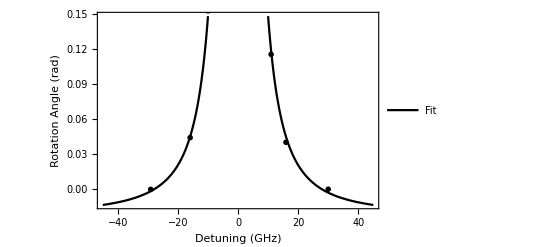
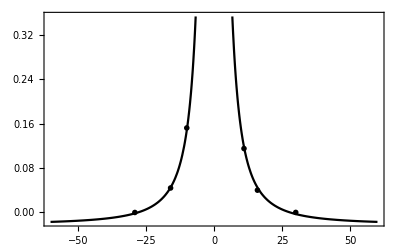
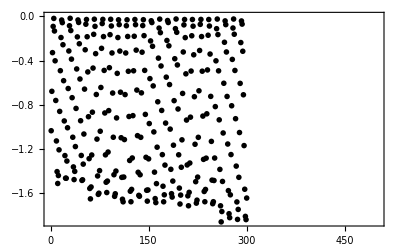
<|RawDetuning→{-29.053,-15.933,-9.993,11.007,15.947,30.007},RawAngles→{0.597335,0.641534,0.749902,0.712731,0.63756,0.597469},Working Dataset→<|-29.053→<|DETUNING→-29.053,ANGLE→-0.000134235,INTENSITY→-0.754534|>,-15.933→<|DETUNING→-15.933,ANGLE→0.0440647,INTENSITY→-0.824432|>,-9.993→<|DETUNING→-9.993,ANGLE→0.152433,INTENSITY→-0.844816|>,11.007→<|DETUNING→11.007,ANGLE→0.115262,INTENSITY→-0.85045|>,15.947→<|DETUNING→15.947,ANGLE→0.0400904,INTENSITY→-0.860198|>,30.007→<|DETUNING→30.007,ANGLE→0.,INTENSITY→-0.933474|>|>,Detuning→{-29.053,-15.933,-9.993,11.007,15.947,30.007},Angles→{-0.000134235,0.0440647,0.152433,0.115262,0.0400904,0.},Ordered Pairs→{{-29.053,-0.000134235},{-15.933,0.0440647},{-9.993,0.152433},{11.007,0.115262},{15.947,0.0400904},{30.007,0.}},Zero Angle→0.597469,BestFitParameters→{θ0→-0.0218409,a2→1.19385×10^-10,a4→100016.},n_Rbx10^12→18.80.6,n_RbPercentErr→0.032962,graph→-Graphics-,graphNoLabel→-Graphics-,best fit function→-0.0218409+(1.00016×10^-13 (377107.+x)^2)/x^4+(1.19385×10^-10 (377107.+x)^2)/x^2,File→/home/pi/RbData/2021-07-14/FDayScan2021-07-14_151012.dat,Comments→Auto faradayScan, tracking density,IonGauge(Torr)→0.00252,CVGauge(Source Foreline)(Torr)→0.246,CVGauge(Target Foreline)(Torr)→0.66,T_res→158.5,T_res_set→0.,T_trg→191.6,T_trg_set→0.,BufferGasLeakValve(-)→45.5,BufferGasType(-)→Ethene,PumpLaserDLCurrent(mA)→167.651,PumpLaserAMPCurrent(mA)→1800,PumpLaserTemp(degC)→20.05,PumpLaserScanOffset(V)→53.4,PumpFrequency(THz)→377.109,PumpPolarizerAngleOuter(deg)→156,PumpPolarizerAngleInner(deg)→0,PumpQWPAngle(step)→72,ProbeCurrent(mA)→65,ProbeLP(deg)→232,ProbeFrequency(THz)→scanning,nominalDensity(cm^-3)→1.1×10^13,magnet1Voltage(V)→70,magnet2Voltage(V)→65.2,magnet3Voltage(V)→65.,WavemeterOffset(GHz)→1.3,Revolutions→1,DataPointsPerRev→50.,NumVolts→6,StepSize→7,Time→Wed 14 Jul 2021 15:10:12GMT-5,allRawDataPlot→-Graphics-,allRawData→{-1.03322,-0.676905,-0.327156,-0.089918,-0.017709,-0.131366,-0.400968,-0.759648,-1.12573,-1.40289,-1.51014,-1.43839,-1.20603,-0.858344,-0.490352,-0.190599,-0.032364,-0.055951,-0.255633,-0.580881,-0.944751,-1.25802,-1.4622,-1.46304,-1.3074,-1.00643,-0.651487,-0.312195,-0.084117,-0.01664,-0.12732,-0.386007,-0.734459,-1.09215,-1.36045,-1.47518,-1.40083,-1.17649,-0.831476,-0.474704,-0.184645,-0.031601,-0.054195,-0.246855,-0.565462,-0.942919,-1.25687,-1.48235,-1.47701,-1.33526,-1.06314,-0.656983,-0.301203,-0.070148,-0.027403,-0.183424,-0.501649,-0.90651,-1.28572,-1.55548,-1.64929,-1.54174,-1.25275,-0.865672,-0.466765,-0.161517,-0.024808,-0.08946,-0.336392,-0.705529,-1.10909,-1.4422,-1.60868,-1.5983,-1.39411,-1.03788,-0.642098,-0.28815,-0.064271,-0.026487,-0.18205,-0.487833,-0.872695,-1.25145,-1.49915,-1.59219,-1.48854,-1.22611,-0.851398,-0.463254,-0.164646,-0.025647,-0.086102,-0.330056,-0.692477,-1.09222,-1.43106,-1.62662,-1.60334,-1.39793,-0.917349,-0.514549,-0.190675,-0.030227,-0.073736,-0.312958,-0.68492,-1.09665,-1.45487,-1.65249,-1.67601,-1.45205,-1.11321,-0.706445,-0.330209,-0.083888,-0.030227,-0.180981,-0.495695,-0.904525,-1.30221,-1.58021,-1.67532,-1.56365,-1.27969,-0.896892,-0.491268,-0.178997,-0.027556,-0.074423,-0.304485,-0.665608,-1.07787,-1.40915,-1.61754,-1.62601,-1.43136,-1.09276,-0.690798,-0.32311,-0.082361,-0.029311,-0.173654,-0.48768,-0.885518,-1.27351,-1.57174,-1.66997,-1.56891,-1.28756,-0.968414,-0.562103,-0.221361,-0.038853,-0.055111,-0.269907,-0.627977,-1.04391,-1.40778,-1.64692,-1.68318,-1.51159,-1.18207,-0.77148,-0.376847,-0.105184,-0.024044,-0.14648,-0.447759,-0.849795,-1.24947,-1.5351,-1.6757,-1.61265,-1.34412,-0.96414,-0.548745,-0.217086,-0.036639,-0.054653,-0.26548,-0.615917,-1.01864,-1.38213,-1.6025,-1.63311,-1.48854,-1.16413,-0.76148,-0.38219,-0.110222,-0.023052,-0.143274,-0.438523,-0.836666,-1.25084,-1.55204,-1.69593,-1.61525,-1.36358,-1.11566,-0.695835,-0.321125,-0.076102,-0.027479,-0.191439,-0.518747,-0.936737,-1.34267,-1.62219,-1.71196,-1.59044,-1.32534,-0.910631,-0.493863,-0.174569,-0.027556,-0.087934,-0.34662,-0.725757,-1.15558,-1.49403,-1.68807,-1.66097,-1.45258,-1.09291,-0.672096,-0.307691,-0.071522,-0.026869,-0.181821,-0.494932,-0.900861,-1.29229,-1.58258,-1.67532,-1.56418,-1.28122,-0.880328,-0.483558,-0.169913,-0.027479,-0.086636,-0.339979,-0.722704,-1.12963,-1.47999,-1.69318,-1.67509,-1.48327,-1.28015,-0.815217,-0.401197,-0.110604,-0.023434,-0.163883,-0.491726,-0.934828,-1.38274,-1.71211,-1.8576,-1.76386,-1.49174,-1.0536,-0.604009,-0.233497,-0.040074,-0.074041,-0.321278,-0.723391,-1.15352,-1.57494,-1.78363,-1.81958,-1.6128,-1.24886,-0.807508,-0.388297,-0.10465,-0.023205,-0.16083,-0.488291,-0.924524,-1.35312,-1.67715,-1.83493,-1.74463,-1.45449,-1.04955,-0.605001,-0.236016,-0.040761,-0.069156,-0.314714,-0.708201,-1.16764,-1.56227,-1.8076,-1.83684,-1.64204}|>

```mathematica
today=DateString["ISODate"]
username=SystemInformation["Kernel","Username"];
If[username=="kahrendsen2",
rbData=FileNameJoin[{"\\\\129.93.33.132\\PiShare","RbData"}];,
Abort[];
];
collecting=FileExistsQ[FileNameJoin[{"\\\\129.93.33.132\\PiShare",".takingData"}]];
latestFile=If[collecting,-2,-1]
fn=FileNames[FileNameJoin[{rbData,today,"FDayScan*.dat"}]]
ProcessFaradayRotationNumberDensityFile[fn[[latestFile]]]
```

2021-07-14

-2

{\\129.93.33.132\PiShare\RbData\2021-07-14\FDayScan2021-07-14_105012.dat,\\129.93.33.132\PiShare\RbData\2021-07-14\FDayScan2021-07-14_110012.dat,\\129.93.33.132\PiShare\RbData\2021-07-14\FDayScan2021-07-14_111011.dat,\\129.93.33.132\PiShare\RbData\2021-07-14\FDayScan2021-07-14_112011.dat,\\129.93.33.132\PiShare\RbData\2021-07-14\FDayScan2021-07-14_113011.dat,\\129.93.33.132\PiShare\RbData\2021-07-14\FDayScan2021-07-14_114012.dat,\\129.93.33.132\PiShare\RbData\2021-07-14\FDayScan2021-07-14_115011.dat,\\129.93.33.132\PiShare\RbData\2021-07-14\FDayScan2021-07-14_120012.dat,\\129.93.33.132\PiShare\RbData\2021-07-14\FDayScan2021-07-14_125404.dat,\\129.93.33.132\PiShare\RbData\2021-07-14\FDayScan2021-07-14_130101.dat,\\129.93.33.132\PiShare\RbData\2021-07-14\FDayScan2021-07-14_130800.dat,\\129.93.33.132\PiShare\RbData\2021-07-14\FDayScan2021-07-14_133133.dat,\\129.93.33.132\PiShare\RbData\2021-07-14\FDayScan2021-07-14_133832.dat,\\129.93.33.132\PiShare\RbData\2021-07-14\FDayScan2021-07-14_134600.dat,\\129.93.33.132\PiShare\RbData\2021-07-14\FDayScan2021-07-14_142420.dat,\\129.93.33.132\PiShare\RbData\2021-07-14\FDayScan2021-07-14_143114.dat,\\129.93.33.132\PiShare\RbData\2021-07-14\FDayScan2021-07-14_143811.dat,\\129.93.33.132\PiShare\RbData\2021-07-14\FDayScan2021-07-14_145117.dat,\\129.93.33.132\PiShare\RbData\2021-07-14\FDayScan2021-07-14_150012.dat,\\129.93.33.132\PiShare\RbData\2021-07-14\FDayScan2021-07-14_151012.dat,\\129.93.33.132\PiShare\RbData\2021-07-14\FDayScan2021-07-14_152011.dat,\\129.93.33.132\PiShare\RbData\2021-07-14\FDayScan2021-07-14_153012.dat}

FittedModel::constr: The property values {ParameterErrors} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

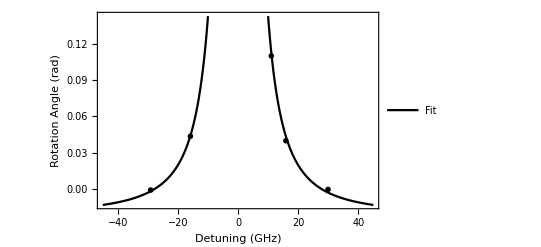
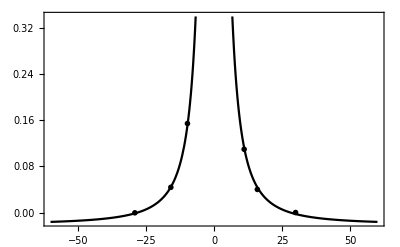
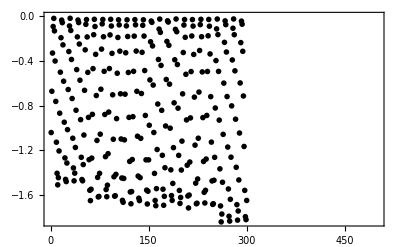
<|RawDetuning→{-29.053,-15.843,-9.743,11.067,15.917,29.947},RawAngles→{0.59596,0.640231,0.750988,0.706264,0.636524,0.596462},Working Dataset→<|-29.053→<|DETUNING→-29.053,ANGLE→-0.000502268,INTENSITY→-0.756233|>,-15.843→<|DETUNING→-15.843,ANGLE→0.0437689,INTENSITY→-0.830997|>,-9.743→<|DETUNING→-9.743,ANGLE→0.154526,INTENSITY→-0.846623|>,11.067→<|DETUNING→11.067,ANGLE→0.109802,INTENSITY→-0.854009|>,15.917→<|DETUNING→15.917,ANGLE→0.0400624,INTENSITY→-0.859899|>,29.947→<|DETUNING→29.947,ANGLE→0.,INTENSITY→-0.933145|>|>,Detuning→{-29.053,-15.843,-9.743,11.067,15.917,29.947},Angles→{-0.000502268,0.0437689,0.154526,0.109802,0.0400624,0.},Ordered Pairs→{{-29.053,-0.000502268},{-15.843,0.0437689},{-9.743,0.154526},{11.067,0.109802},{15.917,0.0400624},{29.947,0.}},Zero Angle→0.596462,BestFitParameters→{θ0→-0.0208109,a2→1.14852×10^-10,a4→100014.},n_Rbx10^12→18.10.5,n_RbPercentErr→0.0260417,graph→-Graphics-,graphNoLabel→-Graphics-,best fit function→-0.0208109+(1.00014×10^-13 (377107.+x)^2)/x^4+(1.14852×10^-10 (377107.+x)^2)/x^2,File→/home/pi/RbData/2021-07-14/FDayScan2021-07-14_152011.dat,Comments→Auto faradayScan, tracking density,IonGauge(Torr)→0.00252,CVGauge(Source Foreline)(Torr)→0.245,CVGauge(Target Foreline)(Torr)→0.654,T_res→158.1,T_res_set→0.,T_trg→191.5,T_trg_set→0.,BufferGasLeakValve(-)→45.5,BufferGasType(-)→Ethene,PumpLaserDLCurrent(mA)→167.651,PumpLaserAMPCurrent(mA)→1800,PumpLaserTemp(degC)→20.05,PumpLaserScanOffset(V)→53.4,PumpFrequency(THz)→377.109,PumpPolarizerAngleOuter(deg)→156,PumpPolarizerAngleInner(deg)→0,PumpQWPAngle(step)→72,ProbeCurrent(mA)→65,ProbeLP(deg)→232,ProbeFrequency(THz)→scanning,nominalDensity(cm^-3)→1.1×10^13,magnet1Voltage(V)→70,magnet2Voltage(V)→65.2,magnet3Voltage(V)→65.,WavemeterOffset(GHz)→1.3,Revolutions→1,DataPointsPerRev→50.,NumVolts→6,StepSize→7,Time→Wed 14 Jul 2021 15:20:11GMT-5,allRawDataPlot→-Graphics-,allRawData→{-1.04177,-0.671409,-0.328301,-0.090071,-0.017327,-0.12961,-0.39967,-0.76232,-1.12848,-1.40732,-1.51105,-1.44663,-1.20687,-0.868115,-0.500198,-0.190981,-0.03267,-0.055493,-0.25487,-0.581033,-0.949026,-1.26954,-1.46205,-1.48167,-1.31519,-1.01566,-0.65538,-0.31479,-0.085186,-0.016564,-0.125717,-0.386007,-0.736367,-1.09268,-1.35931,-1.47525,-1.4061,-1.1755,-0.841781,-0.476994,-0.183119,-0.031983,-0.055035,-0.247466,-0.57195,-0.925974,-1.26389,-1.46327,-1.47487,-1.32916,-1.06391,-0.66286,-0.299447,-0.070606,-0.027937,-0.183806,-0.501878,-0.90567,-1.28519,-1.55998,-1.65265,-1.55052,-1.27099,-0.878572,-0.468139,-0.163807,-0.025571,-0.090223,-0.339903,-0.709422,-1.11253,-1.44419,-1.61937,-1.61517,-1.40778,-1.05642,-0.652861,-0.293036,-0.06679,-0.02725,-0.182126,-0.492413,-0.879641,-1.25817,-1.55304,-1.61738,-1.51418,-1.2313,-0.857963,-0.467529,-0.165562,-0.025647,-0.085567,-0.331201,-0.703087,-1.10199,-1.43861,-1.6125,-1.6086,-1.41686,-0.916891,-0.509435,-0.188462,-0.029693,-0.075721,-0.311508,-0.693927,-1.09948,-1.44945,-1.65021,-1.66746,-1.45342,-1.10734,-0.697515,-0.325934,-0.084422,-0.030227,-0.17976,-0.502641,-0.905594,-1.30084,-1.57487,-1.68104,-1.57151,-1.28389,-0.899334,-0.492413,-0.176478,-0.028548,-0.075186,-0.310592,-0.671638,-1.07482,-1.4322,-1.63089,-1.65249,-1.44655,-1.09352,-0.691256,-0.321889,-0.079613,-0.029769,-0.176096,-0.485466,-0.888343,-1.28672,-1.5583,-1.6828,-1.56823,-1.28679,-0.976353,-0.569431,-0.227162,-0.04099,-0.052745,-0.264488,-0.615611,-1.04116,-1.40816,-1.65135,-1.69806,-1.54517,-1.19374,-0.785753,-0.386083,-0.113276,-0.02351,-0.142663,-0.43921,-0.842468,-1.24595,-1.55006,-1.69432,-1.6141,-1.35747,-0.982841,-0.565462,-0.223727,-0.039005,-0.05015,-0.259068,-0.607444,-1.00261,-1.37648,-1.60731,-1.65036,-1.49838,-1.17726,-0.774991,-0.388679,-0.115718,-0.022823,-0.136786,-0.431271,-0.823003,-1.24657,-1.5612,-1.67768,-1.62418,-1.37816,-1.11863,-0.694385,-0.323492,-0.077018,-0.027708,-0.187011,-0.5189,-0.92834,-1.3348,-1.61112,-1.71822,-1.60265,-1.30633,-0.910326,-0.494626,-0.175256,-0.02809,-0.086483,-0.340895,-0.723925,-1.15466,-1.49586,-1.68081,-1.67585,-1.45831,-1.09268,-0.678737,-0.305477,-0.073278,-0.0258,-0.181668,-0.497756,-0.907578,-1.30091,-1.57815,-1.67371,-1.56006,-1.27954,-0.888266,-0.49371,-0.173577,-0.026869,-0.087323,-0.336315,-0.719422,-1.12757,-1.47617,-1.68646,-1.68058,-1.46961,-1.26405,-0.821477,-0.396083,-0.11152,-0.023052,-0.162891,-0.492947,-0.930172,-1.36747,-1.70043,-1.84348,-1.77317,-1.4877,-1.05795,-0.598208,-0.232429,-0.039769,-0.073431,-0.319217,-0.718735,-1.17207,-1.54792,-1.79294,-1.83615,-1.64082,-1.26298,-0.80247,-0.390129,-0.105795,-0.022594,-0.163578,-0.487985,-0.921852,-1.35351,-1.68868,-1.82768,-1.74577,-1.46693,-1.04597,-0.596681,-0.234719,-0.041677,-0.069461,-0.312805,-0.713697,-1.16665,-1.56067,-1.79676,-1.8231,-1.65104}|>

```mathematica
today=DateString["ISODate"]
username=SystemInformation["Kernel","Username"];
If[username=="kahrendsen2",
rbData=FileNameJoin[{"\\\\129.93.33.132\\PiShare","RbData"}];,
Abort[];
];
collecting=FileExistsQ[FileNameJoin[{"\\\\129.93.33.132\\PiShare",".takingData"}]];
latestFile=If[collecting,-2,-1]
fn=FileNames[FileNameJoin[{rbData,today,"FDayScan*.dat"}]]
ProcessFaradayRotationNumberDensityFile[fn[[latestFile]]]
```

```mathematica
SystemOpen[FileNameJoin[{$PACKAGES,"apparatus.wl"}]]
```

```mathematica
SystemOpen[FileNameJoin[{$UserBaseDirectory,"Kernel","init.m"}]]
```

```mathematica
IAnrb[date_String:DateString["ISODate"]]:=Module[
{today,username,rbData,collecting,latestFile,fn},
today=DateString[date,"ISODate"];
username=SystemInformation["Kernel","Username"];
If[username=="kahrendsen2",
rbData=FileNameJoin[{"\\\\129.93.33.132\\PiShare","RbData"}];,
Abort[];
];
collecting=FileExistsQ[FileNameJoin[{"\\\\129.93.33.132\\PiShare",".takingData"}]];
latestFile=If[collecting,-2,-1];
fn=FileNames[FileNameJoin[{rbData,today,"FDayScan*.dat"}]];
Echo[fn[[latestFile]]];
ProcessFaradayRotationNumberDensityFile[fn[[latestFile]]]
]
```

# 2021-07-22: SciDraw

```mathematica
<<SciDraw`
```

𝒮𝒸𝒾𝒟𝓇𝒶𝓌: Publication–quality scientific figures with Mathematica
M. A. Caprio, University of Notre Dame
Version 0.0.7 (March 28, 2015)
View color paletteVisit home page  -Graphics-

```mathematica
Figure[
{
FigurePanel[
{
FigGraphics[Plot[x,{x,0,1}]];
}
,
XPlotRange->{0,1},
YPlotRange->{0,1},
XFrameLabel->"x",
YFrameLabel->"y",
Background->Moccasin,
PanelRegion->Scaled[{{0,.45},{0,1}}]];
FigurePanel[
{
FigGraphics[Plot[-x+1,{x,0,1}]];
},
XPlotRange->{0,1},
YPlotRange->{0,1},
XFrameLabel->"x",
YFrameLabel->"y",
Background->Moccasin, 
PanelRegion->Scaled[{{.55,1},{0,1}}]
];
},
CanvasSize->{10,3.5}
]
```

-Graphics-

```mathematica
<<asymmetry`
files=FileNames[FileNameJoin[{"20","asymmetry*"}]];
raw=ASYMRawOverview[Pick[files,StringContainsQ[files,"140535"]][[1]],"fd","\nFD, -9 V bias"];
asym=ListPlot[ASYMAsymmetry3[Pick[files,StringContainsQ[files,"140535"]][[1]],"fd"],
PlotLabel->"On Resonance Asymmetry",
FrameLabel->{"Measurement #","Asymmetry"}];
```

```mathematica
len=.6
Figure[
{
FigurePanel[
{
FigGraphics[raw];
}
,
XPlotRange->{0,200},
YPlotRange->{-9.5*^-9,-8.5*^-9},
XFrameLabel->"Measurement Number",
YFrameLabel->"Current (nA)",
PanelRegion->Scaled[{{0,.60},{0,1}}]];
FigurePanel[
{
FigGraphics[asym];
},
XPlotRange->{0,10},
YPlotRange->{-0.01,.01},
XFrameLabel->"Measurement 'Block'",
YFrameLabel->"Asymmetry", 
PanelRegion->Scaled[{{.70,1},{0,1}}]
];
},
CanvasSize->{16,3.5},
CanvasMargin->.5
]
```

0.6

-Graphics-